```mathematica
;;
```

Last updated:   Mon 15 Mar 2021

## Introduction

This notebook contains a basic computational exploration of Covid-19 based on data from multiple sources, including Twitter, Wikipedia, Wikidata and the Wolfram Data Framework. It is intended to offer more breadth of data sources than depth of analysis.

The notebook covers some properties of the disease, it’s spread and precautionary measures put in place around the world.

```mathematica
(* Wolfram Alpha summary of COVID-19 (as a disease) *)
```

WolframAlphaQueryResults

```mathematica
(* Wolfram Alpha summary of COVID-19 (as an epidemic) *)
```

WolframAlphaQueryResults

## Wikipedia

```mathematica
(* search for COVID-19-related articles on Wikipedia *)
```

{COVID-19,COVID-19 pandemic,COVID-19 pandemic by country and territory,COVID-19 vaccine,COVID-19 pandemic in the United States,COVID-19 pandemic in the United Kingdom,COVID-19 pandemic in India,COVID-19 pandemic in Italy,«34»,COVID-19 pandemic in Malaysia,COVID-19 pandemic in Croatia,COVID-19 pandemic in Ohio,COVID-19 pandemic in Africa,COVID-19 pandemic in the State of Palestine,COVID-19 pandemic in Ontario,COVID-19 pandemic in Poland,COVID-19 pandemic in Romania}

```mathematica
(* func for styling text *)
;
(* summary of Wikipedia article on "CoViD 19" *)
```

Coronavirus disease 2019 (COVID-19) is a contagious disease caused by severe acute respiratory syndrome coronavirus 2 (SARS-CoV-2). The first case was identified in Wuhan, China, in December 2019. The disease has since spread worldwide, leading to an ongoing pandemic.

Symptoms of COVID-19 are variable, but often include fever, cough, fatigue, breathing difficulties, and loss of smell and taste. Symptoms begin one to fourteen days after exposure to the virus. Of those people who develop noticeable symptoms, most (81%) develop mild to moderate symptoms (up to mild pneumonia), while 14% develop severe symptoms (dyspnea, hypoxia, or more than 50% lung involvement on imaging), and 5% suffer critical symptoms (respiratory failure, shock, or multiorgan dysfunction). Older people are more likely to have severe symptoms. At least a third of the people who are infected with the virus remain asymptomatic and do not develop noticeable symptoms at any point in time, but they still can spread the disease. Around 20% of those people will remain asymptomatic throughout infection, and the rest will develop symptoms later on, becoming pre-symptomatic rather than asymptomatic and therefore having a higher risk of transmitting the virus to others. Some people continue to experience a range of effects—known as long COVID—for months after recovery, and damage to organs has been observed. Multi-year studies are underway to further investigate the long-term effects of the disease.

The virus that causes COVID-19 spreads mainly when an infected person is in close contact with another person. Small droplets and aerosols containing the virus can spread from an infected person's nose and mouth as they breathe, cough, sneeze, sing, or speak. Other people are infected if the virus gets into their mouth, nose or eyes. The virus may also spread via contaminated surfaces, although this is not thought to be the main route of transmission. The exact route of transmission is rarely proven conclusively, but infection mainly happens when people are near each other for long enough. People who are infected can transmit the virus to another person up to two days before they themselves show symptoms, as can people who do not experience symptoms. People remain infectious for up to ten days after the onset of symptoms in moderate cases and up to 20 days in severe cases.
Several testing methods have been developed to diagnose the disease. The standard diagnostic method is by detection of the virus' nucleic acid by real-time reverse transcription polymerase chain reaction (rRT-PCR), transcription-mediated amplification (TMA), or by reverse transcription loop-mediated isothermal amplification (RT-LAMP) from a nasopharyngeal swab.
Preventive measures include physical or social distancing, quarantining, ventilation of indoor spaces, covering coughs and sneezes, hand washing, and keeping unwashed hands away from the face. The use of face masks or coverings has been recommended in public settings to minimise the risk of transmissions. Several vaccines have been developed and several countries have initiated mass vaccination campaigns.
Although work is underway to develop drugs that inhibit the virus, the primary treatment is currently symptomatic. Management involves the treatment of symptoms, supportive care, isolation, and experimental measures.

```mathematica
(* word cloud plotting function *)
:=;
```

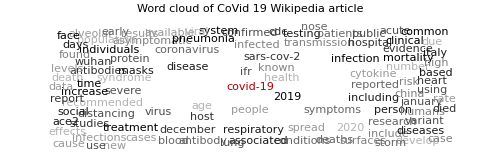
-Graphics- |  -  - covid-19120
 -  - virus67
 -  - people59
 -  - disease55
 -  - symptoms40

```mathematica
(* wordcloud of the CoviD-19 Wikipedia article *)
createWordCloud[WikipediaData["CoViD 19","ArticlePlaintext"],5,"covid-19",PlotLabel->Style["Word cloud of CoVid 19 Wikipedia article\n","Text",FontFamily->"Times"]]
```

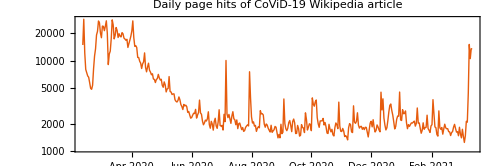

```mathematica
(* daily page hits of the article *)
```

We can also see a breakdown of how people have been accessing the article. Comparably way fewer people use the Wikipedia mobile app and that’s probably why that line is mostly flat for the entire period. Mobile web and Desktop views were initially the same but mobile grew faster in March. Views from Mobile and Desktop are now similar again in mid-May, though mobile is still slightly above. This could be because people are generally using their phones more frequently than their laptops each day.

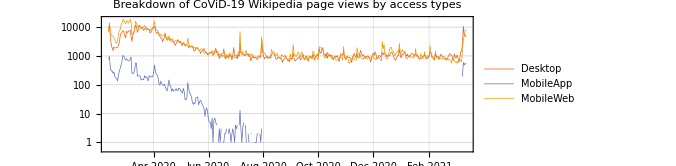

```mathematica
(* breakdown of page views by access types *)
```

But are all of those views even from real people? What portion of them are from bots?

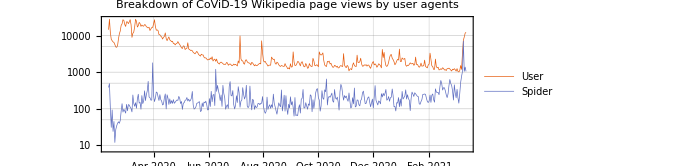

```mathematica
(* "Bot" is currenlty returning an error: "Wikipedia servers are currently under maintenance or experiencing a technical problem. Please try again in a few minutes." *)
```

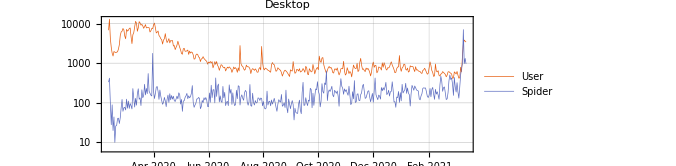
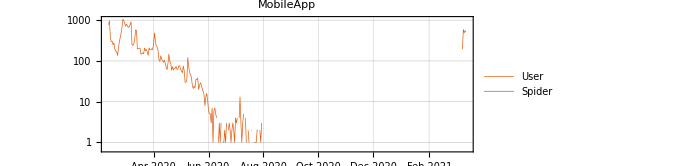
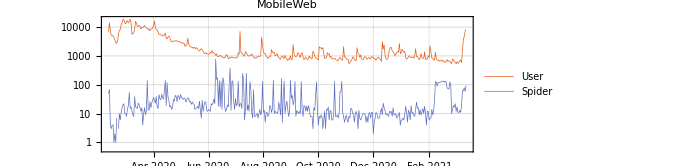
Breakdown of CoViD-19 Wikipedia page views by access types and user agents
-Graphics-
-Graphics-
-Graphics-

```mathematica
(* Spider views appear to come only from Desktop. Bot data also not available in this case *)
```

## Wikidata

```mathematica
(* search for COVID-19-related data on Wikipedia *)
WikidataSearch["Covid-19"]
```

{ExternalIdentifier[WikidataID,Q84263196,<|Label→COVID-19,Description→respiratory syndrome and infectious disease in humans, caused by SARS coronavirus 2|>]WikidataCOVID-19http://www.wikidata.org/entity/Q84263196,ExternalIdentifier[WikidataID,Q81068910,<|Label→COVID-19 pandemic,Description→ongoing pandemic of COVID-19, caused by the virus SARS-CoV-2|>]WikidataCOVID-19 pandemichttp://www.wikidata.org/entity/Q81068910,ExternalIdentifier[WikidataID,Q82069695,<|Label→SARS-CoV-2,Description→strain of virus causing the ongoing pandemic of coronavirus disease 2019 (COVID-19)|>]WikidataSARS-CoV-2http://www.wikidata.org/entity/Q82069695,ExternalIdentifier[WikidataID,Q91601520,<|Label→COVID-19,Description→scientific article published on 30 March 2020|>]WikidataCOVID-19http://www.wikidata.org/entity/Q91601520,ExternalIdentifier[WikidataID,Q94502207,<|Label→Covid-19,Description→scientific article published on 30 April 2020|>]WikidataCovid-19http://www.wikidata.org/entity/Q94502207,ExternalIdentifier[WikidataID,Q95935285,<|Label→COVID-19,Description→scientific article published on 28 May 2020|>]WikidataCOVID-19http://www.wikidata.org/entity/Q95935285,ExternalIdentifier[WikidataID,Q98661255,<|Label→COVID-19,Description→scientific article published on 23 June 2020|>]WikidataCOVID-19http://www.wikidata.org/entity/Q98661255}

```mathematica
(* view the properties of a given Wikidata item *)
WikidataData[ExternalIdentifier["WikidataID","Q87718451",<|"Label"->"2020 COVID-19 pandemic in Nigeria","Description"->"ongoing coronavirus pandemic in Nigeria"|>]"Wikidata""2020 COVID-19 pandemic in Nigeria"http://www.wikidata.org/entity/Q87718451, "NonIdentifierProperties"]
```

{ExternalIdentifier[WikidataID,P17,<|Label→country,Description→sovereign state of this item (not to be used for human beings)|>]Wikidatacountryhttp://www.wikidata.org/entity/P17,ExternalIdentifier[WikidataID,P31,<|Label→instance of,Description→that class of which this subject is a particular example and member|>]Wikidatainstance ofhttp://www.wikidata.org/entity/P31,ExternalIdentifier[WikidataID,P237,<|Label→coat of arms,Description→subject's coat of arms|>]Wikidatacoat of armshttp://www.wikidata.org/entity/P237,ExternalIdentifier[WikidataID,P373,<|Label→Commons category,Description→name of the Wikimedia Commons category containing files related to this item (without the prefix "Category:")|>]WikidataCommons categoryhttp://www.wikidata.org/entity/P373,ExternalIdentifier[WikidataID,P580,<|Label→start time,Description→time an item begins to exist or a statement starts being valid|>]Wikidatastart timehttp://www.wikidata.org/entity/P580,ExternalIdentifier[WikidataID,P625,<|Label→coordinate location,Description→geocoordinates of the subject. For Earth, please note that only WGS84 coordinating system is supported at the moment|>]Wikidatacoordinate locationhttp://www.wikidata.org/entity/P625,ExternalIdentifier[WikidataID,P828,<|Label→has cause,Description→underlying cause, thing that ultimately resulted in this effect|>]Wikidatahas causehttp://www.wikidata.org/entity/P828,ExternalIdentifier[WikidataID,P910,<|Label→topic's main category,Description→main Wikimedia category|>]Wikidatatopic's main categoryhttp://www.wikidata.org/entity/P910,ExternalIdentifier[WikidataID,P276,<|Label→location,Description→location of the object, structure or event. In the case of an administrative entity as containing item use P131 for statistical entities P8138. In the case of a geographic entity use P706. Use P7153 for locations associated with the object.|>]Wikidatalocationhttp://www.wikidata.org/entity/P276,ExternalIdentifier[WikidataID,P361,<|Label→part of,Description→object of which the subject is a part (if this subject is already part of object A which is a part of object B, then please only make the subject part of object A). Inverse property of "has part" (P527, see also "has parts of the class" (P2670)).|>]Wikidatapart ofhttp://www.wikidata.org/entity/P361,ExternalIdentifier[WikidataID,P8045,<|Label→organized response related to outbreak,Description→specific action taken or system used as a reaction to an outbreak|>]Wikidataorganized response related to outbreakhttp://www.wikidata.org/entity/P8045,ExternalIdentifier[WikidataID,P8204,<|Label→tabular case data,Description→tabular data on Wikimedia Commons of confirmed cases, recoveries, deaths, etc. due to a medical event; corresponds to P8011, P1603, P8049, P8010, P1120. Do not delete such statements.|>]Wikidatatabular case datahttp://www.wikidata.org/entity/P8204,ExternalIdentifier[WikidataID,P8687,<|Label→social media followers,Description→number of subscribers on a particular social media website (use as main statement only; see P3744 instead for qualifier). Qualify with "point in time" and property for account. For Twitter, use numeric id.|>]Wikidatasocial media followershttp://www.wikidata.org/entity/P8687,ExternalIdentifier[WikidataID,P1120,<|Label→number of deaths,Description→total (cumulative) number of people who died since start as a direct result of an event or cause|>]Wikidatanumber of deathshttp://www.wikidata.org/entity/P1120,ExternalIdentifier[WikidataID,P1603,<|Label→number of cases,Description→cumulative number of confirmed, probable and suspected occurrences|>]Wikidatanumber of caseshttp://www.wikidata.org/entity/P1603,ExternalIdentifier[WikidataID,P1846,<|Label→distribution map,Description→distribution of item on a mapped area (for  range map of taxa, use (P181).)|>]Wikidatadistribution maphttp://www.wikidata.org/entity/P1846,ExternalIdentifier[WikidataID,P2572,<|Label→hashtag,Description→hashtag associated with this item. Format: do not include the "#" symbol|>]Wikidatahashtaghttp://www.wikidata.org/entity/P2572,ExternalIdentifier[WikidataID,P3457,<|Label→case fatality rate,Description→proportion of patients who die of a particular medical condition out of all who have this condition within a given time frame|>]Wikidatacase fatality ratehttp://www.wikidata.org/entity/P3457,ExternalIdentifier[WikidataID,P8010,<|Label→number of recoveries,Description→number of cases that recovered from disease|>]Wikidatanumber of recoverieshttp://www.wikidata.org/entity/P8010}

```mathematica
(* view data and their respective sources *)
Values@WikidataData[ExternalIdentifier["WikidataID","Q87718451",<|"Label"->"2020 COVID-19 pandemic in Nigeria","Description"->"ongoing coronavirus pandemic in Nigeria"|>]"Wikidata""2020 COVID-19 pandemic in Nigeria"http://www.wikidata.org/entity/Q87718451, ExternalIdentifier["WikidataID","P1120",<|"Label"->"number of deaths","Description"->"Total (cumulative) number of people who died since start as a direct result of an event or cause"|>]"Wikidata""number of deaths"http://www.wikidata.org/entity/P1120,] // Short[#,5]&
```

{{2009.,{Fri 12 Mar 2021},{<|ExternalIdentifier[WikidataID,P813,<|Label→retrieved,Description→date or point in time that information was retrieved from a database or website (for use in online sources)|>]Wikidataretrievedhttp://www.wikidata.org/entity/P813→{Sat 13 Mar 2021},ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://github.com/CSSEGISandData/COVID-19]},ExternalIdentifier[WikidataID,P248,<|Label→stated in,Description→to be used in the references field to refer to the information document or database in which a claim is made; for qualifiers use P805|>]Wikidatastated inhttp://www.wikidata.org/entity/P248→{ExternalIdentifier[WikidataID,Q87456354,<|Label→An interactive web-based dashboard to track COVID-19 in real time,Description→scientific article from 2020|>]WikidataAn interactive web-based dashboard to track COVID-19 in real timehttp://www.wikidata.org/entity/Q87456354}|>}}}

```mathematica
(* get data for no. of cases and deaths *)
casesAndDeathsInNigeria = Association[
# -> WikidataData[ExternalIdentifier["WikidataID","Q87718451",<|"Label"->"2020 COVID-19 pandemic in Nigeria"|>]"Wikidata""2020 COVID-19 pandemic in Nigeria"http://www.wikidata.org/entity/Q87718451, #,]&/@{ExternalIdentifier["WikidataID","P1603",<|"Label"->"number of cases","Description"->"cumulative number of confirmed, probable and suspected occurrences"|>]"Wikidata""number of cases"http://www.wikidata.org/entity/P1603,ExternalIdentifier["WikidataID","P1120",<|"Label"->"number of deaths","Description"->"Total (cumulative) number of people who died since start as a direct result of an event or cause"|>]"Wikidata""number of deaths"http://www.wikidata.org/entity/P1120}
]/.(a_Association /; Length[a]<2) -> Nothing;
```

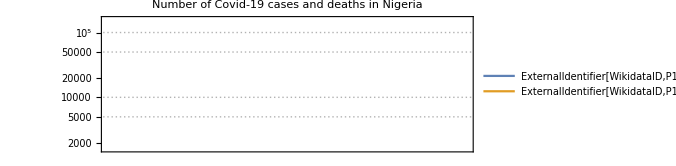

```mathematica
(* plot data *)
```

```mathematica
(* with Wikidata, properties have properties too. this is great for building a custom knowledge graph for a given topic *)
WikidataData[ExternalIdentifier["WikidataID","P1603",<|"Label"->"number of cases","Description"->"cumulative number of confirmed, probable and suspected occurrences"|>]"Wikidata""number of cases"http://www.wikidata.org/entity/P1603, "NonIdentifierProperties"]
```

{ExternalIdentifier[WikidataID,P1629,<|Label→subject item of this property,Description→item corresponding to the concept represented by the property|>]Wikidatasubject item of this propertyhttp://www.wikidata.org/entity/P1629,ExternalIdentifier[WikidataID,P1659,<|Label→see also,Description→used to indicate another property that might provide additional information about the Wikidata-property|>]Wikidatasee alsohttp://www.wikidata.org/entity/P1659,ExternalIdentifier[WikidataID,P1855,<|Label→Wikidata property example,Description→example where this Wikidata property is used; target item is one that would use this property, with qualifier the property being described given the associated value|>]WikidataWikidata property examplehttp://www.wikidata.org/entity/P1855,ExternalIdentifier[WikidataID,P2302,<|Label→property constraint,Description→constraint applicable to a Wikidata property|>]Wikidataproperty constrainthttp://www.wikidata.org/entity/P2302,ExternalIdentifier[WikidataID,P2668,<|Label→stability of property value,Description→likelihood that statements with this property will change|>]Wikidatastability of property valuehttp://www.wikidata.org/entity/P2668,ExternalIdentifier[WikidataID,P2875,<|Label→property usage tracking category,Description→category tracking a Wikidata property in sister projects|>]Wikidataproperty usage tracking categoryhttp://www.wikidata.org/entity/P2875,ExternalIdentifier[WikidataID,P3254,<|Label→property proposal discussion,Description→URL of the page (or page section) on which the creation of the property was discussed|>]Wikidataproperty proposal discussionhttp://www.wikidata.org/entity/P3254,ExternalIdentifier[WikidataID,P7452,<|Label→reason for preferred rank,Description→qualifier to allow the reason to be indicated why a particular statement should be considered preferred|>]Wikidatareason for preferred rankhttp://www.wikidata.org/entity/P7452,ExternalIdentifier[WikidataID,P31,<|Label→instance of,Description→that class of which this subject is a particular example and member|>]Wikidatainstance ofhttp://www.wikidata.org/entity/P31}

```mathematica
(* example property of a property *)
WikidataData[ExternalIdentifier["WikidataID","P1603",<|"Label"->"number of cases","Description"->"cumulative number of confirmed, probable and suspected occurrences"|>]"Wikidata""number of cases"http://www.wikidata.org/entity/P1603, ExternalIdentifier["WikidataID","P1659",<|"Label"->"see also","Description"->"used to indicate another property that might provide additional information about the Wikidata-property"|>]"Wikidata""see also"http://www.wikidata.org/entity/P1659]
```

{ExternalIdentifier[WikidataID,P8049,<|Label→number of hospitalized cases,Description→number of cases that are hospitalized|>]Wikidatanumber of hospitalized caseshttp://www.wikidata.org/entity/P8049,ExternalIdentifier[WikidataID,P8204,<|Label→tabular case data,Description→tabular data on Wikimedia Commons of confirmed cases, recoveries, deaths, etc. due to a medical event; corresponds to P8011, P1603, P8049, P8010, P1120. Do not delete such statements.|>]Wikidatatabular case datahttp://www.wikidata.org/entity/P8204,ExternalIdentifier[WikidataID,P1120,<|Label→number of deaths,Description→total (cumulative) number of people who died since start as a direct result of an event or cause|>]Wikidatanumber of deathshttp://www.wikidata.org/entity/P1120,ExternalIdentifier[WikidataID,P1193,<|Label→prevalence,Description→portion in percent of a population with a given disease or disorder|>]Wikidataprevalencehttp://www.wikidata.org/entity/P1193,ExternalIdentifier[WikidataID,P2844,<|Label→incidence,Description→probability of occurrence of a given condition in a population within a specified period of time|>]Wikidataincidencehttp://www.wikidata.org/entity/P2844,ExternalIdentifier[WikidataID,P8011,<|Label→number of clinical tests,Description→cumulative number of clinical tests|>]Wikidatanumber of clinical testshttp://www.wikidata.org/entity/P8011,ExternalIdentifier[WikidataID,P8010,<|Label→number of recoveries,Description→number of cases that recovered from disease|>]Wikidatanumber of recoverieshttp://www.wikidata.org/entity/P8010}

```mathematica
(* see info on a given data collection. this shows the braoder context of the data - it could be subset of a bigger dataset, and/or have it's own parts. *)
WikidataData[ExternalIdentifier["WikidataID","Q83873577",<|"Label"->"2020 COVID-19 pandemic in the United States","Description"->"viral outbreak in the United States"|>]"Wikidata""2020 COVID-19 pandemic in the United States"http://www.wikidata.org/entity/Q83873577, "Dataset"]
```

```mathematica
(* list of countries for which there is Wikidata coverage on Covid-19 pandemic *)
covidPandemicCountries = WikidataData[ExternalIdentifier["WikidataID","Q83741704",<|"Label"->"COVID-19 pandemic by country and territory","Description"->"details regarding the 2019–20 coronavirus pandemic by country and territory"|>]"Wikidata""COVID-19 pandemic by country and territory"http://www.wikidata.org/entity/Q83741704, ExternalIdentifier["WikidataID","P527",<|"Label"->"has part","Description"->"part of this subject; inverse property of \"part of\" (P361). See also \"has parts of the class\" (P2670)."|>]"Wikidata""has part"http://www.wikidata.org/entity/P527];
{Highlighted@Length@covidPandemicCountries, Short[covidPandemicCountries, .2]}
```

{197,{ExternalIdentifier[WikidataID,Q84055544,<|Label→COVID-19 pandemic in the Philippines,Description→pandemic in the Philippines|>]WikidataCOVID-19 pandemic in the Philippineshttp://www.wikidata.org/entity/Q84055544,ExternalIdentifier[WikidataID,Q84081307,<|Label→COVID-19 pandemic in Taiwan,Description→coronavirus pandemic in Taiwan|>]WikidataCOVID-19 pandemic in Taiwanhttp://www.wikidata.org/entity/Q84081307,ExternalIdentifier[WikidataID,Q84081576,<|Label→COVID-19 pandemic in Sweden,Description→ongoing coronavirus pandemic in Sweden|>]WikidataCOVID-19 pandemic in Swedenhttp://www.wikidata.org/entity/Q84081576,ExternalIdentifier[WikidataID,Q84098939,<|Label→COVID-19 pandemic in Russia,Description→details of ongoing coronavirus pandemic in Russia in 2020|>]WikidataCOVID-19 pandemic in Russiahttp://www.wikidata.org/entity/Q84098939,«189»,ExternalIdentifier[WikidataID,Q87768605,<|Label→COVID-19 pandemic in Afghanistan,Description→ongoing viral pandemic in Afghanistan|>]WikidataCOVID-19 pandemic in Afghanistanhttp://www.wikidata.org/entity/Q87768605,ExternalIdentifier[WikidataID,Q87770645,<|Label→2020 COVID-19 pandemic in Somalia,Description→viral pandemic in Somalia|>]Wikidata2020 COVID-19 pandemic in Somaliahttp://www.wikidata.org/entity/Q87770645,ExternalIdentifier[WikidataID,Q87770827,<|Label→2020 COVID-19 pandemic in Tanzania,Description→viral pandemic in Tanzania|>]Wikidata2020 COVID-19 pandemic in Tanzaniahttp://www.wikidata.org/entity/Q87770827,ExternalIdentifier[WikidataID,Q87452683,<|Label→COVID-19 pandemic in Basque Country|>]WikidataCOVID-19 pandemic in Basque Countryhttp://www.wikidata.org/entity/Q87452683}}

Responses to the outbreak differ from one country to another. Also, the absence of data for a particular country does not suggest that no precautions were put in place.

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q87186365",<|"Label"->"2020 COVID-19 pandemic in the Republic of Ireland","Description"->"details of ongoing viral outbreak in the Republic of Ireland"|>]"Wikidata""2020 COVID-19 pandemic in the Republic of Ireland"http://www.wikidata.org/entity/Q87186365,  ExternalIdentifier["WikidataID","P8045",<|"Label"->"organized response related to outbreak","Description"->"specific action taken or system used as a reaction to an outbreak"|>]"Wikidata""organized response related to outbreak"http://www.wikidata.org/entity/P8045]
```

{ExternalIdentifier[WikidataID,Q93623431,<|Label→2020 Ireland COVID-19 social distancing,Description→COVID-19 countermeasure in Ireland|>]Wikidata2020 Ireland COVID-19 social distancinghttp://www.wikidata.org/entity/Q93623431,ExternalIdentifier[WikidataID,Q93623429,<|Label→2020 Ireland COVID-19 closing of educational institutions,Description→COVID-19 countermeasure in Ireland|>]Wikidata2020 Ireland COVID-19 closing of educational institutionshttp://www.wikidata.org/entity/Q93623429,ExternalIdentifier[WikidataID,Q93623435,<|Label→2020 Ireland COVID-19 closing of non-essential businesses,Description→COVID-19 countermeasure in Ireland|>]Wikidata2020 Ireland COVID-19 closing of non-essential businesseshttp://www.wikidata.org/entity/Q93623435,ExternalIdentifier[WikidataID,Q93623433,<|Label→2020 Ireland COVID-19 lockdown,Description→COVID-19 countermeasure in Ireland|>]Wikidata2020 Ireland COVID-19 lockdownhttp://www.wikidata.org/entity/Q93623433}

```mathematica
(* see when a particular measure was announced and enacted *)
WikidataData[ExternalIdentifier["WikidataID","Q93623431",<|"Label"->"2020 Ireland COVID-19 social distancing","Description"->"COVID-19 countermeasure in Ireland"|>]"Wikidata""2020 Ireland COVID-19 social distancing"http://www.wikidata.org/entity/Q93623431, "Dataset"]
```

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q93623431",<|"Label"->"2020 Ireland COVID-19 social distancing","Description"->"COVID-19 countermeasure in Ireland"|>]"Wikidata""2020 Ireland COVID-19 social distancing"http://www.wikidata.org/entity/Q93623431, "NonIdentifierProperties"]
```

{ExternalIdentifier[WikidataID,P580,<|Label→start time,Description→time an item begins to exist or a statement starts being valid|>]Wikidatastart timehttp://www.wikidata.org/entity/P580,ExternalIdentifier[WikidataID,P828,<|Label→has cause,Description→underlying cause, thing that ultimately resulted in this effect|>]Wikidatahas causehttp://www.wikidata.org/entity/P828,ExternalIdentifier[WikidataID,P1001,<|Label→applies to jurisdiction,Description→the item (an institution, law, public office ...) or statement belongs to or has power over or applies to the value (a territorial jurisdiction: a country, state, municipality, ...)|>]Wikidataapplies to jurisdictionhttp://www.wikidata.org/entity/P1001,ExternalIdentifier[WikidataID,P6949,<|Label→announcement date,Description→time of the first public presentation of a subject by the creator, of information by the media|>]Wikidataannouncement datehttp://www.wikidata.org/entity/P6949,ExternalIdentifier[WikidataID,P31,<|Label→instance of,Description→that class of which this subject is a particular example and member|>]Wikidatainstance ofhttp://www.wikidata.org/entity/P31}

```mathematica
(* responses of countries for which this data is available *)
covidPandemicResponses = DeleteCases[
Thread[# -> WikidataData[#, ExternalIdentifier["WikidataID","P8045",<|"Label"->"organized response related to outbreak","Description"->"specific action taken or system used as a reaction to an outbreak"|>]"Wikidata""organized response related to outbreak"http://www.wikidata.org/entity/P8045]]&@covidPandemicCountries // Association,
{}];
```

```mathematica
(* Sweden has so far has the highest number of distinct responses, followed by Jordan and New Zealand. *)
ReverseSortBy[Length]@covidPandemicResponses // Dataset[#, MaxItems->5]&
(* Sweden's responses *)
%[1]
```

```mathematica
(* response type and start date data for all countries *)
covidPandemicResponsesData = MapAt[Flatten, WikidataData[#, {ExternalIdentifier["WikidataID","P31",<|"Label"->"instance of","Description"->"that class of which this subject is a particular example and member"|>]"Wikidata""instance of"http://www.wikidata.org/entity/P31, ExternalIdentifier["WikidataID","P580",<|"Label"->"start time","Description"->"time an item begins to exist or a statement starts being valid"|>]"Wikidata""start time"http://www.wikidata.org/entity/P580}]&/@covidPandemicResponses, {;;, ;;}];
(* view data *)
covidPandemicResponsesData // Dataset[#, MaxItems->5]&
```

```mathematica
(* top 3 countries by no. of measures taken *)
```

<|ExternalIdentifier[WikidataID,Q84081576,<|Label→COVID-19 pandemic in Sweden,Description→ongoing coronavirus pandemic in Sweden|>]WikidataCOVID-19 pandemic in Swedenhttp://www.wikidata.org/entity/Q84081576→12,ExternalIdentifier[WikidataID,Q87589148,<|Label→2020 COVID-19 pandemic in Jordan,Description→viral pandemic in Jordan|>]Wikidata2020 COVID-19 pandemic in Jordanhttp://www.wikidata.org/entity/Q87589148→8,ExternalIdentifier[WikidataID,Q87250803,<|Label→COVID-19 pandemic in New Zealand,Description→Ongoing coronavirus pandemic in New Zealand|>]WikidataCOVID-19 pandemic in New Zealandhttp://www.wikidata.org/entity/Q87250803→7|>

```mathematica
(* tally of responses by all countries *)
 //
```

ExternalIdentifier[WikidataID,Q88323877,<|Label→closing of educational institutions,Description→action to reduce virus transmission|>]Wikidataclosing of educational institutionshttp://www.wikidata.org/entity/Q88323877 | 56
ExternalIdentifier[WikidataID,Q30314010,<|Label→social distancing,Description→reduction of human social interaction in an effort to prevent the spread of infectious disease|>]Wikidatasocial distancinghttp://www.wikidata.org/entity/Q30314010 | 54
ExternalIdentifier[WikidataID,Q87745167,<|Label→travel restriction,Description→policy|>]Wikidatatravel restrictionhttp://www.wikidata.org/entity/Q87745167 | 50
ExternalIdentifier[WikidataID,Q7257745,<|Label→declaration of public health emergency,Description→declaration of a public health emergency in response to a (public) health crisis|>]Wikidatadeclaration of public health emergencyhttp://www.wikidata.org/entity/Q7257745 | 43
ExternalIdentifier[WikidataID,Q88761394,<|Label→travel ban,Description→restriction of all means of travel|>]Wikidatatravel banhttp://www.wikidata.org/entity/Q88761394 | 38
ExternalIdentifier[WikidataID,Q88761692,<|Label→flight ban,Description→Restriction of air travel, e.g. closure of airports|>]Wikidataflight banhttp://www.wikidata.org/entity/Q88761692 | 32
ExternalIdentifier[WikidataID,Q6665312,<|Label→lockdown,Description→emergency protocol that prevents people or information from leaving an area, usually only initiated by someone in a position of authority|>]Wikidatalockdownhttp://www.wikidata.org/entity/Q6665312 | 31
ExternalIdentifier[WikidataID,Q223625,<|Label→curfew,Description→ban on entering public areas such as streets or squares at certain times|>]Wikidatacurfewhttp://www.wikidata.org/entity/Q223625 | 27
ExternalIdentifier[WikidataID,Q89681240,<|Label→closing of non-essential businesses|>]Wikidataclosing of non-essential businesseshttp://www.wikidata.org/entity/Q89681240 | 16
ExternalIdentifier[WikidataID,Q89211965,<|Label→decision by the Swedish Government,Description→formal decisions in government meetings|>]Wikidatadecision by the Swedish Governmenthttp://www.wikidata.org/entity/Q89211965 | 5
ExternalIdentifier[WikidataID,Q182899,<|Label→quarantine,Description→epidemiological intervention of restriction on the movement of people and goods, which is intended to prevent the spread of infectious disease or pests|>]Wikidataquarantinehttp://www.wikidata.org/entity/Q182899 | 5
ExternalIdentifier[WikidataID,Q88218880,<|Label→Yo me quedo en casa|>]WikidataYo me quedo en casahttp://www.wikidata.org/entity/Q88218880 | 4
ExternalIdentifier[WikidataID,Q5370734,<|Label→emergency procedure,Description→plan of action to deal with an emergency|>]Wikidataemergency procedurehttp://www.wikidata.org/entity/Q5370734 | 2
ExternalIdentifier[WikidataID,Q88707306,<|Label→border closure,Description→action to reduce virus transmission in the community|>]Wikidataborder closurehttp://www.wikidata.org/entity/Q88707306 | 1
ExternalIdentifier[WikidataID,Q88705465,<|Label→travel advice as non-pharmaceutical countermeasure,Description→action to reduce virus transmission in the community|>]Wikidatatravel advice as non-pharmaceutical countermeasurehttp://www.wikidata.org/entity/Q88705465 | 1
ExternalIdentifier[WikidataID,Q88324058,<|Label→avoiding crowding,Description→action to reduce virus transmission|>]Wikidataavoiding crowdinghttp://www.wikidata.org/entity/Q88324058 | 1
ExternalIdentifier[WikidataID,Q820655,<|Label→legislative act,Description→formal written document that creates law, including acts, executive orders, and by-laws|>]Wikidatalegislative acthttp://www.wikidata.org/entity/Q820655 | 1
ExternalIdentifier[WikidataID,Q5797593,<|Label→State of Alarm (Spain),Description→Situation in which a Spanish Government is empowered to perform special actions|>]WikidataState of Alarm (Spain)http://www.wikidata.org/entity/Q5797593 | 1
ExternalIdentifier[WikidataID,Q2795484,<|Label→implementing regulation,Description→regulation on the details of the implementation of a law|>]Wikidataimplementing regulationhttp://www.wikidata.org/entity/Q2795484 | 1
ExternalIdentifier[WikidataID,Q26256810,<|Label→matter,Description→topic or area addressed by a work|>]Wikidatamatterhttp://www.wikidata.org/entity/Q26256810 | 1
ExternalIdentifier[WikidataID,Q216200,<|Label→legal norm,Description→commandment, instruction, or order intended as an authoritative rule of action|>]Wikidatalegal normhttp://www.wikidata.org/entity/Q216200 | 1
ExternalIdentifier[WikidataID,Q2141795,<|Label→cordon sanitaire,Description→isolation of a geographic area to prevent the spread of infectious disease or, metaphorically, of ideas considered politically dangerous|>]Wikidatacordon sanitairehttp://www.wikidata.org/entity/Q2141795 | 1
ExternalIdentifier[WikidataID,Q207184,<|Label→press release,Description→instrument of public relations|>]Wikidatapress releasehttp://www.wikidata.org/entity/Q207184 | 1
ExternalIdentifier[WikidataID,Q1864008,<|Label→legal act,Description→juridical fact in which the subject who made it happen acted under free will|>]Wikidatalegal acthttp://www.wikidata.org/entity/Q1864008 | 1
ExternalIdentifier[WikidataID,Q1032176,<|Label→countermeasure,Description→specific action taken or system used to offset another action|>]Wikidatacountermeasurehttp://www.wikidata.org/entity/Q1032176 | 1

```mathematica
(* compare start dates of Covid-19 responses around the world *)
responseTimelinePlot[response_, plotLabel_] :=
```

```mathematica
(* educational institutions *)
responseTimelinePlot[ExternalIdentifier["WikidataID","Q88323877",<|"Label"->"closing of educational institutions","Description"->"action to reduce virus transmission"|>]"Wikidata""closing of educational institutions"http://www.wikidata.org/entity/Q88323877, "Start of closing of educational institutions"]
```

-Graphics-

```mathematica
(* social distancing *)
responseTimelinePlot[ExternalIdentifier["WikidataID","Q30314010",<|"Label"->"social distancing","Description"->"reduction of human social interaction in an effort to prevent the spread of infectious disease"|>]"Wikidata""social distancing"http://www.wikidata.org/entity/Q30314010, "Start of closing of social distancing"]
```

-Graphics-

Note the not every country is included in the couple of plots above. For example, social distancing was introduced in the UK in March but this does not appear in Wikidata.

### Government measures data from Wolfram Data Repository

On the Wolfram Data Repository, there is a dataset on measures taken by governments around the world. This dataset contains more detailed information than what we can pull from Wikidata.

-Graphics-

```mathematica
(* resource object *)
resObj = ResourceObject["Coronavirus COVID-19 Pandemic Government Measures"]
```

ResourceObject[…]

```mathematica
(* get resource data *)
resObjData = ResourceData@resObj
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Dataset[<>]

Each enacted measure is categorised and contains 18 a total of properties including its implementation data and the source of the information.

```mathematica
resObjData[GroupBy@"Category", ;;, "Measure"][;;, Tally][;;, ReverseSortBy@Last]
```

```mathematica
(* groupings of categories and measures *)
```

-Graphics-

```mathematica
(* category-measure tally data *)
cmTallies = Normal@Echo[Tally/@resObjData[GroupBy@"Category", ;;, "Measure"]];
```

```mathematica
(* breakdown of categories and measures *)
//
```

-Graphics-

```mathematica
(* proportions of measures - applied as graph edge thickness values below *)
measuresEdgeSizes = ;
measuresEdgeSizes = ;
```

```mathematica
(* proportions of categories - applied as vertex size values below *)
categoriesVertexSizes = ;
```

```mathematica
(* graphical form of breakdown *)
```

-Graphics-

## Wolfram Data Framework / Entities

Natural language input “Covid-19” is automatically interpreted as a disease and converted to an explorable real-world entity.

WolframAlphaQueryParseResults

COVID-19

```mathematica
(* Covid-19 as a disease entity *)
covid19 = Entity["Disease","NovelCoronavirusDisease"]; covid19["Properties"]
```

{average patient age,age of onset,associated genes,basic reproduction number,average patient BMI,average temperature,causes,common symptoms,definition,average diastolic blood pressure,duration,entity classes,exposure to disease onset,average patient height,ICD-9 code,ICD-10 code,image,name,prevalence,prevalence rate,prevention,risks,medical specialty,average systolic blood pressure,transmission,treatment,average patient weight}

```mathematica
(* properties of Covid-19 *)
covid19["Dataset"]
```

```mathematica
(* see how Covid-19 compares to other infectious diseases *)
infectDis = ;
%~Short~.2
```

{Ebola virus disease,cholera,salmonella infections,shigellosis,«68»,sepsis,Middle East respiratory syndrome,COVID-19,Zika virus disease}

```mathematica
(* prevention measures *)
infectDisPrevention = ;
Short[%]
```

{Ebola virus disease→{coordinated medical services,careful handling of bushmeat},«50»,Zika virus disease→{decreasin…ito bites,…}}

```mathematica
(* groupings of infectious diseases by prevention measures *)
Dataset@KeySort@
```

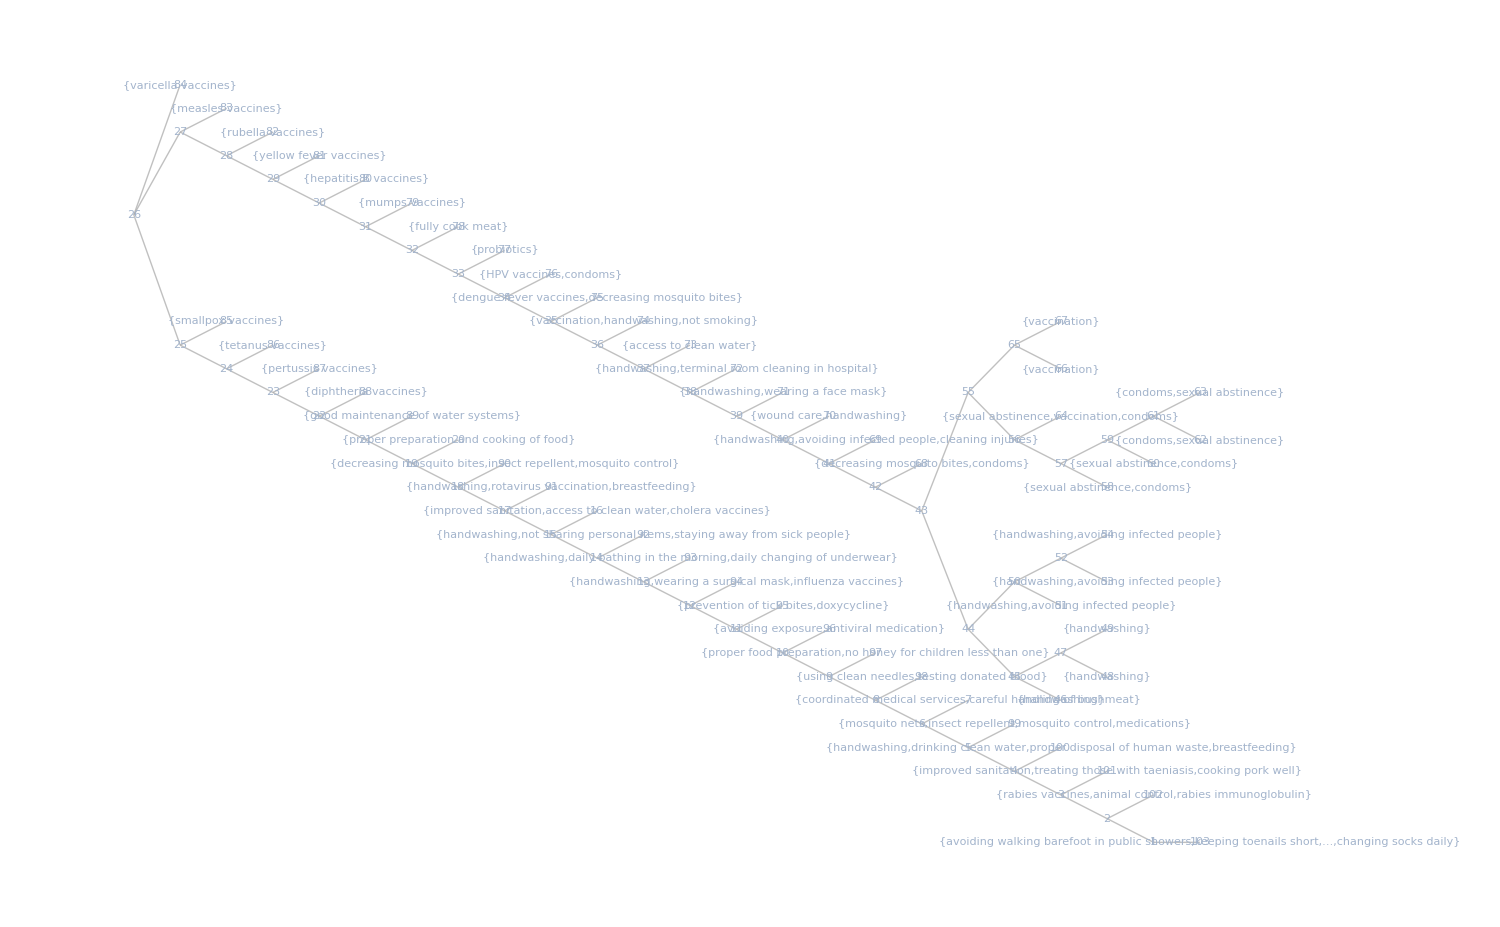

```mathematica
(* similarity between prevention measures *)
```

```mathematica
(* exposure to onset. note that data is not available for some entities  *)
infectDisExp =
```

{Ebola virus disease→(2to21) days,cholera→(1/12 to5) days,salmonella infections→(1/2 to3) days,shigellosis→(1to2) days,botulism→(1/2 to3) days,diphtheria→(2to5) days,streptococcal sore throat→(1to3) days,tetanus→(3to21) days,smallpox→(7to21) days,chicken pox→(10to21) days,genital herpes→(2to12) days,measles→(8to12) days,rubella→14. days,yellow fever→(3to6) days,Dengue fever→(3to14) days,eastern equine encephalitis→(4to10) days,viral hepatitis B without hepatic coma→(30to180) days,mumps→(14to21) days,hand, foot, and mouth disease→(3to6) days,Condyloma acuminatum→(365/12 to 730/3) days,unclassified diseases due to viruses and Chlamydiae→(7to21) days,severe acute respiratory syndrome→(2to7) days,unspecified type of chlamydial infection co-occurring with other medical conditions→(14to21) days,rickettsioses→(7to14) days,malaria→(10to15) days,lyme disease→7. days,enterobiasis→(28to56) days,scabies→(14to42) days,Legionnaires' disease→(2to10) days,influenza→3. days,Middle East respiratory syndrome→(2to14) days,COVID-19→(2to14) days}

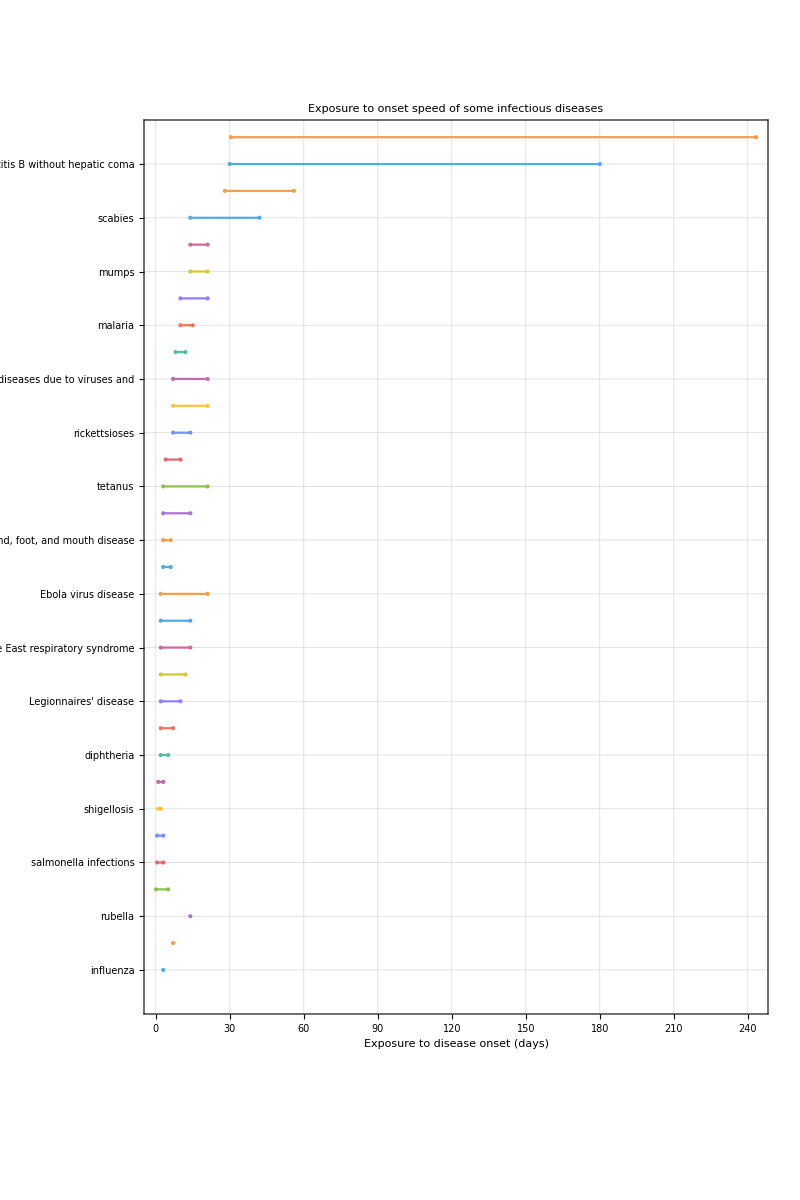

```mathematica
(* plot can be inproved with markers but NumberLinePlot doesn't support this option *)
```

```mathematica
(* TimelinePlot can't interpret time interval *)
```

-Graphics-

```mathematica
(* reproduction no. (Subscript[R, 0]) of such diseases. note that data is not available for some entities  *)
infectDisR0 =
```

{Ebola virus disease→Interval[{1.5,2.5}],diphtheria→Interval[{6.,7.}],whooping cough→5.5,smallpox→Interval[{5.,7.}],measles→Interval[{12.,18.}],rubella→Interval[{5.,7.}],mumps→Interval[{4.,7.}],severe acute respiratory syndrome→Interval[{2.,5.}],influenza→Interval[{2.,3.}],Middle East respiratory syndrome→Interval[{0.6,1.}],COVID-19→Interval[{1.4,2.5}]}

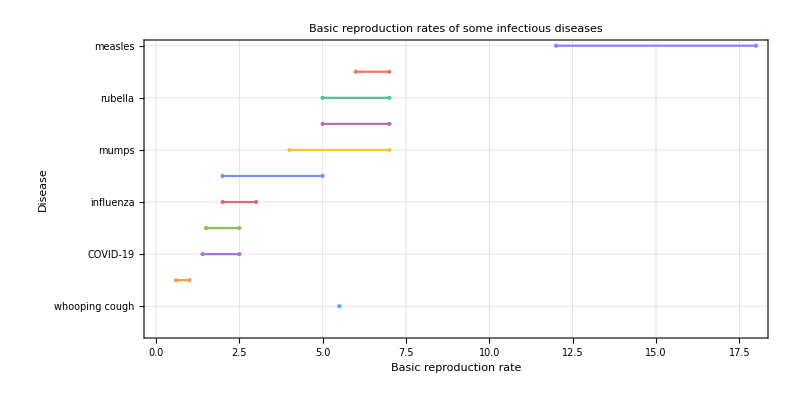

```mathematica
(* no. line plot of Subscript[R, 0] *)
```

## Social Media (Twitter)

Social media data on the Covid-19 pandemic can also be explored. For example we can look at discussions and conversations on related to the pandemic on Twitter.

```mathematica
(* connect to Twitter (a Twitter account is required for this) *)
tw = ServiceConnect["Twitter"]
```

ServiceObject[…]

Be mindful of your rate limits when querying the Twitter service. You can see rate limits for queries by running: tw["RateLimit"].

```mathematica
(* possible queries *)
Panel/@tw/@{"Requests", "RawRequests"}
```

{{Authentication,FollowerIDs,FollowerMentionNetwork,FollowerNetwork,FollowerReplyToNetwork,Followers,FriendIDs,FriendMentionNetwork,FriendNetwork,FriendReplyToNetwork,Friends,GetTweet,GetTweets,ID,Information,LastTweet,Name,RateLimit,RawRequests,Retweet,SearchMentionNetwork,SearchNetwork,SearchReplyToNetwork,Tweet,TweetEventSeries,TweetList,TweetSearch,TweetTimeline,UserData,UserHashtags,UserIDSearch,UserMentions,UserReplies},{RawAccountStatus,RawAddFavorite,RawBlockIDs,RawBlockList,RawContributees,RawContributors,RawCreateBlock,RawDeleteDirectMessage,RawDeleteTweet,RawDirectMessage,RawDirectMessages,RawDirectMessagesSent,RawFavorites,RawFollowerIDs,RawFollowers,RawFriendIDs,RawFriends,RawFriendship,RawGetTweets,RawHomeTimeline,RawIncomingFriendships,RawMediaUpload,RawMentionsTimeline,RawMyFriendship,RawNoRetweetUserIDs,RawOutgoingFriendships,RawRemoveBlock,RawRemoveFavorite,RawRetweet,RawRetweeterIDs,RawRetweets,RawRetweetTimeline,RawSendDirectMessage,RawSetUserSettings,RawStartFollowing,RawStatus,RawStopFollowing,RawSuggestedUserCategories,RawSuggestedUsers,RawSuggestedUserStatuses,RawTweetSearch,RawUpdate,RawUpdateBackgroundImage,RawUpdateDevice,RawUpdateFollowing,RawUpdateProfile,RawUpdateProfileColors,RawUpload,RawUser,RawUsers,RawUserSearch,RawUserSettings,RawUserTimeline,RawVerifyCredentials}}

### Trends

```mathematica
(* see available trends around the world; trends are represented by 'woeid' *)
twitterTrends = Dataset[tw["RawTrendsAvailable"], MaxItems->10]
```

```mathematica
(* no. of trends by country *)
twitterTrendsNo =  @ ;
```

```mathematica
(* plots of no. of trends *)
 &@ twitterTrendsNo;
```

-Graphics-

```mathematica
(* worldwide trends *)
```

As of:  Fri 22 May 2020 03:12:10GMT+1.

```mathematica
(* group trends by presense of the words "covid" or "corona" *)
```

```mathematica
(* extract trend ids for each country, where one is available *)
twitterTrendsIDs =
```

```mathematica
(* get top 50 trends in each country, sorted by volume of tweets *)
twitterCountryTrends =
```

Dataset[<>]

```mathematica
(* group countries by trends *)
twitterTrendsGrouped = ;
(* select "covid" and "corona" trends: *)
twitterTrendsGrouped =
```

### Search

```mathematica
(* search for tweets containing "covid"; Twitter's user API currently only returns up to 100 tweets *)
search=Dataset@tw["RawTweetSearch",{"q"->"*covid*","count"->"100","lang"->"en","result_type"->"mixed","until"->"2020-05-22","include_entities"->"false"}]
```

Dataset[<>]

```mathematica
(* extract tweets from search *)
tweets=search⟦"statuses"⟧;
RandomChoice[tweets,1]
```

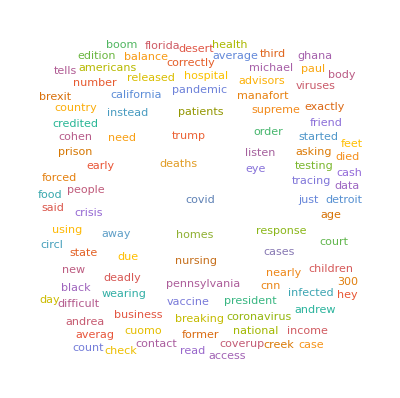

```mathematica
(* wordcloud of tweets *)
```

```mathematica
(* user data on informative accounts *)
Dataset@tw["UserData","Username"->{"WHO","CDCgov","NHS","NCDCgov"}]
```

```mathematica
(* get up to 5k WHO tweets *)
whoTweets=tw["TweetList","Username"->"WHO",MaxItems->3000];
```

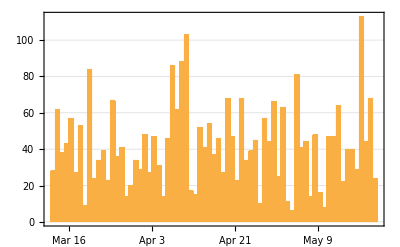

```mathematica
(* date histogram, with day-sized bins *)
DateHistogram[whoTweets[;;,"Date"],"Day",PlotTheme->"Business"]
```

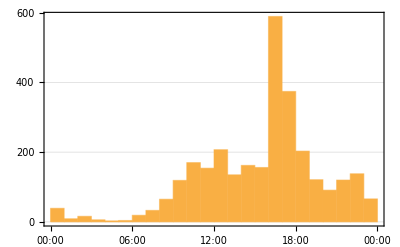

```mathematica
(* date histogram, binned by hour of day *)
DateHistogram[whoTweets[;;,"Date"],DateReduction->"Day",PlotTheme->"Business"]
```

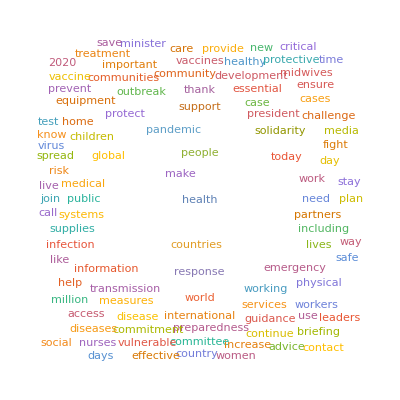

```mathematica
(* wordcloud of WHO tweets *)
DeleteCases[Flatten[ToLowerCase/@DeleteStopwords/@TextWords/@whoTweets[;;,"Text"]],w_/;StringLength[w]<3||StringContainsQ[w,"@"|PunctuationCharacter]]//WordCloud
```

```mathematica
whoTweetsGroupedByDate=KeyMap[StringRiffle]@GroupBy[whoTweets,#["Date"][{"MonthName","Year"}]&]
```

Dataset[<>]

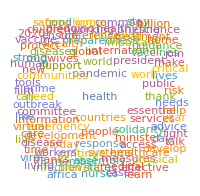
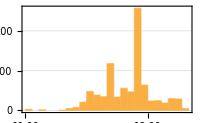
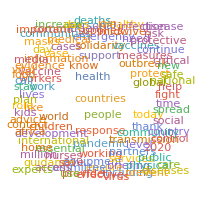
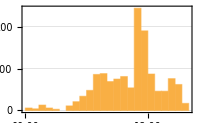
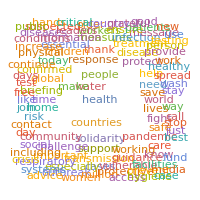
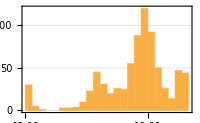
May 2020
-Graphics-
-Graphics-April 2020
-Graphics-
-Graphics-March 2020
-Graphics-
-Graphics-

```mathematica
(* compare WHO tweets over time *)
```

## Data (CSSE COVID-19 Daily Reports)

The importance of going through the Github links and getting latest data is that the entire process can be automated easily. Whereas, getting the latest data from Kaggle and doing some manual file operations can’t.

```mathematica
(* JHU CSSEGIS Github repository, where data is automatically updated daily *)
githubURL="https://github.com/CSSEGISandData/COVID-19/tree/master/csse_covid_19_data/csse_covid_19_daily_reports";
```

```mathematica
(* all hyperlinks in repo *)
githubLinks=Import[githubURL,"Hyperlinks"];
Short[githubLinks,5]
```

{https://github.com/CSSEGISandData/COVID-19/tree/master/csse_covid_19_data/csse_covid_19_daily_reports,https://github.com/CSSEGISandData/COVID-19/tree/master/csse_covid_19_data/csse_covid_19_daily_reports,«896»,https://github.com/CSSEGISandData/COVID-19/tree/master/csse_covid_19_data/csse_covid_19_daily_reports,https://github.com/CSSEGISandData/COVID-19/tree/master/csse_covid_19_data/csse_covid_19_daily_reports}

```mathematica
(* get links to .CSV files *)
githubLinksCSV=Cases[githubLinks,l_/;StringEndsQ[l,".csv"],∞];
{Highlighted@Length@githubLinksCSV,Short@githubLinksCSV}
```

{418,{https://github.com/CSSEGISandData/COVID-19/blob/master/csse_covid_19_data/csse_covid_19_daily_reports/01-01-2021.csv,«416»,htt…csv}}

```mathematica
(* create a date->URL association for each day's data URL. this is reverse date-sorted (latest to earliest) *)
Off[DateObject::ambig]; (* we're taking care of ambiguity of day-month thing by specifying $DateStringFormat, so we'll turn this off *)
dateURLAssoc=;
Short@dateURLAssoc
```

{<|Date→Sun 14 Mar 2021,Link→https://github.com/CSSEGISandData/COVID-1…sse_covid_19_daily_reports/03-14-2021.csv|>,«416»,«1»}

```mathematica
(* range of data we have *)
dateInterval=MinMax["Date"/.dateURLAssoc]
DateDifference@@dateInterval
```

{Wed 22 Jan 2020,Sun 14 Mar 2021}

417 days

```mathematica
(* "dataset" of datasets we've got so far *)
Column[{
(* range *) ,
(* ds *)(dateURLDataset=Dataset[dateURLAssoc,MaxItems->5])
},Alignment->Center]
```

Date range:  Wed 22 Jan 2020 to Sun 14 Mar 2021  (417)

```mathematica
(* from the dataset above, we can very conveniently get data for a given day within the data range *)
(* we can see that we have data for yesterday, but not yet for today and tomorrow. Note that times are based on US timezone (presumably same as the CSSE). *)
Between[#,dateInterval]&/@{Yesterday,Today,Tomorrow}
```

{True,False,False}

```mathematica
First@dateURLDataset[Select[#"Date"==Yesterday&],"Link"]
```

https://github.com/CSSEGISandData/COVID-19/blob/master/csse_covid_19_data/csse_covid_19_daily_reports/03-14-2021.csv

```mathematica
(* we can now simply specify a date to get it's data. we can make this work even for natural lang. inputs. *)
First@dateURLDataset[Select[#"Date"==Yesterday&],"Link"]
First@dateURLDataset[Select[#"Date"==SemanticInterpretation["2 days ago"]&],"Link"]
First@dateURLDataset[Select[#"Date"==SemanticInterpretation["last Tuesday"]&],"Link"]
```

https://github.com/CSSEGISandData/COVID-19/blob/master/csse_covid_19_data/csse_covid_19_daily_reports/01-20-2021.csv

## Data prep and preprocessing

### Raw dataset

```mathematica
(* let's explore the latest data we have *)
exploreDataURL=
```

https://raw.githubusercontent.com/CSSEGISandData/COVID-19/master/csse_covid_19_data/csse_covid_19_daily_reports/03-14-2021.csv

```mathematica
(* import raw data *)
exploreDataRaw=Import@exploreDataURL;
```

```mathematica
(* table view of raw data *)
TableView[exploreDataRaw,ImageSize->1000]
```

FIPSAdmin2Province_StateCountry_RegionLast_UpdateLatLong_ConfirmedDeathsRecoveredActiveCombined_KeyIncident_RateCase_Fatality_RatioAfghanistan2021-03-15 05:25:5133.9391167.709953559852457494774051Afghanistan143.815530181468574.38867553809056Albania2021-03-15 05:25:5141.153320.168311747420458048334946Albania4082.07658628118721.7408107325876365Algeria2021-03-15 05:25:5128.03391.659611526530367988732342Algeria262.855777455512.6339305079599185Andorra2021-03-15 05:25:5142.50631.52181126611310796357Andorra14580.9875105157571.0030179300550328Angola2021-03-15 05:25:51-11.202717.873921380521198501009Angola65.051499001955432.4368568755846587Antigua and Barbuda2021-03-15 05:25:5117.0608-61.796496327598338Antigua and Barbuda983.37554121395292.803738317757009Argentina2021-03-15 05:25:51-38.4161-63.61672195722536701986903155149Argentina4858.2459374467652.444298504091137Armenia2021-03-15 05:25:5140.069145.038217838532551661808950Armenia6019.943075707151.8247049920116603Australian Capital TerritoryAustralia2021-03-15 05:25:51-35.4735149.012412331155Australian Capital Territory, Australia28.731604765241772.4390243902439024New South WalesAustralia2021-03-15 05:25:51-33.8688151.209352405405186New South Wales, Australia64.54791820645481.0305343511450382Northern TerritoryAustralia2021-03-15 05:25:51-12.4634130.845610501050Northern Territory, Australia42.752442996742670.QueenslandAustralia2021-03-15 05:25:51-27.4698153.025113866132852Queensland, Australia27.0941256964128630.4329004329004329South AustraliaAustralia2021-03-15 05:25:51-34.9285138.6007634462010South Australia, Australia36.094506120125250.6309148264984227TasmaniaAustralia2021-03-15 05:25:51-42.8821147.3272234132210Tasmania, Australia43.697478991596645.555555555555555VictoriaAustralia2021-03-15 05:25:51-37.8136144.963120483820196621Victoria, Australia308.94885292387524.003319826197334Western AustraliaAustralia2021-03-15 05:25:51-31.9505115.8605925990610Western Australia, Australia35.1630806660077650.972972972972973Austria2021-03-15 05:25:5147.516214.5501493568887345726627429Austria5480.1918635636891.7977259465767634Azerbaijan2021-03-15 05:25:5140.143147.576924029532822309606053Azerbaijan2369.9659982197771.3658211781352088Bahamas2021-03-15 05:25:5125.025885-78.03588986581857513960Bahamas2201.6640898364392.1367521367521367Bahrain2021-03-15 05:25:5126.027550.551310014841243676150Bahrain7698.7722608888310.3694628285280265Bangladesh2021-03-15 05:25:5123.68590.3563557395854551169537155Bangladesh338.452297195138561.5330241570161196Barbados2021-03-15 05:25:5113.1939-59.54323421373174210Barbados1190.44719195743461.0815551008477053Belarus2021-03-15 05:25:5153.709827.953430232320952934856743Belarus3199.4150690827410.6929674553375033AntwerpBelgium2021-03-15 05:25:5151.21954.402410217700102177Antwerp, Belgium5499.341760379250.BrusselsBelgium2021-03-15 05:25:5150.85034.351710039700100397Brussels, Belgium8307.2826596014040.East FlandersBelgium2021-03-15 05:25:5151.03623.7373890250089025East Flanders, Belgium5875.9893971475790.Flemish BrabantBelgium2021-03-15 05:25:5150.91674.5833624470062447Flemish Brabant, Belgium5448.2954173664580.HainautBelgium2021-03-15 05:25:5150.52574.062112139900121399Hainaut, Belgium9031.0442844698250.LiegeBelgium2021-03-15 05:25:5150.44965.849210765100107651Liege, Belgium9724.6411898188960.LimburgBelgium2021-03-15 05:25:5150.97395.3420000000000005405800040580Limburg, Belgium4642.7656147030830.LuxembourgBelgium2021-03-15 05:25:5150.05475.4677228250022825Luxembourg, Belgium8018.9574125731620.NamurBelgium2021-03-15 05:25:5150.3314.8221426930042693Namur, Belgium8636.625701714460.UnknownBelgium2021-03-15 05:25:5115110224410-7331Unknown, Belgium148.5175380542687Walloon BrabantBelgium2021-03-15 05:25:5150.44.35312180031218Walloon Brabant, Belgium7734.9051905480450.West FlandersBelgium2021-03-15 05:25:5151.05363.1458727610072761West Flanders, Belgium6084.7335164191880.Belize2021-03-15 05:25:5117.1899-88.4976123703161198767Belize3111.0026884897932.5545675020210186Benin2021-03-15 05:25:519.30772.31586501815552868Benin53.624464435869151.2459621596677435Bhutan2021-03-15 05:25:5127.514290.433686818661Bhutan112.49177047531660.1152073732718894Bolivia2021-03-15 05:25:51-16.2902-63.58872593891195820481342618Bolivia2222.12246709915644.610064420619224Bosnia and Herzegovina2021-03-15 05:25:5143.915917.6791142160544612015816556Bosnia and Herzegovina4333.0696793327273.8308947664603266Botswana2021-03-15 05:25:51-22.328524.684934098424288824792Botswana1449.9760803699571.243474690597689AcreBrazil2021-03-15 05:25:51-9.0238-70.812626201122519489550Acre, Brazil7100.29650711220351.7917598211434047AlagoasBrazil2021-03-15 05:25:51-9.5713-36.78214034231981329964148Alagoas, Brazil4205.18392248716652.2787191289849082AmapaBrazil2021-03-15 05:25:510.902-52.0038804711816998916877Amapa, Brazil10410.7570846995081.3413290628868673AmazonasBrazil2021-03-15 05:25:51-3.4168-65.85613317681153928182538404Amazonas, Brazil8004.8313503098133.4780328422270985BahiaBrazil2021-03-15 05:25:51-12.5797-41.70077430641323970935120474Bahia, Brazil4996.0384759992971.7816769484189787CearaBrazil2021-03-15 05:25:51-5.4984-39.320647121312260336067122886Ceara, Brazil5159.9756375274062.6017957908631555Distrito FederalBrazil2021-03-15 05:25:51-15.7998-47.8645317880511629328819476Distrito Federal, Brazil10542.3464846242511.6094123568642256Espirito SantoBrazil2021-03-15 05:25:51-19.1834-40.3089344669671932431213638Espirito Santo, Brazil8576.735968546651.9494065320640963GoiasBrazil2021-03-15 05:25:51-15.827-49.8362433298957241163512091Goias, Brazil6173.78376753295652.2091032037996943MaranhaoBrazil2021-03-15 05:25:51-4.9609-45.2744228411548320980813120Maranhao, Brazil3228.34143748407272.4004973490768835Mato GrossoBrazil2021-03-15 05:25:51-12.6819-56.9211270633625825203312342Mato Grosso, Brazil7766.8428964438162.3123565862256266Mato Grosso do SulBrazil2021-03-15 05:25:51-20.7722-54.7852194346361417950611226Mato Grosso do Sul, Brazil6993.4141445836721.8595700451771582Minas GeraisBrazil2021-03-15 05:25:51-18.5122-44.5559713792065088005370676Minas Gerais, Brazil4588.7315907649142.1258437746749723ParaBrazil2021-03-15 05:25:51-1.9981-54.9306382872932935720816335Para, Brazil4450.5173567177912.436584550450281ParaibaBrazil2021-03-15 05:25:51-7.24-36.782238569493317167361963Paraiba, Brazil5937.3185566309882.067745599805507ParanaBrazil2021-03-15 05:25:51-25.2521-52.021576164313585542060205998Parana, Brazil6661.2372252230791.783644043206594PernambucoBrazil2021-03-15 05:25:51-8.8137-36.95413175281138327510531040Pernambuco, Brazil3322.44052597286373.584880703434028PiauiBrazil2021-03-15 05:25:51-7.7183-42.72891858443623181374847Piaui, Brazil5677.6997134631971.949484513893373Rio Grande do NorteBrazil2021-03-15 05:25:51-5.4026-36.9541180310391912710349288Rio Grande do Norte, Brazil5141.64694100382.1734790083744664Rio Grande do SulBrazil2021-03-15 05:25:51-30.0346-51.21777428661495768844739462Rio Grande do Sul, Brazil6529.4048934016422.01341830155102Rio de JaneiroBrazil2021-03-15 05:25:51-22.9068-43.1729606720343295660386353Rio de Janeiro, Brazil3514.17320057181775.658128955696203RondoniaBrazil2021-03-15 05:25:51-11.5057-63.5806165438336714504317028Rondonia, Brazil9308.7819493873892.0352035203520353RoraimaBrazil2021-03-15 05:25:51-2.7376-62.0751857671232790545481Roraima, Brazil14158.5542813089651.436449916634603Santa CatarinaBrazil2021-03-15 05:25:51-27.2423-50.2189730968869567676445509Santa Catarina, Brazil10202.2278956474371.1895185562158672Sao PauloBrazil2021-03-15 05:25:51-23.5505-46.63332202983641231914946223914Sao Paulo, Brazil4797.53620333034452.910735125963296SergipeBrazil2021-03-15 05:25:51-10.5741-37.385715880031231473658312Sergipe, Brazil6908.2645117057661.966624685138539TocantinsBrazil2021-03-15 05:25:51-10.1753-48.2982125392168010849615216Tocantins, Brazil7972.1985216795331.3397983922419292Brunei2021-03-15 05:25:514.5353114.7277199318511Brunei45.487481799292771.5075376884422111Bulgaria2021-03-15 05:25:5142.733925.48582785571128522518242090Bulgaria4008.91134635159374.05123547424764Burkina Faso2021-03-15 05:25:5112.2383-1.56161237214411965263Burkina Faso59.186889252489491.1639185257032008Burma2021-03-15 05:25:5121.916295.95614214732021317397206Burma261.25259728055582.252597662982687Burundi2021-03-15 05:25:51-3.373129.9189246137731685Burundi20.6967061288909450.12190166598943519Cabo Verde2021-03-15 05:25:5116.5388-23.04181610115615452493Cabo Verde2895.92581134844660.9688839202534004Cambodia2021-03-15 05:25:5111.55104.916713251730594Cambodia7.9251288850252810.07547169811320754Cameroon2021-03-15 05:25:513.84811.502140622601352614760Cameroon153.025721822427781.4794938703165772AlbertaCanada2021-03-15 05:25:5153.9333-116.576513842419461317814697Alberta, Canada3136.6286091599961.4058255793792984British ColumbiaCanada2021-03-15 05:25:5153.7267-127.6476868671397803255145British Columbia, Canada1699.63628836077761.6082056477143218Diamond PrincessCanada2020-12-21 13:27:30010Diamond Princess, CanadaGrand PrincessCanada2020-12-21 13:27:30130130Grand Princess, Canada0.ManitobaCanada2021-03-15 05:25:5153.7609-98.81393274391730935891Manitoba, Canada2376.9579613173562.8005986012277435New BrunswickCanada2021-03-15 05:25:5146.5653-66.4619147030140238New Brunswick, Canada188.463229798216132.0408163265306123Newfoundland and LabradorCanada2021-03-15 05:25:5153.1355-57.66041012695056Newfoundland and Labrador, Canada194.105856741438370.5928853754940712Northwest TerritoriesCanada2021-03-15 05:25:5164.8255-124.8457470461Northwest Territories,Canada104.667735613753790.Nova ScotiaCanada2021-03-15 05:25:5144.682-63.7443167065158718Nova Scotia, Canada170.851505488220973.8922155688622753NunavutCanada2021-03-15 05:25:5170.2998-83.107638313748Nunavut, Canada987.62248581743170.26109660574412535OntarioCanada2021-03-15 05:25:5151.2538-85.3232323526714430431112071Ontario, Canada2199.087849524062.208168740688538Prince Edward IslandCanada2021-03-15 05:25:5146.5107-63.4168143012716Prince Edward Island, Canada90.415913200723310.QuebecCanada2021-03-15 05:25:5152.9399-73.5491297592105402800307022Quebec, Canada3485.63320642132753.541761875319229Repatriated TravellersCanada2021-03-15 05:25:51130130Repatriated Travellers, Canada0.SaskatchewanCanada2021-03-15 05:25:5152.9399-106.450930620407288141399Saskatchewan, Canada2591.2567510616371.3291966035271066YukonCanada2021-03-15 05:25:5164.2823-135.721710Yukon, Canada175.276303617508181.3888888888888888Central African Republic2021-03-15 05:25:516.611120.9394502363492040Central African Republic104.000940832719781.2542305395182163Chad2021-03-15 05:25:5115.454218.732243091543787368Chad26.2330268389616633.573915061499188AntofagastaChile2021-03-15 05:25:51-23.6509-70.397540205821381451239Antofagasta, Chile6617.7366205018982.0420345728143268AraucaniaChile2021-03-15 05:25:51-38.9489-72.331145933582429392412Araucania, Chile4798.5633456745751.267062895957155Arica y ParinacotaChile2021-03-15 05:25:51-18.594-69.47851603532515189521Arica y Parinacota, Chile7092.99856680290852.0268163392578735AtacamaChile2021-03-15 05:25:51-27.5661-70.05031300116212315524Atacama, Chile4499.4877900215961.2460579955388047AysenChile2021-03-15 05:25:51-45.9864-73.7669324625315764Aysen, Chile3146.6294422148550.7701786814540974BiobioChile2021-03-15 05:25:51-37.4464-72.1416824241394760225008Biobio, Chile5294.4331499449191.6912549742793361CoquimboChile2021-03-15 05:25:51-29.959-71.338923667449218961322Coquimbo, Chile3124.00176349615731.897156378079182Los LagosChile2021-03-15 05:25:51-41.9198-72.141656010708531552147Los Lagos, Chile6758.7135637643181.2640599892876272Los RiosChile2021-03-15 05:25:51-40.231-72.331122940261209191760Los Rios, Chile5960.9652917988651.1377506538796862MagallanesChile2021-03-15 05:25:51-52.368-70.98632253333321864336Magallanes, Chile13530.651582569221.477832512315271MauleChile2021-03-15 05:25:51-35.5183-71.688547202910441122180Maule, Chile4517.1539308100861.9278844116774714MetropolitanaChile2021-03-15 05:25:51-33.4376-70.65053838201234036134210138Metropolitana, Chile5396.1810862882853.2150487207545204NubleChile2021-03-15 05:25:51-36.7226-71.76221864236417413865Nuble, Chile3878.8287360411481.9525801952580195OHigginsChile2021-03-15 05:25:51-34.5755-71.002233381818310141549OHiggins, Chile3649.97184423025372.450495791018843TarapacaChile2021-03-15 05:25:51-19.9232-69.51322630847624995837Tarapaca, Chile7958.6638350909671.8093355633267447UnknownChile2021-03-15 05:25:5151151Unknown, Chile1.9607843137254901ValparaisoChile2021-03-15 05:25:51-33.0472-71.6127557121705511412866Valparaiso, Chile3068.0069739446293.0603819643882826AnhuiChina2021-03-15 05:25:5131.8257117.226499469880Anhui, China1.5717900063251110.6036217303822937BeijingChina2021-03-15 05:25:5140.1824116.41421049910346Beijing, China4.8700092850510680.8579599618684461ChongqingChina2021-03-15 05:25:5130.0572107.87459165850Chongqing, China1.90522243713733071.015228426395939FujianChina2021-03-15 05:25:5126.0789117.987455615487Fujian, China1.4108094392286220.17985611510791366GansuChina2021-03-15 05:25:5135.7518104.286118721850Gansu, China0.70913917330299581.0695187165775402GuangdongChina2021-03-15 05:25:5123.3417113.424422458219938Guangdong, China1.97867089723250490.35634743875278396GuangxiChina2021-03-15 05:25:5123.8298108.788126722650Guangxi, China0.54202192448233870.7490636704119851GuizhouChina2021-03-15 05:25:5126.8154106.874814721450Guizhou, China0.40833333333333331.3605442176870748HainanChina2021-03-15 05:25:5119.1959109.745317161650Hainan, China1.83083511777301953.508771929824561HebeiChina2021-03-15 05:25:5137.8957114.90421317713100Hebei, China1.7429857067231340.5315110098709187HeilongjiangChina2021-03-15 05:25:5147.862127.761516101315970Heilongjiang, China4.2671614100185530.8074534161490683HenanChina2021-03-15 05:25:5133.882113.61413092212816Henan, China1.36283185840707951.680672268907563Hong KongChina2021-03-15 05:25:5122.3114.21128120310754324Hong Kong, China150.473763596793821.7994858611825193HubeiChina2021-03-15 05:25:5130.9756112.2707681514512636390Hubei, China115.178299814094986.620592507813532HunanChina2021-03-15 05:25:5127.6104111.70881038410295Hunan, China1.50456587911291480.3853564547206166Inner MongoliaChina2021-03-15 05:25:5144.0935113.944836913653Inner Mongolia, China1.45619573796369380.27100271002710025JiangsuChina2021-03-15 05:25:5132.9711119.45570607042Jiangsu, China0.87690970065830330.JiangxiChina2021-03-15 05:25:5127.614115.722193519340Jiangxi, China2.0116179001721170.10695187165775401JilinChina2021-03-15 05:25:5143.6661126.192357335700Jilin, China2.11908284023668660.5235602094240838LiaoningChina2021-03-15 05:25:5141.2956122.608540624040Liaoning, China0.93140628584537740.49261083743842365MacauChina2021-03-15 05:25:5122.1667113.55480471Macau, China7.3920984627515230.NingxiaChina2021-03-15 05:25:5137.2692106.1655750750Ningxia, China1.09011627906976740.QinghaiChina2021-03-15 05:25:5135.745295.9956180180Qinghai, China0.298507462686567140.ShaanxiChina2021-03-15 05:25:5135.1917108.8701561354810Shaanxi, China1.45186335403726720.5347593582887701ShandongChina2021-03-15 05:25:5136.3427118.149886978620Shandong, China0.86493480640987360.8055235903337169ShanghaiChina2021-03-15 05:25:5131.202121.449118357178840Shanghai, China7.570132013201320.3814713896457766ShanxiChina2021-03-15 05:25:5137.5777112.292224102392Shanxi, China0.64819795589026360.SichuanChina2021-03-15 05:25:5130.6171102.7103929389135Sichuan, China1.11377532669943660.32292787944025836TianjinChina2021-03-15 05:25:5139.3054117.323363334416Tianjin, China2.32692307692307660.8264462809917356TibetChina2021-03-15 05:25:5131.692788.09241010Tibet, China0.029069767441860460.UnknownChina2021-03-15 05:25:51006-6Unknown, ChinaXinjiangChina2021-03-15 05:25:5141.112985.240198039770Xinjiang, China3.9404905508644960.30612244897959184YunnanChina2021-03-15 05:25:5124.974101.48723422293Yunnan, China0.4844720496894410.8547008547008547ZhejiangChina2021-03-15 05:25:5129.1832120.09341322113147Zhejiang, China2.30434024751612340.07564296520423601AmazonasColombia2021-03-15 05:25:51-1.4429-71.57245637200536869Amazonas, Colombia7360.0647612581443.547986517651233AntioquiaColombia2021-03-15 05:25:517.1986-75.341235249766923404635342Antioquia, Colombia5501.6605011126711.8984558733833197AraucaColombia2021-03-15 05:25:517.0762-70.71055643172538388Arauca, Colombia2152.3873458085093.0480241006556796AtlanticoColombia2021-03-15 05:25:5110.6966-74.874112906641041220202942Atlantico, Colombia5090.3228020163143.1797684905397237BolivarColombia2021-03-15 05:25:518.6704-74.0367998137366072553Bolivar, Colombia3284.752984140942.0191770346186653BoyacaColombia2021-03-15 05:25:515.4545-73.36247089112345139827Boyaca, Colombia3868.07362721131362.3848457176835356CaldasColombia2021-03-15 05:25:515.2983-75.24794733099145354985Caldas, Colombia4741.2735222964082.0938094231988167Capital DistrictColombia2021-03-15 05:25:514.711-74.07216687861408364370610997Capital District, Colombia9022.3277607241542.1057558023044742CaquetaColombia2021-03-15 05:25:510.8699-73.84191711463816255221Caqueta, Colombia4262.632351073133.7279420357601962CasanareColombia2021-03-15 05:25:515.7589-71.57241262428312054287Casanare, Colombia3002.1117516123512.241761723700887CaucaColombia2021-03-15 05:25:512.705-76.826000000000022766075826419483Cauca, Colombia1888.71469073150482.7404193781634127CesarColombia2021-03-15 05:25:519.3373-73.653641274120539519550Cesar, Colombia3437.8555590909012.919513495178563ChocoColombia2021-03-15 05:25:515.2528-76.826000000000026610202632088Choco, Colombia1235.91598015055343.0559757942511347CordobaColombia2021-03-15 05:25:518.0493-75.574398091888366091312Cordoba, Colombia2230.4672332714964.742646135296039CundinamarcaColombia2021-03-15 05:25:515.026-74.0310811529611035481606Cundinamarca, Colombia3703.7607997094962.738750404661703GuainiaColombia2021-03-15 05:25:512.5854-68.5247133022129018Guainia, Colombia2764.26819636696251.6541353383458646GuaviareColombia2021-03-15 05:25:511.0654-73.2603228040222515Guaviare, Colombia2754.72108449019471.7543859649122806HuilaColombia2021-03-15 05:25:512.5359-75.527750292175748225310Huila, Colombia4570.3962064221113.4935973912351863La GuajiraColombia2021-03-15 05:25:5111.3548-72.52051660064215695263La Guajira, Colombia1885.1639865540113.8674698795180724MagdalenaColombia2021-03-15 05:25:5110.4113-74.4057376841403348361445Magdalena, Colombia2808.5792691016043.723065491985989MetaColombia2021-03-15 05:25:513.272-73.08774301398441544485Meta, Colombia4136.9712288477112.287680468695511NarinoColombia2021-03-15 05:25:511.2892-77.357949601163947002960Narino, Colombia3041.90134625951763.304368863530977Norte de SantanderColombia2021-03-15 05:25:517.9463-72.898851306273847898670Norte de Santander, Colombia3439.45688410922145.336607804155459PutumayoColombia2021-03-15 05:25:510.436-75.527780033167539148Putumayo, Colombia2298.5105490806533.948519305260527QuindioColombia2021-03-15 05:25:514.461-75.66743311798831653476Quindio, Colombia6133.8682432432432.9833620195065977RisaraldaColombia2021-03-15 05:25:515.3158-75.992846961116844987806Risaralda, Colombia4977.8408121254912.4871702050637765San Andres y ProvidenciaColombia2021-03-15 05:25:5112.5567-81.718527194526659San Andres y Providencia, Colombia4437.010443864231.6550202280250093SantanderColombia2021-03-15 05:25:516.6437-73.6536927793421875641794Santander, Colombia4246.4952763066543.687256814580886SucreColombia2021-03-15 05:25:518.814-74.72332138780120081505Sucre, Colombia2363.5622188110253.745265815682424TolimaColombia2021-03-15 05:25:514.0925-75.154565857212462921812Tolima, Colombia4950.9580231952353.2251696858344596UnknownColombia2021-03-15 05:25:510000Unknown, ColombiaValle del CaucaColombia2021-03-15 05:25:513.8009-76.641320041663461897264344Valle del Cauca, Colombia4477.6833011385913.1664138591729203VaupesColombia2021-03-15 05:25:510.8554-70.81211531311355Vaupes, Colombia2826.18820011275331.1274934952298352VichadaColombia2021-03-15 05:25:514.4234-69.287813942313656Vichada, Colombia1293.03947758978941.6499282639885222Comoros2021-03-15 05:25:51-11.645543.33333635146344445Comoros418.01068313410264.016506189821183Congo (Brazzaville)2021-03-15 05:25:51-0.22815.8277932913175141684Congo (Brazzaville)169.062059856921561.4042233894308072Congo (Kinshasa)2021-03-15 05:25:51-4.038321.758727014717230023295Congo (Kinshasa)30.1625463575805532.654179314429555Costa Rica2021-03-15 05:25:519.7489-83.7534209093286218896717264Costa Rica4104.5999363186611.3687689210064422Cote d'Ivoire2021-03-15 05:25:517.54-5.547137653211340883354Cote d'Ivoire142.7424651536160.560380314981542Croatia2021-03-15 05:25:5145.115.225104556772405644804Croatia6115.19150515873752.2613475671692327Cuba2021-03-15 05:25:5121.521757-77.7811670000000261472370567554347Cuba542.72167432885510.6019000520562208Cyprus2021-03-15 05:25:5135.126433.429939651240205737354Cyprus3284.10475408763430.6052810774003178Czechia2021-03-15 05:25:5149.817515.4731399078232261209799166053Czechia13064.5284491093551.6600932900095635Faroe IslandsDenmark2021-03-15 05:25:5161.8926-6.911866116573Faroe Islands, Denmark1352.70643609945750.15128593040847202GreenlandDenmark2021-03-15 05:25:5171.7069-42.6043310310Greenland, Denmark54.60438244204890.Denmark2021-03-15 05:25:5156.26399.501822045923912096028466Denmark3806.1338665098581.0845554048598605Diamond Princess2021-03-15 05:25:51712136990Diamond Princess1.8258426966292134Djibouti2021-03-15 05:25:5111.825142.59036268635978227Djibouti634.41167123143481.0051052967453733Dominica2021-03-15 05:25:5115.415-61.371156014115Dominica216.693753385839930.Dominican Republic2021-03-15 05:25:5118.7357-70.1627246045322220206240761Dominican Republic2268.1340100354871.3095165518502714Ecuador2021-03-15 05:25:51-1.8312-78.18343022211623626316422821Ecuador1712.97382653575965.372227608273416Egypt2021-03-15 05:25:5126.82055300000000430.8024981909241130014723432390Egypt186.56873387926055.918585405711173El Salvador2021-03-15 05:25:5113.7942-88.8965620861950588951241El Salvador957.20129548868443.1408046902683373Equatorial Guinea2021-03-15 05:25:511.650810.26796562985938526Equatorial Guinea467.717046155162051.4934471197805548Eritrea2021-03-15 05:25:5115.179439.7823303872631400Eritrea85.663683476355220.2304147465437788Estonia2021-03-15 05:25:5158.595325.0136848077195974424344Estonia6393.1026528432270.8478073743912649Eswatini2021-03-15 05:25:51-26.522531.46591723766115748828Eswatini1485.73822321671763.8347740326042814Ethiopia2021-03-15 05:25:519.14540.4897175467255014371029207Ethiopia152.628332747771081.453264716442408Fiji2021-03-15 05:25:51-17.7134178.065662604Fiji7.36242308498913543.0303030303030303Finland2021-03-15 05:25:5161.9241125.748151668697864600020083Finland1206.86524742822141.1754325621738024French GuianaFrance2021-03-15 05:25:514.-53.167648799956682French Guiana, France5612.6582787044420.5189692197566214French PolynesiaFrance2021-03-15 05:25:51-17.6797-149.406818527141484213544French Polynesia, France6595.4916982314240.7610514384411939GuadeloupeFrance2021-03-15 05:25:5116.265-61.5511072516822428315Guadeloupe, France2680.3989733259691.5664335664335665MartiniqueFrance2021-03-15 05:25:5114.6415-61.0242703747986892Martinique, France1875.20818621507440.6678982520960637MayotteFrance2021-03-15 05:25:51-12.827545.16624418642129296415549Mayotte, France6833.2520810958420.6919858384293531New CaledoniaFrance2021-03-15 05:25:51-20.904305165.6180429305835New Caledonia, France32.575457720208340.ReunionFrance2021-03-15 05:25:51-21.115155.53641380171123891341Reunion, France1541.48069714556350.514455474240997Saint BarthelemyFrance2021-03-15 05:25:5117.9-62.83337121462249Saint Barthelemy, France7202.8325746079920.1404494382022472Saint Pierre and MiquelonFrance2021-03-15 05:25:5146.8852-56.3159240240Saint Pierre and Miquelon, France414.15012942191540.St MartinFrance2021-03-15 05:25:5118.0708-63.05011602121399191St Martin, France4143.9250885951520.7490636704119851Wallis and FutunaFrance2021-03-15 05:25:51-14.2938-178.116517807171Wallis and Futuna, France1164.2357250310680.France2021-03-15 05:25:5146.22762.21374043769899272452723708570France6195.1147963357642.2238411739147317Gabon2021-03-15 05:25:51-0.803711.60941666096145831981Gabon748.5191362107140.5762304921968787Gambia2021-03-15 05:25:5113.4432-15.310149851534437395Gambia206.276089683961033.0692076228686056Georgia2021-03-15 05:25:5142.315443.356927498936482682373104Georgia6893.3802101938361.326598518486194Baden-WurttembergGermany2021-03-15 05:25:5148.66169.3501332533842030831715796Baden-Wurttemberg, Germany3004.03820106954842.532079522934566BayernGermany2021-03-15 05:25:5148.790411.49794589821282642375822398Bayern, Germany3509.9165914757992.794445098064848BerlinGermany2021-03-15 05:25:5152.5213.40513475529341265795242Berlin, Germany3697.1586572308252.17728470186635BrandenburgGermany2021-03-15 05:25:5152.412512.5316802263151732073868Brandenburg, Germany3193.8157192295773.9276543763867076BremenGermany2021-03-15 05:25:5153.07938.80171900237817697927Bremen, Germany2782.19465699150531.9892642879696874HamburgGermany2021-03-15 05:25:5153.55119.9937550071332497333942Hamburg, Germany2987.59653461178962.4215099896376824HessenGermany2021-03-15 05:25:5150.65219.1624198778603918145011289Hessen, Germany3172.42354498836453.0380625622553805Mecklenburg-VorpommernGermany2021-03-15 05:25:5153.612712.429626761806238942061Mecklenburg-Vorpommern, Germany1662.5095127898493.0118455962034303NiedersachsenGermany2021-03-15 05:25:5152.63679.8451176604459816143710569Niedersachsen, Germany2212.40401440761022.603565038164481Nordrhein-WestfalenGermany2021-03-15 05:25:5151.43327.66165597381367251594430122Nordrhein-Westfalen, Germany3121.3343749343032.4425713458796796Rheinland-PfalzGermany2021-03-15 05:25:5150.11837.3091067103212987734725Rheinland-Pfalz, Germany2612.33966339963043.0100271764595634SaarlandGermany2021-03-15 05:25:5149.39647.02330115924281071084Saarland, Germany3040.35601897610243.0682384193923293SachsenGermany2021-03-15 05:25:5151.104513.201720318181171862508814Sachsen, Germany4982.4457807955353.994960158676254Sachsen-AnhaltGermany2021-03-15 05:25:5151.950311.6923653512608586204123Sachsen-Anhalt, Germany2959.3070934886733.9907576012608836Schleswig-HolsteinGermany2021-03-15 05:25:5154.21949.6961453081375410942839Schleswig-Holstein, Germany1564.11821403025213.0347841440805157ThuringenGermany2021-03-15 05:25:5151.01110.8453830673071741355861Thuringen, Germany3875.93933214971463.697015662055931UnknownGermany2021-03-15 05:25:512724002724Unknown, Germany0.Ghana2021-03-15 05:25:517.9465-1.023287762685831693908Ghana282.438629489416030.7805200428431439Greece2021-03-15 05:25:5139.074221.8243221147709193764120292Greece2121.70979413331363.206464478378635Grenada2021-03-15 05:25:5112.1165-61.67914811470Grenada131.533341035736190.6756756756756757Guatemala2021-03-15 05:25:5115.7835-90.230818288165681683387975Guatemala1020.79381579159623.591406433691854Guinea2021-03-15 05:25:519.9456-9.696617742102155142126Guinea135.096939021039840.5749070003381805Guinea-Bissau2021-03-15 05:25:5111.8037-15.18043447522755640Guinea-Bissau175.152617025017321.508558166521613Guyana2021-03-15 05:25:514.860416000000002-58.9301800000000191602078288665Guyana1164.56616731866282.2598253275109172Haiti2021-03-15 05:25:5118.9712-72.2852126322501003414451Haiti220.389627462599721.9791006966434452Holy See2021-03-15 05:25:5141.902912.45342701512Holy See3337.45364647713180.Honduras2021-03-15 05:25:5115.2-86.2419178277433468678105265Honduras1799.9399875290372.43104831245758Hungary2021-03-15 05:25:5147.162519.503351649016952351891147647Hungary5346.4936570621153.282154543166373Iceland2021-03-15 05:25:5164.9631-19.0208607229602320Iceland1779.34065934065940.4776021080368906Andaman and Nicobar IslandsIndia2021-03-15 05:25:5111.22599992.96817850316249645Andaman and Nicobar Islands, India1206.37067303542131.2323593718942556Andhra PradeshIndia2021-03-15 05:25:5115.912979.7489186171848832771400Andhra Pradesh, India1654.55447303660460.8055066877013346Arunachal PradeshIndia2021-03-15 05:25:5127.76845696.3842771684056167813Arunachal Pradesh, India1072.2986542779240.332541567695962AssamIndia2021-03-15 05:25:5126.35714992.83044121779710982150801619Assam, India611.66838388331030.5041391754707365BiharIndia2021-03-15 05:25:5125.67965885.604842630251551261136338Bihar, India210.757336506754030.5896777872825777ChandigarhIndia2021-03-15 05:25:5130.73383976.7682780000000223096358216501088Chandigarh, India1993.65889407867081.5500519570488396ChhattisgarhIndia2021-03-15 05:25:5121.26470582.03536631732938903094334006Chhattisgarh, India1078.0218432176321.225857075779396Dadra and Nagar Haveli and Daman and DiuIndia2021-03-15 05:25:5120.19474273.08090134382340531Dadra and Nagar Haveli and Daman and Diu, India558.36706056609780.058173356602675974DelhiIndia2021-03-15 05:25:5128.64651977.10898643696109416304932262Delhi, India3440.21529243721941.6997153936019487GoaIndia2021-03-15 05:25:5115.35968274.0573965591780654362749Goa, India3525.10638297872361.4414221077668687GujaratIndia2021-03-15 05:25:5122.69488471.59092327820744242693614422Gujarat, India435.56685572433251.5901828494610128HaryanaIndia2021-03-15 05:25:5129.2000476.33282427513730742689683095Haryana, India975.50081383622271.1172615824116712Himachal PradeshIndia2021-03-15 05:25:5131.92721377.23308159675100657909760Himachal Pradesh, India800.79656949082491.6857980728948472Jammu and KashmirIndia2021-03-15 05:25:5133.7594376.6126381276401974124746920Jammu and Kashmir, India938.09347420904411.5465371356941398JharkhandIndia2021-03-15 05:25:5123.65453685.5576311206281093118987548Jharkhand, India312.55677703664830.9060914547202971KarnatakaIndia2021-03-15 05:25:5114.7051876.166436960272123909394998383Karnataka, India1421.30524532432011.2902594264958263KeralaIndia2021-03-15 05:25:5110.45089876.40574910912704396105709729777Kerala, India3056.82640482654050.402833395951506LadakhIndia2021-03-15 05:25:5134.152677.57719847130968631Ladakh, India3590.0090780162531.3201990453945365LakshadweepIndia2021-03-15 05:25:5113.699997272.183332599999996041400203Lakshadweep, India937.46604789768570.16556291390728478Madhya PradeshIndia2021-03-15 05:25:5123.54151378.28963326859438872599674740Madhya Pradesh, India314.66407775680041.4471656105497517MaharashtraIndia2021-03-15 05:25:5119.44975976.1082212314413528612134072127480Maharashtra, India1879.4328662904472.2839916644090748ManipurIndia2021-03-15 05:25:5124.73897593.882541293133732891426Manipur, India948.16669335235281.27247296421383MeghalayaIndia2021-03-15 05:25:5125.53693491.278882139971481382029Meghalaya, India415.74712404691821.0573694363077801MizoramIndia2021-03-15 05:25:5123.30938192.83822443710441611Mizoram, India358.040870078854540.225377507324769NagalandIndia2021-03-15 05:25:5126.0670294.47030212225911212014Nagaland, India543.40699517045640.7443762781186094OdishaIndia2021-03-15 05:25:5120.50542884.4180593381921918335660614Odisha, India729.54863083003920.5671334626484363PuducherryIndia2021-03-15 05:25:5111.88265878.864984003067139169190Puducherry, India2831.8932157657851.6762428178865851PunjabIndia2021-03-15 05:25:5130.84146500000000375.40879197755607218013311550Punjab, India656.09154566382893.070465980632601RajasthanIndia2021-03-15 05:25:5126.58342373.84797332296927903177262453Rajasthan, India398.566311923821330.8638599989472674SikkimIndia2021-03-15 05:25:5127.57167188.4727126184135600346Sikkim, India895.90598202682782.183053040103493Tamil NaduIndia2021-03-15 05:25:5111.00609178.400624859726125478423094870Tamil Nadu, India1104.46043998744271.4594184658833163TelanganaIndia2021-03-15 05:25:5118.112479.019330131816542976811983Telangana, India765.49056605115720.5489217371680417TripuraIndia2021-03-15 05:25:5123.74678391.743565334333913302913Tripura, India801.79020834122741.1695031854754285UnknownIndia2021-03-15 05:25:510000Unknown, IndiaUttar PradeshIndia2021-03-15 05:25:5126.92542580.56098260529087465946931851Uttar Pradesh, India254.44890964654961.444927224966545UttarakhandIndia2021-03-15 05:25:5130.15644779.19760897806170395494609Uttarakhand, India869.32036650004821.7412019712492077West BengalIndia2021-03-15 05:25:5123.81408287.979803578347102925649123143West Bengal, India580.61544713348711.7795544889140948Indonesia2021-03-15 05:25:51-0.7893113.92131419455384261243117137912Indonesia518.95152411718042.7070953288409987Iran2021-03-15 05:25:5132.42790853.688045999999991746953612301492488193235Iran2079.8804394935373.504959778540121Iraq2021-03-15 05:25:5133.22319143.6792917581841375168577058663Iraq1884.97468693084561.8136758359448366Ireland2021-03-15 05:25:5153.1424-7.6921226741453423364198843Ireland4591.947500463771.9996383538927676Israel2021-03-15 05:25:5131.04605134.851612818977601178534227624Israel9461.8811233174220.7339644458879797AbruzzoItaly2021-03-15 05:25:5142.3512219613.398438236008819014534712840Abruzzo, Italy4581.3446377651383.1636932499001467BasilicataItaly2021-03-15 05:25:5140.6394705215.8051483417449387129714091Basilicata, Italy3100.0108373351532.2178921428162073CalabriaItaly2021-03-15 05:25:5138.9059759816.5944019441185732328967557Calabria, Italy2115.16328382630671.7773461211606167CampaniaItaly2021-03-15 05:25:5140.8395655514.25084984303622468420194396995Campania, Italy5233.33537871365751.542707708927548Emilia-RomagnaItaly2021-03-15 05:25:5144.4943668111.34172082993391107622169566568Emilia-Romagna, Italy6712.4239008296263.7001526697156066Friuli Venezia GiuliaItaly2021-03-15 05:25:5145.649435413.768136498614730106879614341Friuli Venezia Giulia, Italy7089.0044600977593.494027650411506LazioItaly2021-03-15 05:25:5141.8927704412.48366722255796618320702642587Lazio, Italy4350.951390029942.4171605498131323LiguriaItaly2021-03-15 05:25:5144.411493158.9326992826443736726446264Liguria, Italy5329.670329670334.520594356517109LombardiaItaly2021-03-15 05:25:5145.466794099.1903474046670382922054033197487Lombardia, Italy6630.21811677942154.380560028064368MarcheItaly2021-03-15 05:25:5143.6167597313.51887537817524116485410910Marche, Italy5125.3187138547843.084106172049888MoliseItaly2021-03-15 05:25:5141.5577475414.659160511162739996681560Molise, Italy3804.43496271476943.4316676700782662P.A. BolzanoItaly2021-03-15 05:25:5146.4993345311.35662422563411082511744085P.A. Bolzano, Italy10584.0869555416121.9204486963312686P.A. TrentoItaly2021-03-15 05:25:5146.0689351111.12123097377901237322414312P.A. Trento, Italy6979.8196587479543.2733527388197934PiemonteItaly2021-03-15 05:25:5145.07327457.680687483273479966323416429652Piemonte, Italy6277.6288527745123.533360879628783PugliaItaly2021-03-15 05:25:5141.1255957616.86736689165558426912214739142Puglia, Italy4109.1045464033362.5785525314391333SardegnaItaly2021-03-15 05:25:5139.215311929.1106163064247911952840412880Sardegna, Italy2590.82905431903462.8131547352809623SiciliaItaly2021-03-15 05:25:5138.1156972513.362356699999998160807434414214014323Sicilia, Italy3216.21011338047172.7013749401456404ToscanaItaly2021-03-15 05:25:5143.7692307711.25588885172982494114377624265Toscana, Italy4638.0335265512152.856366558370235UmbriaItaly2021-03-15 05:25:5143.1067584112.38824698479771152407266099Umbria, Italy5439.4766528913912.401150551305834Valle d'AostaItaly2021-03-15 05:25:5145.737502867.32014936683054177586302Valle d'Aosta, Italy6608.7883755351495.0210716435882VenetoItaly2021-03-15 05:25:5145.4349048512.338452133543141010630920235006Veneto, Italy7222.2695579607542.8522722782616547Jamaica2021-03-15 05:25:5118.1096-77.2975304994851513914875Jamaica1029.96763769345881.59021607265812AichiJapan2021-03-15 05:25:5135.035551137.2116212647855325299626Aichi, Japan350.598014707956172.0885263237404637AkitaJapan2021-03-15 05:25:5139.748679140.40822826962621Akita, Japan27.8326728677999782.2304832713754648AomoriJapan2021-03-15 05:25:5140.781541140.8288968592079643Aomori, Japan68.920088801809412.3282887077997674ChibaJapan2021-03-15 05:25:5135.510141140.19891727974508261451321Chiba, Japan446.91312976265061.8159719739758347EhimeJapan2021-03-15 05:25:5133.624835132.856842107724103419Ehime, Japan80.420246188998762.2284122562674096FukuiJapan2021-03-15 05:25:5135.846614136.22465400000002546255192Fukui, Japan71.099582387617734.5787545787545785FukuokaJapan2021-03-15 05:25:5133.526032130.6669491852231817720484Fukuoka, Japan362.9146739048441.7168772270813086FukushimaJapan2021-03-15 05:25:5137.378867140.2232952199921849258Fukushima, Japan119.153473900837624.183719872669395GifuJapan2021-03-15 05:25:5135.778671137.05592546861134602-29Gifu, Japan235.88194224567062.4114383269312847GunmaJapan2021-03-15 05:25:5136.504479138.9856054694904456148Gunma, Japan241.652835379540141.9173412867490414HiroshimaJapan2021-03-15 05:25:5134.605309000000005132.7887195065101492440Hiroshima, Japan180.62340572652871.994076999012833HokkaidoJapan2021-03-15 05:25:5143.385711142.5523181988370718439737Hokkaido, Japan378.720274801244673.555801438414726HyogoJapan2021-03-15 05:25:5135.039913134.8280571853756517393579Hyogo, Japan339.12103311447283.047958137778497IbarakiJapan2021-03-15 05:25:5136.303588140.31959161901225726342Ibaraki, Japan216.41033637298371.9709208400646203IshikawaJapan2021-03-15 05:25:5136.769464136.771027188963179630Ishikawa, Japan166.0441841024783.335097935415564IwateJapan2021-03-15 05:25:5139.593287141.361777564305259Iwate, Japan45.972664197402055.319148936170213KagawaJapan2021-03-15 05:25:5134.217292133.9690477651873215Kagawa, Japan79.991885790408722.3529411764705883KagoshimaJapan2021-03-15 05:25:5131.009484000000004130.4306651763291753-19Kagoshima, Japan110.03118694504621.6449234259784458KanagawaJapan2021-03-15 05:25:5135.415312139.33898346448748445601140Kanagawa, Japan504.96463029779091.6104030313468825KochiJapan2021-03-15 05:25:5133.422519133.3673079061987611Kochi, Japan129.79403434527792.097130242825607KumamotoJapan2021-03-15 05:25:5132.608154130.74523100000002347675337229Kumamoto, Japan198.905106356437272.15765247410817KyotoJapan2021-03-15 05:25:5135.253815135.44334191971628841194Kyoto, Japan356.064773823180131.7614439491138414MieJapan2021-03-15 05:25:5134.508018136.376013260563252814Mie, Japan146.27583410916612.418426103646833MiyagiJapan2021-03-15 05:25:5138.446859140.9270864137253651461Miyagi, Japan179.37316946797230.6043026347594875MiyazakiJapan2021-03-15 05:25:5132.193203999999994131.299374194921191810Miyazaki, Japan181.589321168991751.07747562852745NaganoJapan2021-03-15 05:25:5136.132134138.045528241640235620Nagano, Japan117.923262022950141.6556291390728477NagasakiJapan2021-03-15 05:25:5133.235712129.60803316133715733Nagasaki, Japan121.59599072463072.2938623682579045NaraJapan2021-03-15 05:25:5134.317451135.871644338950332019Nara, Japan254.78846693125371.475361463558572NiigataJapan2021-03-15 05:25:5137.521819138.918647118315106999Niigata, Japan53.213836857081941.267962806424345OitaJapan2021-03-15 05:25:5133.200697131.4332399999999812982212688Oita, Japan114.317520877479441.694915254237288OkayamaJapan2021-03-15 05:25:5134.89246133.8262522579352441103Okayama, Japan136.48492315247891.3571151609150833OkinawaJapan2021-03-15 05:25:5125.768923126.66801685301238072335Okinawa, Japan586.99338273344861.4419695193434936OsakaJapan2021-03-15 05:25:5134.620965000000005135.507481482721154456791439Osaka, Japan547.96243496834012.3906198210142526Port QuarantineJapan2021-03-15 05:25:5122912222267Port Quarantine, Japan0.08729812309035356SagaJapan2021-03-15 05:25:5133.286977130.115738115511106876Saga, Japan141.768062539968160.9523809523809523SaitamaJapan2021-03-15 05:25:5135.997101139.34763530947664286231660Saitama, Japan421.06520639705632.1456037741945906ShigaJapan2021-03-15 05:25:5135.21582700000001136.1380642643492438156Shiga, Japan186.92408392700411.853953840332955ShimaneJapan2021-03-15 05:25:5135.07076132.5540639999999829102847Shimane, Japan43.15292149727290.ShizuokaJapan2021-03-15 05:25:5134.916975138.4077840000000253961015069226Shizuoka, Japan148.098216893077251.87175685693106TochigiJapan2021-03-15 05:25:5136.689912139.8192134292694054169Tochigi, Japan221.924622154199281.6076421248835042TokushimaJapan2021-03-15 05:25:5133.919178134.2420914631842817Tokushima, Japan63.6009104683252463.8876889848812093TokyoJapan2021-03-15 05:25:5135.711343139.44692111463915771108472215Tokyo, Japan823.51681094499591.3756226066172943TottoriJapan2021-03-15 05:25:5135.359069133.86361921122054Tottori, Japan37.979832888735290.9478672985781991ToyamaJapan2021-03-15 05:25:5136.637464137.269345999999989152887314Toyama, Japan87.685505154757733.060109289617486UnknownJapan2021-03-15 05:25:518080Unknown, Japan0.WakayamaJapan2021-03-15 05:25:5133.911879135.505446117818112436Wakayama, Japan127.36057638769511.5280135823429541YamagataJapan2021-03-15 05:25:5138.448396140.1021545571552319Yamagata, Japan51.6857727718977962.6929982046678638YamaguchiJapan2021-03-15 05:25:5134.201190000000004131.573293139042132424Yamaguchi, Japan102.331087448171893.0215827338129495YamanashiJapan2021-03-15 05:25:5135.612364138.611488999999989531892312Yamanashi, Japan117.515623535678881.888772298006296Jordan2021-03-15 05:25:5131.2436.51477053534639619575512Jordan4675.55085983334451.120630202514186Kazakhstan2021-03-15 05:25:5148.019666.9237274541319525190119445Kazakhstan1462.13603908289131.1637606040627813Kenya2021-03-15 05:25:51-0.023637.906211323619138840522918Kenya210.588176220400071.68939206612738Korea, South2021-03-15 05:25:5135.90775700000001127.766922960171675877546588Korea, South187.280144487576481.7444827478467355Kosovo2021-03-15 05:25:5142.60263620.9029777607016886389410488Kosovo4201.9127623916932.2190088076771395Kuwait2021-03-15 05:25:5129.3116647.481766209523117219417214179Kuwait4906.2149416833340.5593657975496723Kyrgyzstan2021-03-15 05:25:5141.2043874.766098868501483838751492Kyrgyzstan1331.19953109895161.7075417386298215Laos2021-03-15 05:25:5119.85627102.495496480426Laos0.65974339280736760.Latvia2021-03-15 05:25:5156.879624.6032937811767845687446Latvia4971.9489216955541.8841769654834135Lebanon2021-03-15 05:25:5133.854735.8623418448538032870684362Lebanon6130.70919070149651.2857033609910908Lesotho2021-03-15 05:25:51-29.6128.23361053030939226299Lesotho491.538810560102152.9344729344729346Liberia2021-03-15 05:25:516.4280550000000005-9.429499203085189946Liberia40.137003608573664.187192118226601Libya2021-03-15 05:25:5126.335117.228331144993238613177810829Libya2110.1287138784921.6455966839778473Liechtenstein2021-03-15 05:25:5147.149.55261255251938Liechtenstein6848.9917927472012.105666156202144Lithuania2021-03-15 05:25:5155.169423.8813205385339619127710712Lithuania7544.5644863095091.6534800496628284Luxembourg2021-03-15 05:25:5149.81536.129657503681539412881Luxembourg9186.1349316906731.1842860372502304MS Zaandam2021-03-15 05:25:519270MS Zaandam22.22222222222222Madagascar2021-03-15 05:25:51-18.76694746.8691072135632620380650Madagascar77.122477869088171.5265030904663794Malawi2021-03-15 05:25:51-13.254334.3015327891082255786129Malawi171.40134412234633.2998871572783557Malaysia2021-03-15 05:25:514.210483999999999101.975766323763121030627416279Malaysia1000.31829699797920.3737301668195563Maldives2021-03-15 05:25:513.202873.22072157264190952413Maldives3990.8092248150930.2966808826256258Mali2021-03-15 05:25:5117.570692-3.996166000000001891336065032050Mali44.01300213117154.039044092898014Malta2021-03-15 05:25:5135.937514.375426535351230603124Malta6009.6616606913551.3227812323346524Marshall Islands2021-03-15 05:25:517.1315171.18454040Marshall Islands6.84779073151524550.Mauritania2021-03-15 05:25:5121.0079-10.94081743844416772222Mauritania375.038174834288952.546163550865925Mauritius2021-03-15 05:25:51-20.34840457.55215274210592140Mauritius58.3440205635151661.3477088948787062AguascalientesMexico2021-03-15 05:25:5121.8853-102.2916238492070021779Aguascalientes, Mexico1662.37405333063828.679609207933247Baja CaliforniaMexico2021-03-15 05:25:5130.8406-115.2838458017664038137Baja California, Mexico1260.0457568197816.733259099146306Baja California SurMexico2021-03-15 05:25:5126.0444-111.6661272291228026001Baja California Sur, Mexico3383.71185572903464.509897535715598CampecheMexico2021-03-15 05:25:5119.8301-90.53498707107807629Campeche, Mexico870.16310936152412.38084299988515ChiapasMexico2021-03-15 05:25:5116.7569-93.129210226146308763Chiapas, Mexico178.452793686687114.306669274398592ChihuahuaMexico2021-03-15 05:25:5128.633000000000006-106.0691443765407038969Chihuahua, Mexico1167.3326779757512.184514151793762Ciudad de MexicoMexico2021-03-15 05:25:5119.4326-99.1332584531291090555422Ciudad de Mexico, Mexico6481.361667966754.979889860418011CoahuilaMexico2021-03-15 05:25:5127.0587-101.7068657505773059977Coahuila, Mexico2042.73748570860478.78022813688213ColimaMexico2021-03-15 05:25:5119.1223-104.007210612111609496Colima, Mexico1351.583704067869610.516396532227667DurangoMexico2021-03-15 05:25:5124.5593-104.6588315732160029413Durango, Mexico1689.30270583778686.8412884426567GuanajuatoMexico2021-03-15 05:25:5121.019-101.257412365995370114122Guanajuato, Mexico1985.47728668510447.712337961652609GuerreroMexico2021-03-15 05:25:5117.4392-99.5451365343837032697Guerrero, Mexico999.002474126672710.502545573985875HidalgoMexico2021-03-15 05:25:5120.0911-98.7624356605673029987Hidalgo, Mexico1155.386153639790615.908581043185642JaliscoMexico2021-03-15 05:25:5120.6595-103.34948065210971069681Jalisco, Mexico959.036197873097213.602886475226901MexicoMexico2021-03-15 05:25:5119.4969-99.7233225660301470195513Mexico, Mexico1294.828546820910813.359478862004787MichoacanMexico2021-03-15 05:25:5119.5665-101.7068441534790039363Michoacan, Mexico915.012037341559810.848639956514846MorelosMexico2021-03-15 05:25:5118.6813-99.1013283172487025830Morelos, Mexico1385.33251013425258.782710032842463NayaritMexico2021-03-15 05:25:5121.7514-104.845511097169709400Nayarit, Mexico861.186539197296715.292421375146436Nuevo LeonMexico2021-03-15 05:25:5125.5922-99.996211765487140108940Nuevo Leon, Mexico2097.16205600809837.406463018681897OaxacaMexico2021-03-15 05:25:5117.0732-96.7266423053062039243Oaxaca, Mexico1020.97382633863887.237915140054367PueblaMexico2021-03-15 05:25:5119.0414-98.2063746789530065148Puebla, Mexico1130.722296221139512.76145585045127QueretaroMexico2021-03-15 05:25:5120.5888-100.3899608873632057255Queretaro, Mexico2670.90769275985585.965148553878496Quintana RooMexico2021-03-15 05:25:5119.1817-88.4791206332445018188Quintana Roo, Mexico1197.324372018367511.84994911064799San Luis PotosiMexico2021-03-15 05:25:5122.1565-100.9855591704747054423San Luis Potosi, Mexico2064.4476093647848.022646611458509SinaloaMexico2021-03-15 05:25:5125.1721-107.4795349975444029553Sinaloa, Mexico1108.666907004017715.55561905306169SonoraMexico2021-03-15 05:25:5129.2972-110.3309691746145063029Sonora, Mexico2249.74754003990538.883395495417354TabascoMexico2021-03-15 05:25:5117.8409-92.6189592563785055471Tabasco, Mexico2303.6309711941166.387538814634805TamaulipasMexico2021-03-15 05:25:5124.2669-98.8363528504453048397Tamaulipas, Mexico1447.70643307596958.425733207190161TlaxcalaMexico2021-03-15 05:25:5119.3139-98.2404177622225015537Tlaxcala, Mexico1287.091189852834512.526742483954509UnknownMexico2021-03-15 05:25:51001705743-1705743Unknown, MexicoVeracruzMexico2021-03-15 05:25:5119.1738-96.1342564138528047885Veracruz, Mexico660.584445041383615.1170829418751YucatanMexico2021-03-15 05:25:5120.7099-89.0943339403205030735Yucatan, Mexico1502.36952978578179.443134944018857ZacatecasMexico2021-03-15 05:25:5122.7709-102.5832281852588025597Zacatecas, Mexico1691.34423010682749.18218910768139Micronesia2021-03-15 05:25:517.4256150.55081010Micronesia0.87861881122874840.Moldova2021-03-15 05:25:5147.411628.3699204463433017832221811Moldova5068.53929993904152.1177425744511233Monaco2021-03-15 05:25:5143.73337.41672107271912168Monaco5368.97360106003451.2814428096820123Mongolia2021-03-15 05:25:5146.8625103.84674083429071172Mongolia124.546562661288260.09796718099436688Montenegro2021-03-15 05:25:5142.70867800000000619.37439836931129736118953Montenegro13325.5952437816651.3489778117644247Morocco2021-03-15 05:25:5131.7917-7.092648893787234758494365Morocco1324.6535042900191.7840744308571452Mozambique2021-03-15 05:25:51-18.66569535.529562645167255038013411Mozambique206.415300250980381.123752247504495Namibia2021-03-15 05:25:51-22.957618.490441200458384702272Namibia1621.46249620215741.1116504854368932Nepal2021-03-15 05:25:5128.166784.252752313014271326891Nepal944.61617072124031.0950801326885415ArubaNetherlands2021-03-15 05:25:5112.5211-69.96838395798045271Aruba, Netherlands7862.99009047824350.9410363311494937Bonaire, Sint Eustatius and SabaNetherlands2021-01-08 23:22:2712.1784-68.2385196318013Bonaire, Sint Eustatius and Saba, Netherlands747.49246786926491.530612244897959CuracaoNetherlands2021-03-15 05:25:5112.1696-68.995110224715373Curacao, Netherlands3113.9549055453990.43052837573385516DrentheNetherlands2021-03-15 05:25:5152.8624856.61843500000000223586317023269Drenthe, Netherlands4777.56936651528851.3440176375816162FlevolandNetherlands2021-03-15 05:25:5152.5503835.51516227009220026789Flevoland, Netherlands6384.7894076180620.8145433003813544FrieslandNetherlands2021-03-15 05:25:5153.0873375.792528794422028372Friesland, Netherlands4430.1392245948581.4655831075918595GelderlandNetherlands2021-03-15 05:25:5152.0617385.93911412868418500126834Gelderland, Netherlands6169.0777160740041.437630163812129GroningenNetherlands2021-03-15 05:25:5153.2179226.74151428134215027919Groningen, Netherlands4802.12198693899150.764199900476292LimburgNetherlands2021-03-15 05:25:5151.2092275.93387753801473073907Limburg, Netherlands6747.2191664704921.9540992305651366Noord-BrabantNetherlands2021-03-15 05:25:5151.5611745.18494218231829460179372Noord-Brabant, Netherlands7113.5856852734431.6158580063405699Noord-HollandNetherlands2021-03-15 05:25:5152.600906000000014.91868820045823210198137Noord-Holland, Netherlands6961.490550357751.1578485268734597OverijsselNetherlands2021-03-15 05:25:5152.4445586.441722795061046078460Overijssel, Netherlands6839.778872442161.3156239780645487Sint MaartenNetherlands2021-03-15 05:25:5118.0425-63.0548208227204114Sint Maarten, Netherlands4855.1839932838961.2968299711815563UnknownNetherlands2021-03-15 05:25:5122221102211Unknown, Netherlands0.49504950495049505UtrechtNetherlands2021-03-15 05:25:5152.0842515.163824914111174090237Utrecht, Netherlands6747.0258348993311.2843093281990132ZeelandNetherlands2021-03-15 05:25:5151.479363.86155918084201017883Zeeland, Netherlands4715.6625500667561.1114797611147975Zuid-HollandNetherlands2021-03-15 05:25:5151.9378354.46211427160638730267733Zuid-Holland, Netherlands7323.4905206573961.4259626076007157New Zealand2021-03-15 05:25:51-40.9006174.886243026231193New Zealand50.3915924427542241.0699588477366255Nicaragua2021-03-15 05:25:5112.865416-85.207229653717542252137Nicaragua98.678341213612282.6770689918923054Niger2021-03-15 05:25:5117.6077898.08166648601824504174Niger20.0771391778684143.7448559670781894Nigeria2021-03-15 05:25:519.0828.6753160657201314539913245Nigeria77.936024971273471.2529799510758945North Macedonia2021-03-15 05:25:5141.608621.745311264633199768711640North Macedonia5406.8868857337592.9463984517870143Norway2021-03-15 05:25:5160.4728.4689804406391799861803Norway1483.7928282854740.7943809050223769Oman2021-03-15 05:25:5121.51258355.9232550000000114686716081364298830Oman2876.0107953946851.094868146009655Azad Jammu and KashmirPakistan2021-03-15 05:25:5134.02740173.947253110173209926771Azad Jammu and Kashmir, Pakistan272.33629787762092.904601978760098BalochistanPakistan2021-03-15 05:25:5128.32849265.8984031922020218881137Balochistan, Pakistan155.698029423525181.0509885535900103Gilgit-BaltistanPakistan2021-03-15 05:25:5135.79214674.982138496110348562Gilgit-Baltistan, Pakistan489.45129362736592.076194315662165IslamabadPakistan2021-03-15 05:25:5133.66508773.12121948081526441523403Islamabad, Pakistan2396.1761651214111.0939872298829059Khyber PakhtunkhwaPakistan2021-03-15 05:25:5134.48533272.09169761042159706553290Khyber Pakhtunkhwa, Pakistan249.330259098839382.8369073898875223PunjabPakistan2021-03-15 05:25:5130.81134672.13913199999998186659576917069510195Punjab, Pakistan169.67080868907543.090662652216073SindhPakistan2021-03-15 05:25:5126.00944668.7768069999999926141144582527134240Sindh, Pakistan545.90218767465291.7053605242319565Panama2021-03-15 05:25:518.538-80.782134791959943358506075Panama8063.44628494511.7228147930983937Papua New Guinea2021-03-15 05:25:51-6.314993143.955552173218461306Papua New Guinea24.28739736674540.966405890473999Paraguay2021-03-15 05:25:51-23.4425-58.4438180014347614942927109Paraguay2523.8449750649491.9309609252613686AmazonasPeru2021-03-15 05:25:51-5.077253-78.05017221965343021622Amazonas, Peru5146.4386129334581.5615752333257455AncashPeru2021-03-15 05:25:51-9.407125-77.67179499999997452261945043281Ancash, Peru3830.7640182957814.300623535134657ApurimacPeru2021-03-15 05:25:51-14.027713-72.97537812056291011765Apurimac, Peru2799.1641513814722.413735899137359ArequipaPeru2021-03-15 05:25:51-15.843524-72.475539628402070060770Arequipa, Peru4196.6074529183923.294080203691916AyacuchoPeru2021-03-15 05:25:51-14.091648-74.0834420935550020385Ayacucho, Peru3133.0439988027542.627179364700263CajamarcaPeru2021-03-15 05:25:51-6.430284-78.7455959999999835749837034912Cajamarca, Peru2459.1731443901772.341324232845674CallaoPeru2021-03-15 05:25:51-11.954609-77.136042619832581059402Callao, Peru5485.7066997079394.1640449800751815CuscoPeru2021-03-15 05:25:51-13.191068-72.15360938444800037644Cusco, Peru2832.80524648146772.080948912704193HuancavelicaPeru2021-03-15 05:25:51-13.023888-75.002771005425509799Huancavelica, Peru2752.25841773884532.5363039586234333HuanucoPeru2021-03-15 05:25:51-9.421676-76.04064225780789024991Huanuco, Peru3390.76680257793033.0605120248254463IcaPeru2021-03-15 05:25:51-14.235097-75.574821425032339040164Ica, Peru4358.3880229696475.503140954756135JuninPeru2021-03-15 05:25:51-11.541783-74.876968463941621044773Junin, Peru3407.5651854572163.4939862913307755La LibertadPeru2021-03-15 05:25:51-7.92139-78.370238484142952045462La Libertad, Peru2400.5355017850066.097409840128888LambayequePeru2021-03-15 05:25:51-6.353049-79.824113395192184037335Lambayeque, Peru3014.87641135184645.526455628937979LimaPeru2021-03-15 05:25:51-11.766533-76.60449799999998655490214320634058Lima, Peru6167.2860704709053.2696150971029305LoretoPeru2021-03-15 05:25:51-4.124847-74.424115336941248032446Loreto, Peru3278.90229661346853.7039235472190897Madre de DiosPeru2021-03-15 05:25:51-11.972699-70.5317199999999810680183010497Madre de Dios, Peru6144.9942462600691.7134831460674158MoqueguaPeru2021-03-15 05:25:51-16.860271-70.83904620746473020273Moquegua, Peru10765.957446808512.2799575821845175PascoPeru2021-03-15 05:25:51-10.39655-75.3076351005525909796Pasco, Peru3698.0507539536592.5758329189457982PiuraPeru2021-03-15 05:25:51-5.133361-80.335861523112451049860Piura, Peru2554.2480468754.685439009003843PunoPeru2021-03-15 05:25:51-14.995826999999998-69.92272624887653024234Puno, Peru2010.2584814216482.623859846506208San MartinPeru2021-03-15 05:25:51-7.039531-76.72912731022917030105San Martin, Peru3448.4215206758562.955966733286055TacnaPeru2021-03-15 05:25:51-17.644160999999997-70.2775621112635020477Tacna, Peru5690.566037735853.0077680939749905TumbesPeru2021-03-15 05:25:51-3.857496-80.5452550000000312204458011746Tumbes, Peru4852.4850894632213.7528679121599477UcayaliPeru2021-03-15 05:25:51-9.621718-73.44492923900575023325Ucayali, Peru4057.03615684943132.405857740585774UnknownPeru2021-03-15 05:25:51001313763-1313763Unknown, PeruPhilippines2021-03-15 05:25:5112.879721121.7740176214981282956051248157Philippines567.15810032360982.0642061599554626Poland2021-03-15 05:25:5151.919419.14511906632471781560227299227Poland5037.788726362.4744156187455157Portugal2021-03-15 05:25:5139.3999-8.22458142571668475941738156Portugal7985.4898252935972.0489845343669137Qatar2021-03-15 05:25:5125.354851.183917025226615819711789Qatar5909.3528076471870.15623898691351643Romania2021-03-15 05:25:5145.943224.96688597092148378364254584Romania4468.8803983764782.4988688032811104Adygea RepublicRussia2021-03-15 05:25:5144.693900640.152042113944156125691219Adygea Republic, Russia3075.59288537549361.1187607573149743Altai KraiRussia2021-03-15 05:25:5152.693224382.69314240000001452821633404373212Altai Krai, Russia1926.8280228758173.6062894748465175Altai RepublicRussia2021-03-15 05:25:5150.711410186.8572186164481861618082Altai Republic, Russia7542.7743358570691.1308365758754864Amur OblastRussia2021-03-15 05:25:5152.8032368128.43729521469201201271141Amur Oblast, Russia2688.92217668807550.936233639200708Arkhangelsk OblastRussia2021-03-15 05:25:5163.558968643.122164658235748534484039Arkhangelsk Oblast, Russia5041.8691148612851.2844509315703614Astrakhan OblastRussia2021-03-15 05:25:5147.187818647.60885129494606246164272Astrakhan Oblast, Russia2898.6333357575422.0546551841052416Bashkortostan RepublicRussia2021-03-15 05:25:5154.857356357.143968230434315247965323Bashkortostan Republic, Russia748.99841089480881.0350266149700993Belgorod OblastRussia2021-03-15 05:25:5150.708011937.583761532771518303331920Belgorod Oblast, Russia2114.4272186936251.5806658325958927Bryansk OblastRussia2021-03-15 05:25:5152.887331533.415853000000013412626733360499Bryansk Oblast, Russia2818.0435382193960.782394655101682Buryatia RepublicRussia2021-03-15 05:25:5152.7182426109.49214334936739330721125Buryatia Republic, Russia3548.5637031988472.115296542248683Chechen RepublicRussia2021-03-15 05:25:5143.3976147000000145.69850051145911411059286Chechen Republic, Russia797.43573505843150.9948512086569509Chelyabinsk OblastRussia2021-03-15 05:25:5154.422395461.1865846530721098470694905Chelyabinsk Oblast, Russia1519.36596130128622.0688875489900513Chukotka Autonomous OkrugRussia2021-03-15 05:25:5166.0006475169.4900869708566538Chukotka Autonomous Okrug, Russia1434.70860014590270.7062146892655368Chuvashia RepublicRussia2021-03-15 05:25:5155.425992247.084942922047111120148788Chuvashia Republic, Russia1790.8127334769975.039234362951875Dagestan RepublicRussia2021-03-15 05:25:5143.0574916000000147.133222430341136928087885Dagestan Republic, Russia990.27868213069374.512046405853465Ingushetia RepublicRussia2021-03-15 05:25:5143.1154207545.0171355214936178132091549Ingushetia Republic, Russia3060.38607253869081.1917514729512586Irkutsk OblastRussia2021-03-15 05:25:5156.6370122104.71922158540188356340317Irkutsk Oblast, Russia2434.91064576708643.2166040314315Ivanovo OblastRussia2021-03-15 05:25:5156.916744641.435213700000013145597929704772Ivanovo Oblast, Russia3100.09599407083853.1123827690351296Jewish Autonomous OkrugRussia2021-03-15 05:25:5148.57527615132.663074600000024384122417290Jewish Autonomous Okrug, Russia2705.93899292653672.7828467153284673Kabardino-Balkarian RepublicRussia2021-03-15 05:25:5143.480604843.59789762190438920611904Kabardino-Balkarian Republic, Russia2529.8327150427111.7759313367421476Kaliningrad OblastRussia2021-03-15 05:25:5154.729304121.148947329294302268632129Kaliningrad Oblast, Russia2945.3076063820691.0309278350515463Kalmykia RepublicRussia2021-03-15 05:25:5146.231301845.32757451950330618618579Kalmykia Republic, Russia7081.3650771750061.5689893862482696Kaluga OblastRussia2021-03-15 05:25:5154.438277335.527285431146274288921980Kaluga Oblast, Russia3077.49768787497940.879727733898414Kamchatka KraiRussia2021-03-15 05:25:5157.1914882160.0383819000000513849161126711017Kamchatka Krai, Russia4388.7475162965791.1625388114665318Karachay-Cherkess RepublicRussia2021-03-15 05:25:5143.736832641.72679911939766178951436Karachay-Cherkess Republic, Russia4159.72378593409850.34025880290766614Karelia RepublicRussia2021-03-15 05:25:5162.6194030999999933.492026742280342385823356Karelia Republic, Russia6792.1424486412520.8088930936613056Kemerovo OblastRussia2021-03-15 05:25:5154.5335780999999987.3428613243458031561293Kemerovo Oblast, Russia1203.54287041672021.7882469013997657Khabarovsk KraiRussia2021-03-15 05:25:5151.6312684136.12152449706312471762218Khabarovsk Krai, Russia3742.0707038007920.6276908220335573Khakassia RepublicRussia2021-03-15 05:25:5153.7225884591.442936272155248320705364Khakassia Republic, Russia4009.5774427781282.2410913140311806Khanty-Mansi Autonomous OkrugRussia2021-03-15 05:25:5161.025902569.09826285282377251066985Khanty-Mansi Autonomous Okrug, Russia3447.42968315077951.461484580580429Kirov OblastRussia2021-03-15 05:25:5157.966558949.407459938121308339113902Kirov Oblast, Russia2970.6882121632930.8079536213635529Komi RepublicRussia2021-03-15 05:25:5163.988142154.33260734048077139358351Komi Republic, Russia4814.044451421321.9046442687747036Kostroma OblastRussia2021-03-15 05:25:5158.42475644.253327318940365162442331Kostroma Oblast, Russia2944.0841628790471.9271383315733897Krasnodar KraiRussia2021-03-15 05:25:5145.768401439.0261044403492121351933035Krasnodar Krai, Russia720.0780951633115.256635852189645Krasnoyarsk KraiRussia2021-03-15 05:25:5163.323380797.0979974646142972598071835Krasnoyarsk Krai, Russia2246.27385323194.599622372860371Kurgan OblastRussia2021-03-15 05:25:5155.765530264.563268118460336166371487Kurgan Oblast, Russia2183.22793680229231.8201516793066088Kursk OblastRussia2021-03-15 05:25:5151.656845336.485269532343506290672770Kursk Oblast, Russia2900.1010547533841.564480722258294Leningrad OblastRussia2021-03-15 05:25:5160.185329632.392532537900771353811748Leningrad Oblast, Russia2089.51734905855942.034300791556728Lipetsk OblastRussia2021-03-15 05:25:5152.693517839.112266426074473226682933Lipetsk Oblast, Russia2266.90813170915361.8140676536012887Magadan OblastRussia2021-03-15 05:25:5162.48858785153.99037648201987950153Magadan Oblast, Russia5691.5421504465931.194976222411901Mari El RepublicRussia2021-03-15 05:25:5156.576750447.88175121214818511139824Mari El Republic, Russia1780.36237438318241.5228844254198222Mordovia RepublicRussia2021-03-15 05:25:5154.441982944.466114418418180164091829Mordovia Republic, Russia2287.7911598696240.9773048105114562MoscowRussia2021-03-15 05:25:5155.750446137.617494310003941576492038864242Moscow, Russia7999.01299071808351.575779143017651Moscow OblastRussia2021-03-15 05:25:5155.5043157999999938.0353929222468506718203535366Moscow Oblast, Russia2964.9018409691092.2776309401801607Murmansk OblastRussia2021-03-15 05:25:5168.0000417999999933.999915147801101646514271Murmansk Oblast, Russia6343.3821197334762.125478546473923Nenets Autonomous OkrugRussia2021-03-15 05:25:5168.2755718557.16863751060396988Nenets Autonomous Okrug, Russia2409.2551764893060.2830188679245283Nizhny Novgorod OblastRussia2021-03-15 05:25:5155.4718032999999944.09115941018802639949584283Nizhny Novgorod Oblast, Russia3149.5459311873062.5903023164507264North Ossetia - Alania RepublicRussia2021-03-15 05:25:5142.7933611000000144.632449316048157147931098North Ossetia - Alania Republic, Russia2286.8054120681430.9783150548354935Novgorod OblastRussia2021-03-15 05:25:5158.284383332.516975727946117247193110Novgorod Oblast, Russia4607.9317235966460.41866456737994706Novosibirsk OblastRussia2021-03-15 05:25:5154.972016979.48139240000002372031531340991573Novosibirsk Oblast, Russia1333.99119134811534.115259522081552Omsk OblastRussia2021-03-15 05:25:5156.0935262999999973.5099936421931267389931933Omsk Oblast, Russia2152.61512151793753.002867774275354Orel OblastRussia2021-03-15 05:25:5152.9685432999999936.069247731374475286582241Orel Oblast, Russia4198.6117040282531.5139924778478995Orenburg OblastRussia2021-03-15 05:25:5152.0269262000000154.727664738649669356932287Orenburg Oblast, Russia1954.22001092166741.7309632849491579Penza OblastRussia2021-03-15 05:25:5153.165541544.7879181000000140183471363903322Penza Oblast, Russia3017.52330746326921.1721374710698553Perm KraiRussia2021-03-15 05:25:5158.595160356.3159546490981827423394932Perm Krai, Russia1871.7390956272723.7211291702309666Primorsky KraiRussia2021-03-15 05:25:5145.0819456134.72664541401653366584090Primorsky Krai, Russia2164.1505104187741.5772565880051206Pskov OblastRussia2021-03-15 05:25:5157.535872928.8586826330971992221810680Pskov Oblast, Russia5199.4671241355690.6012629543463154Rostov OblastRussia2021-03-15 05:25:5147.622245140.7957942767313308678685555Rostov Oblast, Russia1818.0754099323964.311164978952444Ryazan OblastRussia2021-03-15 05:25:5154.4226732000000140.5705246000000125343329234591555Ryazan Oblast, Russia2259.79380707889731.298188848991832Saint PetersburgRussia2021-03-15 05:25:5159.960673930.1586551000000043805851165632926839661Saint Petersburg, Russia7111.16633516662753.0626535465139195Sakha (Yakutiya) RepublicRussia2021-03-15 05:25:5166.941626129.6423713309153631773782Sakha (Yakutiya) Republic, Russia3431.50166436800741.619775769846786Sakhalin OblastRussia2021-03-15 05:25:5149.7219665143.448533218173521103679Sakhalin Oblast, Russia4450.8049067589320.16042535637347022Samara OblastRussia2021-03-15 05:25:5153.212881350.891463352202985486382579Samara Oblast, Russia1634.625681929061.8869008850235622Saratov OblastRussia2021-03-15 05:25:5151.652055546.8631952000000152039720468454474Saratov Oblast, Russia2112.87277451836231.3835777013393802Smolensk OblastRussia2021-03-15 05:25:5155.0343496000000133.01920652717867826024476Smolensk Oblast, Russia2862.80689483729932.494664802413717Stavropol KraiRussia2021-03-15 05:25:5144.8632577000000143.4406913487091154452632292Stavropol Krai, Russia1739.18849534076462.3691720215976515Sverdlovsk OblastRussia2021-03-15 05:25:5158.641475561.8021546799822532731164334Sverdlovsk Oblast, Russia1849.1853430178473.1657122852641844Tambov OblastRussia2021-03-15 05:25:5152.901957441.357891827791373255521866Tambov Oblast, Russia2688.8826106475531.3421611313015005Tatarstan RepublicRussia2021-03-15 05:25:5155.764857252.4310427318686375153432968Tatarstan Republic, Russia479.83146580988962.006850048164401Tomsk OblastRussia2021-03-15 05:25:5158.612427982.0475314999999830823329293601134Tomsk Oblast, Russia2858.5339614942321.0673847451578367Tula OblastRussia2021-03-15 05:25:5153.957070137.3690909346001392320551153Tula Oblast, Russia2319.26024982320724.023121387283237Tver OblastRussia2021-03-15 05:25:5157.113447535.17444279999999435566685333101571Tver Oblast, Russia2770.21169539354741.9259967384580778Tyumen OblastRussia2021-03-15 05:25:5158.820648870.3658837000000132431330306001501Tyumen Oblast, Russia878.31762539269851.0175449415682527Tyva RepublicRussia2021-03-15 05:25:5151.401714993.85825931572619414707825Tyva Republic, Russia4888.0710675676521.2336258425537328Udmurt RepublicRussia2021-03-15 05:25:5157.196116552.6959832000000129272697260052570Udmurt Republic, Russia1934.64301104263972.381115058759224Ulyanovsk OblastRussia2021-03-15 05:25:5154.146317747.232492149114890457222502Ulyanovsk Oblast, Russia3939.77946732681.8121105998289693Vladimir OblastRussia2021-03-15 05:25:5156.050333640.656163328765939259741852Vladimir Oblast, Russia2086.93519799584563.2643837997566485Volgograd OblastRussia2021-03-15 05:25:5149.604833944.2903582000000151505862492721371Volgograd Oblast, Russia2042.81482868198491.6736239200077663Vologda OblastRussia2021-03-15 05:25:5160.039146143.121521341045852381802013Vologda Oblast, Russia3488.17741986200332.0757704957972956Voronezh OblastRussia2021-03-15 05:25:5150.980039340.15065070000001715882130658973561Voronezh Oblast, Russia3067.4857140898332.9753589987148685Yamalo-Nenets Autonomous OkrugRussia2021-03-15 05:25:5167.147163174.341548837571404359121255Yamalo-Nenets Autonomous Okrug, Russia6976.364179913731.0752974368528918Yaroslavl OblastRussia2021-03-15 05:25:5157.7781976000000139.00210953447145133147873Yaroslavl Oblast, Russia2723.5076053738531.3083461460357981Zabaykalsky KraiRussia2021-03-15 05:25:5152.248521115.95632539938566382791093Zabaykalsky Krai, Russia3722.76068552934981.4171966548149633Rwanda2021-03-15 05:25:51-1.940329.873920186280185661340Rwanda155.849863139175681.3870999702764293Saint Kitts and Nevis2021-03-15 05:25:5117.357822-62.782998430412Saint Kitts and Nevis80.839223943450140.Saint Lucia2021-03-15 05:25:5113.9094-60.97894031513771209Saint Lucia2195.1870347276311.2651947407591169Saint Vincent and the Grenadines2021-03-15 05:25:5112.9843-61.2872168091129542Saint Vincent and the Grenadines1514.23652735089720.5357142857142857Samoa2021-03-15 05:25:51-13.759-172.10463021Samoa1.52959771580074430.San Marino2021-03-15 05:25:5143.942412.45784126773594455San Marino12157.4636101125581.8662142510906448Sao Tome and Principe2021-03-15 05:25:510.18646.61312078321817229Sao Tome and Principe948.16139732890441.5399422521655437Saudi Arabia2021-03-15 05:25:5123.88594245.07916238240765673727033137Saudi Arabia1098.43298936024581.7172802799111941Senegal2021-03-15 05:25:5114.4974-14.452436892963325253404Senegal220.330591444183062.6103220210343707Serbia2021-03-15 05:25:5144.016521.005951627747190511558Serbia5908.8375563813830.9140442049519928Seychelles2021-03-15 05:25:51-4.679655.4923315162868431Seychelles3370.95790115924360.48265460030165913Sierra Leone2021-03-15 05:25:518.460555000000001-11.77988939377927791079Sierra Leone49.354486688893112.0066040132080265Singapore2021-03-15 05:25:511.2833103.8333601053059968107Singapore1027.37565985447350.04991265285749938Slovakia2021-03-15 05:25:5148.66919.699337503852825530073675Slovakia6181.777819538752.526792354438331Slovenia2021-03-15 05:25:5146.151214.9955200374393418614710293Slovenia9638.314288298031.963328575563696Solomon Islands2021-03-15 05:25:51-9.6457160.1562180162Solomon Islands2.75710797753875970.Somalia2021-03-15 05:25:515.15214946.199616919036742304593Somalia57.8234025467087563.9934711643090317South Africa2021-03-15 05:25:51-30.559522.9375152942051326145429023804South Africa2578.7452058037373.355912698931621South Sudan2021-03-15 05:25:516.87700000000000231.307949010479061480South Sudan84.779611870181951.095890410958904AndalusiaSpain2021-03-15 05:25:5137.5443-4.7278488872880410671469397Andalusia, Spain5800.9790676964031.8008803940499762AragonSpain2021-03-15 05:25:5141.5976-0.905710841633333772101311Aragon, Spain8209.6887290945093.0742694805194803AsturiasSpain2021-03-15 05:25:5143.3614-5.8593449991809106342127Asturias, Spain4402.15025361840254.020089335318563BalearesSpain2021-03-15 05:25:5139.7103582.99514856663733153354397Baleares, Spain4768.7296965208461.2936131161428093C. ValencianaSpain2021-03-15 05:25:5139.484-0.753338292069409970366010C. Valenciana, Spain7696.932382895251.8123890107594276CanariasSpain2021-03-15 05:25:5128.2916-16.629143023626153740860Canarias, Spain1949.47575808792481.4550356785905214CantabriaSpain2021-03-15 05:25:5143.1828-3.987825134529228722318Cantabria, Spain4321.222197197242.1047187077265854Castilla - La ManchaSpain2021-03-15 05:25:5139.2796-3.097717242556966392160337Castilla - La Mancha, Spain8473.4851295680273.3034652747571407Castilla y LeonSpain2021-03-15 05:25:5141.8357-4.397620840664968716193194Castilla y Leon, Spain8655.6939660668363.1169927929138317CataloniaSpain2021-03-15 05:25:5141.59121.52095141561159126203476362Catalonia, Spain6795.22485568162852.2543741588156125CeutaSpain2021-03-15 05:25:5135.8894-5.32134802871634552Ceuta, Spain5660.799962277051.8117451062057477ExtremaduraSpain2021-03-15 05:25:5139.4937-6.0679695891743265265194Extremadura, Spain6531.5780384147542.5047062035666556GaliciaSpain2021-03-15 05:25:5142.5751-8.133911375322669204102283Galicia, Spain4212.3860510190741.9920353748912116La RiojaSpain2021-03-15 05:25:5142.2871-2.539627360733310723520La Rioja, Spain8725.2966632756232.679093567251462MadridSpain2021-03-15 05:25:5140.4168-3.70386015921431340736546543Madrid, Spain9057.8710196820082.3791872232343514MelillaSpain2021-03-15 05:25:5135.2923-2.93817281741257082Melilla, Spain8597.3384973255091.0163439088037358MurciaSpain2021-03-15 05:25:5137.9922-1.130710731415372180103597Murcia, Spain7213.5960899746791.4322455597592112NavarraSpain2021-03-15 05:25:5142.6954-1.6761520541109390547040Navarra, Spain8008.97305314595452.1304798862719485Pais VascoSpain2021-03-15 05:25:5142.9896-2.6189154945383916160134946Pais Vasco, Spain7114.4874832405822.477653360869986UnknownSpain2021-03-15 05:25:510000Unknown, SpainSri Lanka2021-03-15 05:25:517.87305480.7717969999999887907527846482732Sri Lanka410.526192894586360.5994971959002128Sudan2021-03-15 05:25:5112.862830.2176308731940233975536Sudan70.40710302376996.283807857998899Suriname2021-03-15 05:25:513.9193-56.027890241768514334Suriname1538.26747171149281.950354609929078BlekingeSweden2021-03-15 05:25:5156.278415.018826911708152Blekinge, Sweden5180.8829242008441.4149232071592697DalarnaSweden2021-03-15 05:25:5161.091714.666415963306015657Dalarna, Sweden5543.3627581033871.9169329073482428GavleborgSweden2021-03-15 05:25:5161.301216.153424119503023616Gavleborg, Sweden8392.6620317208452.08549276504001GotlandSweden2021-03-15 05:25:5157.468418.486728104602764Gotland, Sweden4707.9717186609911.6370106761565837HallandSweden2021-03-15 05:25:5156.896712.803426561280026281Halland, Sweden7956.0159114327481.0541771770641166Jamtland HarjedalenSweden2021-03-15 05:25:5163.171214.9592750511707388Jamtland Harjedalen, Sweden5737.3289503860561.558960692871419JonkopingSweden2021-03-15 05:25:5157.370814.343928878525028353Jonkoping, Sweden7942.266067838471.817992935798878KalmarSweden2021-03-15 05:25:5157.23516.184912499217012282Kalmar, Sweden5092.3624748417171.736138891111289KronobergSweden2021-03-15 05:25:5156.718314.411514473296014177Kronoberg, Sweden7183.7354630240882.0451875906861052NorrbottenSweden2021-03-15 05:25:5166.830920.399214369228014141Norrbotten, Sweden5745.4626878801071.5867492518616466OrebroSweden2021-03-15 05:25:5159.53515.006619283295018988Orebro, Sweden6326.3397910139271.529844941139864OstergotlandSweden2021-03-15 05:25:5158.345415.519824740570024170Ostergotland, Sweden5314.7724465354092.3039611964430073SkaneSweden2021-03-15 05:25:5155.990313.595811567116010114070Skane, Sweden8395.1758820229241.3840980020921407SormlandSweden2021-03-15 05:25:5159.033616.751914573409014164Sormland, Sweden4897.8288633461042.8065600768544567StockholmSweden2021-03-15 05:25:5159.602518.138416900539340165071Stockholm, Sweden7109.7703443845622.3277417827874913UppsalaSweden2021-03-15 05:25:5160.009217.271525778485025293Uppsala, Sweden6718.0418698350081.8814492978508806VarmlandSweden2021-03-15 05:25:5159.729413.235410221177010044Varmland, Sweden3619.1548577620091.7317287936601116VasterbottenSweden2021-03-15 05:25:5165.333716.516216343150016193Vasterbotten, Sweden6014.2932846586390.9178241448938383VasternorrlandSweden2021-03-15 05:25:5163.427617.729215738417015321Vasternorrland, Sweden6414.5883177703422.6496378192908883VastmanlandSweden2021-03-15 05:25:5159.671416.215919138330018808Vastmanland, Sweden6937.9542859214421.7243181105653673Vastra GotalandSweden2021-03-15 05:25:5158.252813.059612659121430124448Vastra Gotaland, Sweden7334.86260060803851.6928533624033304Switzerland2021-03-15 05:25:5146.81828.227557064510112317600242933Switzerland6593.5319155623051.772029895994883Syria2021-03-15 05:25:5134.80207538.99681500000001164781099109704409Syria94.156465097281786.669498725573492Taiwan*2021-03-15 05:25:5123.7121.9851095025Taiwan*4.13574046024283251.015228426395939Tajikistan2021-03-15 05:25:5138.86171.27611330890132180Tajikistan139.53134328170420.6762849413886384Tanzania2021-03-15 05:25:51-6.36902834.88882250921183305Tanzania0.8521079870927574.12573673870334Thailand2021-03-15 05:25:5115.870032100.992541270058726234684Thailand38.6891239421307560.32216256248842806Timor-Leste2021-03-15 05:25:51-8.874217125.72753919609997Timor-Leste14.8660312702416950.Togo2021-03-15 05:25:518.61950.824880709566941281Togo97.478637139940571.177199504337051Trinidad and Tobago2021-03-15 05:25:5110.6918-61.222577831407531112Trinidad and Tobago556.13076468516061.7987922394963383Tunisia2021-03-15 05:25:5133.8869179.537499241834838920768625759Tunisia2046.21217133847653.4689084247872506Turkey2021-03-15 05:25:5138.963735.24332879390294892701076148825Turkey3414.0643267965011.0241405297649851001AutaugaAlabamaUS2021-03-15 05:25:5132.53952745-86.64408227642695Autauga, Alabama, US11501.9062449659031.4783691254279491003BaldwinAlabamaUS2021-03-15 05:25:5130.72774991-87.7220705820103294Baldwin, Alabama, US9005.3486476074431.4624682883151771005BarbourAlabamaUS2021-03-15 05:25:5131.868263-85.3871286218453Barbour, Alabama, US8847.1198250020262.42673992673992661007BibbAlabamaUS2021-03-15 05:25:5132.99642064-87.12511459999997248158Bibb, Alabama, US11078.8604090381382.33776702942361951009BlountAlabamaUS2021-03-15 05:25:5133.98210918-86.567905936291129Blount, Alabama, US10879.1892920139732.0505484024797331011BullockAlabamaUS2021-03-15 05:25:5132.10030533-85.71265535118539Bullock, Alabama, US11731.5117315117313.29113924050632931013ButlerAlabamaUS2021-03-15 05:25:5131.75300095-86.68057478204166Butler, Alabama, US10494.6524064171123.23370896619304251015CalhounAlabamaUS2021-03-15 05:25:5133.77483727-85.8263038614064301Calhoun, Alabama, US12379.7368073588332.1402161547212741017ChambersAlabamaUS2021-03-15 05:25:5132.91360079-85.390727493442112Chambers, Alabama, US10350.634510134123.25392213829169071019CherokeeAlabamaUS2021-03-15 05:25:5134.17805983-85.60638968178842Cherokee, Alabama, US6825.4695373339442.3489932885906041021ChiltonAlabamaUS2021-03-15 05:25:5132.85044126-86.71732563957106Chilton, Alabama, US8906.5454218060682.6787970684862271023ChoctawAlabamaUS2021-03-15 05:25:5132.02227341-88.2656442999999857523Choctaw, Alabama, US4567.47954563507854.1025ClarkeAlabamaUS2021-03-15 05:25:5131.68099859-87.83548597346456Clarke, Alabama, US14664.2959952586551.61662817551963061027ClayAlabamaUS2021-03-15 05:25:5133.26984193-85.85836077146954Clay, Alabama, US11099.3577635058573.67597004765146361029CleburneAlabamaUS2021-03-15 05:25:5133.67679204-85.52005899141241Cleburne, Alabama, US9470.1542588866542.9036827195467421031CoffeeAlabamaUS2021-03-15 05:25:5131.39932826-85.989010395290105Coffee, Alabama, US10106.6065492338841.98487712665406431033ColbertAlabamaUS2021-03-15 05:25:5134.69847452-87.801685446035125Colbert, Alabama, US10924.856537716552.0712510356255181035ConecuhAlabamaUS2021-03-15 05:25:5131.43401703-86.99320044107625Conecuh, Alabama, US8916.8807491505762.3234200743494421037CoosaAlabamaUS2021-03-15 05:25:5132.93690146-86.2484773991224Coosa, Alabama, US8552.9400731501452.63157894736842121039CovingtonAlabamaUS2021-03-15 05:25:5131.2477854-86.450508934015108Covington, Alabama, US10836.9996491133372.68991282689912841041CrenshawAlabamaUS2021-03-15 05:25:5131.72941803-86.31593104148455Crenshaw, Alabama, US10775.4864943363353.7061994609164421043CullmanAlabamaUS2021-03-15 05:25:5134.13020303-86.868880379068184Cullman, Alabama, US10825.1360901537562.02911336568151721045DaleAlabamaUS2021-03-15 05:25:5131.43037123-85.610957424702108Dale, Alabama, US9562.352558366552.29689493832411751047DallasAlabamaUS2021-03-15 05:25:5132.32688101-87.108667099999983442144Dallas, Alabama, US9253.6831917410494.18361417780360251049DeKalbAlabamaUS2021-03-15 05:25:5134.45946862-85.807829068580178DeKalb, Alabama, US11997.8185784402832.07459207459207471051ElmoreAlabamaUS2021-03-15 05:25:5132.59785413-86.144152849644196Elmore, Alabama, US11875.531037200312.03235172127747841053EscambiaAlabamaUS2021-03-15 05:25:5131.1256789-87.15918694380773Escambia, Alabama, US10392.2692654164281.91752035723666921055EtowahAlabamaUS2021-03-15 05:25:5134.04567266-86.0405187313496335Etowah, Alabama, US13196.698869636642.482216953171311057FayetteAlabamaUS2021-03-15 05:25:5133.72076938-87.73886638203358Fayette, Alabama, US12470.862470862472.8529267092966061059FranklinAlabamaUS2021-03-15 05:25:5134.44235334-87.84289505404882Franklin, Alabama, US12907.3400931063082.0256916996047431061GenevaAlabamaUS2021-03-15 05:25:5131.09389027-85.83572839241871Geneva, Alabama, US9204.0653191732332.936311000827131063GreeneAlabamaUS2021-03-15 05:25:5132.85504247-87.9568402288732Greene, Alabama, US10935.7662433731973.60766629086809451065HaleAlabamaUS2021-03-15 05:25:5132.76039258-87.63284988213672Hale, Alabama, US14579.209610265513.37078651685393241067HenryAlabamaUS2021-03-15 05:25:5131.51148016-85.24267944184442Henry, Alabama, US10717.8145887823282.277657266811281069HoustonAlabamaUS2021-03-15 05:25:5131.15197924-85.2993959910200267Houston, Alabama, US9633.3654445514822.61764705882352941071JacksonAlabamaUS2021-03-15 05:25:5134.78144169-85.997504896578105Jackson, Alabama, US12741.6418083911211.59622985709942221073JeffersonAlabamaUS2021-03-15 05:25:5133.55554728-86.89506300000002727401425Jefferson, Alabama, US11045.0929509712681.95903216937036031075LamarAlabamaUS2021-03-15 05:25:5133.77995024-88.09668032135233Lamar, Alabama, US9793.5530604853322.4408284023668641077LauderdaleAlabamaUS2021-03-15 05:25:5134.90171875-87.656247298692216Lauderdale, Alabama, US9373.550884836462.4850437183617121079LawrenceAlabamaUS2021-03-15 05:25:5134.52041498-87.31069453287292Lawrence, Alabama, US8723.1199125258173.2033426183844011081LeeAlabamaUS2021-03-15 05:25:5132.60154883-85.3513224615147163Lee, Alabama, US9205.552381762711.07612068396382131083LimestoneAlabamaUS2021-03-15 05:25:5134.81185586-86.983100729486142Limestone, Alabama, US9590.0520649042081.4969428631667721085LowndesAlabamaUS2021-03-15 05:25:5132.1597283-86.65158371134252Lowndes, Alabama, US13798.0670368085543.8748137108792851087MaconAlabamaUS2021-03-15 05:25:5132.38759944-85.69267724148945Macon, Alabama, US8241.089218507863.02216252518468751089MadisonAlabamaUS2021-03-15 05:25:5134.76327133-86.5506963332922479Madison, Alabama, US8828.4273106843761.45495413401372951091MarengoAlabamaUS2021-03-15 05:25:5132.24767634-87.78796182247058Marengo, Alabama, US13094.4176430048252.3481781376518221093MarionAlabamaUS2021-03-15 05:25:5134.13697363-87.88704173294898Marion, Alabama, US9922.9189807802343.3242876526458621095MarshallAlabamaUS2021-03-15 05:25:5134.36975964-86.3048672711514217Marshall, Alabama, US11897.8237956475931.8846621504255691097MobileAlabamaUS2021-03-15 05:25:5130.78472347-88.2084240936717753Mobile, Alabama, US8885.7965683308722.0508211455184251099MonroeAlabamaUS2021-03-15 05:25:5131.56729412-87.36995001167639Monroe, Alabama, US8083.7312496985492.32696897374701671101MontgomeryAlabamaUS2021-03-15 05:25:5132.2206831-86.2096927223013537Montgomery, Alabama, US10160.8929470254222.3334636944335811103MorganAlabamaUS2021-03-15 05:25:5134.45500589-86.8547594613877258Morgan, Alabama, US11595.183783286961.859191467896519380001Out of ALAlabamaUS2020-12-21 13:27:3000Out of AL, Alabama, US1105PerryAlabamaUS2021-03-15 05:25:5132.64048341-87.29770589107127Perry, Alabama, US12002.6896783592972.52100840336134451107PickensAlabamaUS2021-03-15 05:25:5133.28094866-88.08818103227257Pickens, Alabama, US11399.8996487706952.50880281690140851109PikeAlabamaUS2021-03-15 05:25:5131.80396383-85.9408295294974Pike, Alabama, US8905.5988403696322.50932519498134981111RandolphAlabamaUS2021-03-15 05:25:5133.29526734-85.45708831167741Randolph, Alabama, US7380.5122788486922.4448419797257011113RussellAlabamaUS2021-03-15 05:25:5132.28725256-85.18415324413534Russell, Alabama, US7134.1074170562960.82224909310761781117ShelbyAlabamaUS2021-03-15 05:25:5133.26879845-86.6623256122519226Shelby, Alabama, US10343.9564174881231.00359696256494521115St. ClairAlabamaUS2021-03-15 05:25:5133.71902176-86.310293729133230St. Clair, Alabama, US10203.1012601662372.5183400854045771119SumterAlabamaUS2021-03-15 05:25:5132.59117397-88.19916205101631Sumter, Alabama, US8175.7463587350123.05118110236220461121TalladegaAlabamaUS2021-03-15 05:25:5133.37823223-86.168861787715167Talladega, Alabama, US9646.4027607592072.1646143875567081123TallapoosaAlabamaUS2021-03-15 05:25:5132.86698258-85.798330533670143Tallapoosa, Alabama, US9091.5847102831523.8964577656675751125TuscaloosaAlabamaUS2021-03-15 05:25:5133.28726072-87.5255681824560431Tuscaloosa, Alabama, US11731.269852642641.75488599348534290001UnassignedAlabamaUS2020-12-21 13:27:3000Unassigned, Alabama, US1127WalkerAlabamaUS2021-03-15 05:25:5133.80270512-87.300271776689268Walker, Alabama, US10530.37578123774.0065779638211991129WashingtonAlabamaUS2021-03-15 05:25:5131.4092794-88.20689944158338Washington, Alabama, US9696.19012617912.40050536955148441131WilcoxAlabamaUS2021-03-15 05:25:5131.98773215-87.30891118124626Wilcox, Alabama, US12011.954111635982.0866773675762441133WinstonAlabamaUS2021-03-15 05:25:5134.15030532-87.37325922260469Winston, Alabama, US11020.3563417834012.64976958525345642013Aleutians EastAlaskaUS2021-03-15 05:25:5155.32222414-161.97220213632Aleutians East, Alaska, US10878.0341624213360.55096418732782372016Aleutians WestAlaskaUS2021-03-15 05:25:5152.3233-174.15966430Aleutians West, Alaska, US11412.8505502307420.2020AnchorageAlaskaUS2021-03-15 05:25:5161.14998174-149.1426986000000527292163Anchorage, Alaska, US9476.3888888888890.59724461380624362050BethelAlaskaUS2021-03-15 05:25:5160.90980451-159.8561831364219Bethel, Alaska, US19808.549983683240.52169137836353652060Bristol BayAlaskaUS2021-03-15 05:25:5158.74513976-156.70106400Bristol Bay, Alaska, US0.2164Bristol Bay plus Lake and PeninsulaAlaskaUS2021-03-15 05:25:5158.62403337-156.214058900000031770Bristol Bay plus Lake and Peninsula, Alaska, US4402.9850746268660.2068DenaliAlaskaUS2021-03-15 05:25:5163.67264044-150.0076108760Denali, Alaska, US3624.2250834525510.2070DillinghamAlaskaUS2021-03-15 05:25:5159.79603738-158.238194199999952081Dillingham, Alaska, US4231.0821806346620.48076923076923082090Fairbanks North StarAlaskaUS2021-03-15 05:25:5164.80726247-146.5692662641529Fairbanks North Star, Alaska, US6623.7132030273920.45206547155105222100HainesAlaskaUS2021-03-15 05:25:5159.09893571-135.4679843280Haines, Alaska, US1106.71936758893280.2110JuneauAlaskaUS2021-03-15 05:25:5158.45031811-134.20043612705Juneau, Alaska, US3971.97723150059350.39370078740157482122Kenai PeninsulaAlaskaUS2021-03-15 05:25:5160.24429722-151.53888840000005406522Kenai Peninsula, Alaska, US6924.09893029910650.54120541205412052130Ketchikan GatewayAlaskaUS2021-03-15 05:25:5155.57445008-130.9755613762Ketchikan Gateway, Alaska, US2704.8413783181070.53191489361702132150Kodiak IslandAlaskaUS2021-03-15 05:25:5157.65529415-153.749357910595Kodiak Island, Alaska, US8147.4072934297580.47214353163361662158KusilvakAlaskaUS2021-03-15 05:25:5162.15429159999999-163.3967883000000312173Kusilvak, Alaska, US14637.9600673562670.24650780608052592170Matanuska-SusitnaAlaskaUS2021-03-15 05:25:5162.31305045-149.5741743918236Matanuska-Susitna, Alaska, US8476.9703739948490.39207144412981922180NomeAlaskaUS2021-03-15 05:25:5164.90320724-164.03538043300Nome, Alaska, US3298.68052778888430.2185North SlopeAlaskaUS2021-03-15 05:25:5169.31479216-153.483609310224North Slope, Alaska, US10394.6297803091950.39138943248532292188Northwest ArcticAlaskaUS2021-03-15 05:25:5167.04919196-159.75039465932Northwest Arctic, Alaska, US7781.1310851594270.33726812816188872195PetersburgAlaskaUS2021-03-15 05:25:5157.13978948-132.95409951471Petersburg, Alaska, US4500.9185548071040.68027210884353742198Prince of Wales-HyderAlaskaUS2021-03-15 05:25:5155.76261984-133.0511621831Prince of Wales-Hyder, Alaska, US1338.06222795421561.20481927710843382220SitkaAlaskaUS2021-03-15 05:25:5157.24124555-135.32065873250Sitka, Alaska, US3826.6807959496060.2230SkagwayAlaskaUS2021-03-15 05:25:5159.56149996-135.3337748200Skagway, Alaska, US1690.617075232460.2240Southeast FairbanksAlaskaUS2021-03-15 05:25:5163.87692095-143.21276435153Southeast Fairbanks, Alaska, US7471.3477440882050.582524271844660290002UnassignedAlaskaUS2021-03-15 05:25:512580Unassigned, Alaska, US0.2261Valdez-CordovaAlaskaUS2021-02-14 23:24:1961.47502768-144.71267994583Valdez-Cordova, Alaska, US4977.1788741577920.65502183406113532275WrangellAlaskaUS2021-03-15 05:25:5156.3202004-132.05837309999998320Wrangell, Alaska, US1278.9768185451640.2282YakutatAlaskaUS2021-03-15 05:25:5159.8909808-140.36014509999998691Yakutat, Alaska, US11917.0984455958571.44927536231884062290Yukon-KoyukukAlaskaUS2021-03-15 05:25:5165.50815459-151.39073873424Yukon-Koyukuk, Alaska, US6539.1969407265791.16959064327485374001ApacheArizonaUS2021-03-15 05:25:5135.39465006-109.489238310721400Apache, Arizona, US14913.6839762404893.7309952429810654003CochiseArizonaUS2021-03-15 05:25:5131.87934684-109.751608811412274Cochise, Arizona, US9062.753132891792.4009814230634424005CoconinoArizonaUS2021-03-15 05:25:5135.83883429-111.770717816875317Coconino, Arizona, US11761.5489698625571.87851851851851854007GilaArizonaUS2021-03-15 05:25:5133.80190085-110.81327796454217Gila, Arizona, US11947.8692287755913.36225596529284144009GrahamArizonaUS2021-03-15 05:25:5132.93166885-109.8882178532977Graham, Arizona, US13721.4511934495461.444924000750614011GreenleeArizonaUS2021-03-15 05:25:5133.21498827-109.240527956210Greenlee, Arizona, US5917.0351652979561.77935943060498234012La PazArizonaUS2021-03-15 05:25:5133.72854224-113.9810029241873La Paz, Arizona, US11455.3723706651493.0190239867659224013MaricopaArizonaUS2021-03-15 05:25:5133.34835867-112.49181545204879437Maricopa, Arizona, US11603.990177941211.81310964538979844015MohaveArizonaUS2021-03-15 05:25:5135.70471703-113.757790221637665Mohave, Arizona, US10197.4257827043913.07343901649951474017NavajoArizonaUS2021-03-15 05:25:5135.3997715-110.321898315564512Navajo, Arizona, US14031.2285889437793.289642765355949580004Out of AZArizonaUS2021-03-15 05:25:5100Out of AZ, Arizona, US4019PimaArizonaUS2021-03-15 05:25:5132.0971334-111.78900331112072300Pima, Arizona, US10618.6603569822362.06821513034251454021PinalArizonaUS2021-03-15 05:25:5132.90525627-111.344948347678814Pinal, Arizona, US10302.319199462391.70728637946222574023Santa CruzArizonaUS2021-03-15 05:25:5131.52508998-110.84790887687172Santa Cruz, Arizona, US16531.8938448965562.237543905294653590004UnassignedArizonaUS2021-03-15 05:25:5100Unassigned, Arizona, US4025YavapaiArizonaUS2021-03-15 05:25:5134.59933926-112.553858818122476Yavapai, Arizona, US7708.242059728032.6266416510318954027YumaArizonaUS2021-03-15 05:25:5132.76895712-113.9066674000000236590809Yuma, Arizona, US17115.166029739882.21098660836294065001ArkansasArkansasUS2021-03-15 05:25:5134.29145151-91.37277296200735Arkansas, Arkansas, US11477.753631476611.74389636273044345003AshleyArkansasUS2021-03-15 05:25:5133.19153461-91.7698471186333Ashley, Arkansas, US9477.5398077020931.77133655394524975005BaxterArkansasUS2021-03-15 05:25:5136.28784385-92.33782872298099Baxter, Arkansas, US7106.74425259944753.32214765100671145007BentonArkansasUS2021-03-15 05:25:5136.33644656-94.2568081727755393Benton, Arkansas, US9943.0037149684211.41596108809223555009BooneArkansasUS2021-03-15 05:25:5136.3084504-93.09374925369878Boone, Arkansas, US9879.2477025005342.10924824229313135011BradleyArkansasUS2021-03-15 05:25:5133.46755808-92.15980837133031Bradley, Arkansas, US12357.1494936356032.3308270676691735013CalhounArkansasUS2021-03-15 05:25:5133.55598792-92.499744034043Calhoun, Arkansas, US7785.7005203314690.74257425742574265015CarrollArkansasUS2021-03-15 05:25:5136.34038560000001-93.54270261273644Carroll, Arkansas, US9640.5919661733621.6081871345029245017ChicotArkansasUS2021-03-15 05:25:5133.26458973-91.29539209160138Chicot, Arkansas, US15823.2852342360152.3735165521549035019ClarkArkansasUS2021-03-15 05:25:5134.04613432-93.17484713206240Clark, Arkansas, US9238.3512544802891.93986420950533475021ClayArkansasUS2021-03-15 05:25:5136.36826212-90.4148172170648Clay, Arkansas, US11724.2801182049372.81359906213364575023CleburneArkansasUS2021-03-15 05:25:5135.53864922-92.02640019191269Cleburne, Arkansas, US7672.86006661583453.60878661087866135025ClevelandArkansasUS2021-03-15 05:25:5133.89723187-92.1853704593625Cleveland, Arkansas, US11764.7058823529392.67094017094017085027ColumbiaArkansasUS2021-03-15 05:25:5133.21230701-93.22642793229154Columbia, Arkansas, US9766.8073496184522.3570493234395465029ConwayArkansasUS2021-03-15 05:25:5135.26205537-92.70506566216731Conway, Arkansas, US10395.2796699606641.4305491462851875031CraigheadArkansasUS2021-03-15 05:25:5135.83018283-90.6323572912974170Craighead, Arkansas, US11759.0544900844721.31031293355942665033CrawfordArkansasUS2021-03-15 05:25:5135.58928601-94.24468146888111Crawford, Arkansas, US10888.9134799310741.61149825783972125035CrittendenArkansasUS2021-03-15 05:25:5135.21247318-90.30839406581093Crittenden, Arkansas, US12115.5249713272861.60068846815834785037CrossArkansasUS2021-03-15 05:25:5135.29631396-90.77185818190949Cross, Arkansas, US11626.7738595529572.5667888947092725039DallasArkansasUS2021-03-15 05:25:5133.97042763-92.6516743774914Dallas, Arkansas, US10686.2605221857611.86915887850467295041DeshaArkansasUS2021-03-15 05:25:5133.83011025-91.25500948134923Desha, Arkansas, US11873.954757503741.7049666419570055043DrewArkansasUS2021-03-15 05:25:5133.59035001-91.71777921196538Drew, Arkansas, US10785.4437674954721.93384223918575065045FaulknerArkansasUS2021-03-15 05:25:5135.14719007-92.3371751912013153Faulkner, Arkansas, US9533.5973398303291.27362024473487065047FranklinArkansasUS2021-03-15 05:25:5135.51202821-93.89299569166038Franklin, Arkansas, US9370.5898955687262.2891566265060245049FultonArkansasUS2021-03-15 05:25:5136.38177105-91.81729127109347Fulton, Arkansas, US8760.1186182575954.3000914913083265051GarlandArkansasUS2021-03-15 05:25:5134.57692074-93.149216049933244Garland, Arkansas, US9994.365403577972.4564582704117595053GrantArkansasUS2021-03-15 05:25:5134.29017991-92.42320562161532Grant, Arkansas, US8842.0476320832191.98142414860681125055GreeneArkansasUS2021-03-15 05:25:5136.11735460000001-90.55832668595573Greene, Arkansas, US13138.4445670159971.22586062132661635057HempsteadArkansasUS2021-03-15 05:25:5133.73325583-93.66935133194618Hempstead, Arkansas, US9037.7113133940180.92497430626927045059Hot SpringArkansasUS2021-03-15 05:25:5134.31709259-92.95396325493268Hot Spring, Arkansas, US14604.246246779781.378751013787515061HowardArkansasUS2021-03-15 05:25:5134.09007427-93.9934871161623Howard, Arkansas, US12240.5696106650481.42326732673267325063IndependenceArkansasUS2021-03-15 05:25:5135.74242707-91.570016413692119Independence, Arkansas, US9760.7402511566423.22318526543878655065IzardArkansasUS2021-03-15 05:25:5136.09604046-91.90847954164641Izard, Arkansas, US12077.188348374792.4908869987849335067JacksonArkansasUS2021-03-15 05:25:5135.59802983-91.21494602319436Jackson, Arkansas, US19104.01339793051.12711333750782735069JeffersonArkansasUS2021-03-15 05:25:5134.26767081-91.926198398686162Jefferson, Arkansas, US12998.3239554651051.86507022795302785071JohnsonArkansasUS2021-03-15 05:25:5135.56759135-93.46036368283433Johnson, Arkansas, US10662.9543231243881.16443189837685255073LafayetteArkansasUS2021-03-15 05:25:5133.24116713-93.606770715419Lafayette, Arkansas, US8167.2705314009651.66358595194085025075LawrenceArkansasUS2021-03-15 05:25:5136.04188196-91.10867198206142Lawrence, Arkansas, US12562.4771425088382.0378457059679775077LeeArkansasUS2021-03-15 05:25:5134.78498904-90.78383866164934Lee, Arkansas, US18618.0422264875232.06185567010309265079LincolnArkansasUS2021-03-15 05:25:5133.95317155-91.74002806317047Lincoln, Arkansas, US24339.680589680591.48264984227129355081Little RiverArkansasUS2021-03-15 05:25:5133.70375665-94.23468591120340Little River, Arkansas, US9813.1984664328233.32502078137988385083LoganArkansasUS2021-03-15 05:25:5135.21413234-93.71951016219721Logan, Arkansas, US10234.7899003074650.95584888484296775085LonokeArkansasUS2021-03-15 05:25:5134.75392199-91.887423576960112Lonoke, Arkansas, US9494.0593924347651.60919540229885065087MadisonArkansasUS2021-03-15 05:25:5136.01038185-93.72524943141922Madison, Arkansas, US8560.5694980694991.5503875968992255089MarionArkansasUS2021-03-15 05:25:5136.26844485-92.6845189998729Marion, Arkansas, US5912.3038217323582.93819655521783175091MillerArkansasUS2021-03-15 05:25:5133.31403423-93.89285258411334Miller, Arkansas, US9508.2876759830780.82664721614393395093MississippiArkansasUS2021-03-15 05:25:5135.76271485-90.051943700000025701106Mississippi, Arkansas, US14024.2552458734081.85932292580249085095MonroeArkansasUS2021-03-15 05:25:5134.6815935-91.2054028784516Monroe, Arkansas, US12610.0582002686151.8934911242603555097MontgomeryArkansasUS2021-03-15 05:25:5134.53704874-93.6582447874331Montgomery, Arkansas, US8268.4175383930564.1722745625841195099NevadaArkansasUS2021-03-15 05:25:5133.66340119-93.3063243280323Nevada, Arkansas, US9730.9743092583612.864259028642595101NewtonArkansasUS2021-03-15 05:25:5135.91947491-93.2161296969926Newton, Arkansas, US9015.8648265187683.7195994277539345103OuachitaArkansasUS2021-03-15 05:25:5133.58839816-92.87795984225758Ouachita, Arkansas, US9652.7243178513382.56978289765175035105PerryArkansasUS2021-03-15 05:25:5134.9459153-92.943725648079Perry, Arkansas, US7718.7948350071741.11524163568773245107PhillipsArkansasUS2021-03-15 05:25:5134.43268455-90.84800154172537Phillips, Arkansas, US9700.8210549994382.14492753623188435109PikeArkansasUS2021-03-15 05:25:5134.16250414-93.6578934998922Pike, Arkansas, US9227.4678111587982.2244691607684535111PoinsettArkansasUS2021-03-15 05:25:5135.57433534-90.66268713309675Poinsett, Arkansas, US13158.7895273716422.42248062015503865113PolkArkansasUS2021-03-15 05:25:5134.48254879-94.22728802192267Polk, Arkansas, US9627.3291925465843.4859521331945895115PopeArkansasUS2021-03-15 05:25:5135.44871474-93.032122197806100Pope, Arkansas, US12183.1689349481841.28106584678452465117PrairieArkansasUS2021-03-15 05:25:5134.83624419-91.5516215788521Prairie, Arkansas, US10977.4249565864562.37288135593220335119PulaskiArkansasUS2021-03-15 05:25:5134.77054088-92.3135510137863589Pulaski, Arkansas, US9661.1220404632681.5556083775717725121RandolphArkansasUS2021-03-15 05:25:5136.3415714-91.02455531204247Randolph, Arkansas, US11370.9767234658652.30166503428011775125SalineArkansasUS2021-03-15 05:25:5134.64916145-92.6758322411582161Saline, Arkansas, US9459.5587935019651.3900880676912455127ScottArkansasUS2021-03-15 05:25:5134.85588887-94.063217692414Scott, Arkansas, US8987.4525824336161.51515151515151515129SearcyArkansasUS2021-03-15 05:25:5135.9109364-92.6993648266515Searcy, Arkansas, US8438.0154802690012.2556390977443615131SebastianArkansasUS2021-03-15 05:25:5135.19605503-94.2716271314841267Sebastian, Arkansas, US11610.223192283321.7990701435213265133SevierArkansasUS2021-03-15 05:25:5133.99780401-94.2424869275925Sevier, Arkansas, US16222.731816310930.90612540775643355135SharpArkansasUS2021-03-15 05:25:5136.16258158-91.47819342153645Sharp, Arkansas, US8806.3295493636052.92968755123St. FrancisArkansasUS2021-03-15 05:25:5135.02201976-90.74828138347738St. Francis, Arkansas, US13911.338721293111.0928961748633885137StoneArkansasUS2021-03-15 05:25:5135.86251946-92.1568408597329Stone, Arkansas, US7780.2654725731652.980472764645426390005UnassignedArkansasUS2021-03-15 05:25:5131920Unassigned, Arkansas, US0.5139UnionArkansasUS2021-03-15 05:25:5133.16887091-92.597469523851105Union, Arkansas, US9955.534874101652.7265645286938465141Van BurenArkansasUS2021-03-15 05:25:5135.58095779-92.51295036122121Van Buren, Arkansas, US7379.8730734360821.719901719901725143WashingtonArkansasUS2021-03-15 05:25:5135.976844-94.2180074629828342Washington, Arkansas, US12470.5774143243581.14657368915113315145WhiteArkansasUS2021-03-15 05:25:5135.25688493-91.749082967681115White, Arkansas, US9753.279240155931.4972008853013935147WoodruffArkansasUS2021-03-15 05:25:5135.18902527-91.243948962811Woodruff, Arkansas, US9936.7088607594941.75159235668789815149YellArkansasUS2021-03-15 05:25:5135.00292371-93.41171338339563Yell, Arkansas, US15908.345438358091.85567010309278366001AlamedaCaliforniaUS2021-03-15 05:25:5137.64629437-121.8929271820341329Alameda, California, US4908.3094950186351.62005997513226226003AlpineCaliforniaUS2021-03-15 05:25:5138.59678594-119.8223594850Alpine, California, US7528.7865367581940.6005AmadorCaliforniaUS2021-03-15 05:25:5138.44583082-120.65696350444Amador, California, US8814.6508351781051.25570776255707766007ButteCaliforniaUS2021-03-15 05:25:5139.66727762-121.600525211131185Butte, California, US5078.3352951374631.66202497529422336009CalaverasCaliforniaUS2021-03-15 05:25:5138.20537103-120.552913194450Calaveras, California, US4234.8328068837822.572016460905356011ColusaCaliforniaUS2021-03-15 05:25:5139.17881957-122.2331726215514Colusa, California, US10001.3923051932980.64965197215777266013Contra CostaCaliforniaUS2021-03-15 05:25:5137.91923498-121.928952763830731Contra Costa, California, US5533.4686864448661.14522951590161376015Del NorteCaliforniaUS2021-03-15 05:25:5141.74228275-123.897406310566Del Norte, California, US3796.9221918596290.56818181818181826017El DoradoCaliforniaUS2021-03-15 05:25:5138.77965956-120.52331669277105El Dorado, California, US4810.6490772286261.13183141101649246019FresnoCaliforniaUS2021-03-15 05:25:5136.75733899-119.6466953973241534Fresno, California, US9741.1573004130731.57617853766799556021GlennCaliforniaUS2021-03-15 05:25:5139.59875897-122.3938452226023Glenn, California, US7959.7083788257671.01769911504424786023HumboldtCaliforniaUS2021-03-15 05:25:5140.69923009-123.876044334934Humboldt, California, US2470.52921996488571.0152284263959396025ImperialCaliforniaUS2021-03-15 05:25:5133.0393082-115.366904227099681Imperial, California, US14954.0600943630472.5130078600686376027InyoCaliforniaUS2021-03-15 05:25:5136.51112084-117.41119779999998136237Inyo, California, US7550.3076667221022.71659324522760636029KernCaliforniaUS2021-03-15 05:25:5135.34329425-118.72777961048141140Kern, California, US11643.3867065391991.08764096399335976031KingsCaliforniaUS2021-03-15 05:25:5136.07409056-119.815997322353235Kings, California, US14615.5355041192651.05131302286046616033LakeCaliforniaUS2021-03-15 05:25:5139.10124298-122.7536244323443Lake, California, US5022.831050228311.32962275819418686035LassenCaliforniaUS2021-03-15 05:25:5140.67311306-120.59350990000002562925Lassen, California, US18411.6704281555580.44412861964825016037Los AngelesCaliforniaUS2021-03-15 05:25:5134.30828379-118.2282411121026522474Los Angeles, California, US12055.5045384016721.85694868479217376039MaderaCaliforniaUS2021-03-15 05:25:5137.21513971-119.7665589000000215780222Madera, California, US10030.0647695564021.40684410646387846041MarinCaliforniaUS2021-03-15 05:25:5138.07122463-122.721063113445218Marin, California, US5194.609506000171.6214206024544446043MariposaCaliforniaUS2021-03-15 05:25:5137.57978556-119.90733343967Mariposa, California, US2301.9240830087771.76767676767676776045MendocinoCaliforniaUS2021-03-15 05:25:5139.4381191-123.3911313387345Mendocino, California, US4464.6047793058131.16189000774593336047MercedCaliforniaUS2021-03-15 05:25:5137.18922369-120.720903529796421Merced, California, US10730.3370786516861.4129413344073036049ModocCaliforniaUS2021-03-15 05:25:5141.58965602-120.72448174634Modoc, California, US5236.9641443275650.86393088552915766051MonoCaliforniaUS2021-03-15 05:25:5137.93899289-118.887240912254Mono, California, US8481.030185544170.326530612244897936053MontereyCaliforniaUS2021-03-15 05:25:5136.21862405-121.241339742575336Monterey, California, US9808.5292159396960.78919553728714036055NapaCaliforniaUS2021-03-15 05:25:5138.50735751-122.332839919075Napa, California, US6671.796956673250.81610446137105556057NevadaCaliforniaUS2021-03-15 05:25:5139.30394768-120.7627281411174Nevada, California, US4121.0966868828631.80004864996351246059OrangeCaliforniaUS2021-03-15 05:25:5133.70147516-117.764599799999982638234465Orange, California, US8307.5751678689251.69242257119356546061PlacerCaliforniaUS2021-03-15 05:25:5139.06167234-120.724056920273239Placer, California, US5089.51143401560151.17890790706851476063PlumasCaliforniaUS2021-03-15 05:25:5140.00355989-120.83952366606Plumas, California, US3509.3316318392090.90909090909090916065RiversideCaliforniaUS2021-03-15 05:25:5133.74314981-115.99335782918663971Riverside, California, US11813.8257696881571.36055587153008566067SacramentoCaliforniaUS2021-03-15 05:25:5138.45106826-121.3425374951921541Sacramento, California, US6133.2759471617671.6188335154214646069San BenitoCaliforniaUS2021-03-15 05:25:5136.60308176-121.069975582361San Benito, California, US9271.111960259841.04756998110939376071San BernardinoCaliforniaUS2021-03-15 05:25:5134.84060306-116.17746852887873972San Bernardino, California, US13246.5935961212531.37540817280556256073San DiegoCaliforniaUS2021-03-15 05:25:5133.03484597-116.73653262652733444San Diego, California, US7946.2785284857991.2982851628322526075San FranciscoCaliforniaUS2021-03-15 05:25:5137.75215114-122.438567234784455San Francisco, California, US3945.78179999069741.30807267709291636077San JoaquinCaliforniaUS2021-03-15 05:25:5137.93433732-121.2730061678171210San Joaquin, California, US8898.1405186394241.78421339782060546079San Luis ObispoCaliforniaUS2021-03-15 05:25:5135.38822029-120.403902820041251San Luis Obispo, California, US7078.8489320443221.25243251334763736081San MateoCaliforniaUS2021-03-15 05:25:5137.4228808-122.3275545999999839689534San Mateo, California, US5177.4586373378661.3454609589558826083Santa BarbaraCaliforniaUS2021-03-15 05:25:5134.65329488-120.018849232595431Santa Barbara, California, US7300.1283317543821.32228869458505926085Santa ClaraCaliforniaUS2021-03-15 05:25:5137.23104908-121.69704621127121858Santa Clara, California, US5846.5068895330141.64844914472283336087Santa CruzCaliforniaUS2021-03-15 05:25:5137.05580291-122.006652415023199Santa Cruz, California, US5498.64025503910851.32463555880982496089ShastaCaliforniaUS2021-03-15 05:25:5140.76391419-122.039688411170190Shasta, California, US6202.7987561083961.70098478066248876091SierraCaliforniaUS2021-03-15 05:25:5139.57713498-120.520070099999981000Sierra, California, US3327.7870216306150.6093SiskiyouCaliforniaUS2021-03-15 05:25:5141.59198861-122.5407434183114Siskiyou, California, US4205.4250212453210.7646095030038236095SolanoCaliforniaUS2021-03-15 05:25:5138.26827353-121.935711330517177Solano, California, US6817.2628634871980.58000458760690776097SonomaCaliforniaUS2021-03-15 05:25:5138.52746429-122.886250628762308Sonoma, California, US5818.3098135680991.07085738126694956099StanislausCaliforniaUS2021-03-15 05:25:5137.55862499-120.997072257504969Stanislaus, California, US10442.7414375476711.68510016694490826101SutterCaliforniaUS2021-03-15 05:25:5139.03417539-121.69458998977102Sutter, California, US9257.4068535954051.1362370502395016103TehamaCaliforniaUS2021-03-15 05:25:5140.12570935-122.2370171516053Tehama, California, US7928.21584413988151.02713178294573656105TrinityCaliforniaUS2021-03-15 05:25:5140.64917670000001-123.1147133775Trinity, California, US3068.78306878306881.32625994694960216107TulareCaliforniaUS2021-03-15 05:25:5136.22026558-118.802020348550798Tulare, California, US10414.097105288561.6436663233779616109TuolumneCaliforniaUS2021-03-15 05:25:5138.02644018-119.9525093399159Tuolumne, California, US7325.8930210360141.478326234026559790006UnassignedCaliforniaUS2021-03-15 05:25:5100Unassigned, California, US6111VenturaCaliforniaUS2021-03-15 05:25:5134.44465746-119.091061378713925Ventura, California, US9304.0711295191761.1751553110667876113YoloCaliforniaUS2021-03-15 05:25:5138.68278902-121.901828813087190Yolo, California, US5935.14739229025051.45182241919462056115YubaCaliforniaUS2021-03-15 05:25:5139.26255932-121.3535644585442Yuba, California, US7441.3992983169770.7174581482746848001AdamsColoradoUS2021-03-15 05:25:5139.87432092-104.336257849833624Adams, Colorado, US9631.0354624184181.25218228884474148003AlamosaColoradoUS2021-03-15 05:25:5137.57250606-105.7885451132729Alamosa, Colorado, US8174.7058461159382.1853805576488328005ArapahoeColoradoUS2021-03-15 05:25:5139.64977461-104.335361750099673Arapahoe, Colorado, US7630.1801733197281.3433401864308678007ArchuletaColoradoUS2021-03-15 05:25:5137.19474156-107.04768677021Archuleta, Colorado, US5003.9204504954020.142450142450142458009BacaColoradoUS2021-03-15 05:25:5137.31940883-102.56032232744Baca, Colorado, US7651.49399609047851.45985401459854018011BentColoradoUS2021-03-15 05:25:5137.95474293-103.0720195148321Bent, Colorado, US26591.357360588131.4160485502360088013BoulderColoradoUS2021-03-15 05:25:5140.09313619-105.354676719593228Boulder, Colorado, US6006.5114225802891.16368090644617978014BroomfieldColoradoUS2021-03-15 05:25:5139.95998787-105.0566324397874Broomfield, Colorado, US5645.3558504221961.8602312719959788015ChaffeeColoradoUS2021-03-15 05:25:5138.74745778-106.19265729999998147724Chaffee, Colorado, US7255.8459422283361.62491536899119848017CheyenneColoradoUS2021-03-15 05:25:5138.82777431-102.60325581255Cheyenne, Colorado, US6826.87056253413454.8019Clear CreekColoradoUS2021-03-15 05:25:5139.68864463-105.64631183782Clear Creek, Colorado, US3896.90721649484480.52910052910052918021ConejosColoradoUS2021-03-15 05:25:5137.201606-106.191748799999984559Conejos, Colorado, US5545.399146861671.9780219780219788023CostillaColoradoUS2021-03-15 05:25:5137.27732493-105.42765481952Costilla, Colorado, US5016.7224080267561.02564102564102558025CrowleyColoradoUS2021-03-15 05:25:5138.32608609-103.7844965209714Crowley, Colorado, US34598.2511136776160.66762041010968058027CusterColoradoUS2021-03-15 05:25:5138.10883162-105.36834781641Custer, Colorado, US3235.9905288082080.60975609756097568029DeltaColoradoUS2021-03-15 05:25:5138.86246243-107.8631342249760Delta, Colorado, US8012.9645080546822.40288346015218278031DenverColoradoUS2021-03-15 05:25:5139.76018276-104.872569561788770Denver, Colorado, US8496.5711464760571.24619667249304078033DoloresColoradoUS2021-03-15 05:25:5137.75208676-108.5211585680Dolores, Colorado, US3309.00243309002370.8035DouglasColoradoUS2021-03-15 05:25:5139.33133796-104.93000122495225Douglas, Colorado, US6406.0212898044731.00022227161591468037EagleColoradoUS2021-03-15 05:25:5139.62754308-106.6933637538322Eagle, Colorado, US9764.7250893391650.40869403678246338041El PasoColoradoUS2021-03-15 05:25:5138.83240149-104.525141153985750El Paso, Colorado, US7493.72226378846151.38927479855515418039ElbertColoradoUS2021-03-15 05:25:5139.28656773-104.1358721133412Elbert, Colorado, US4990.8339256986790.89955022488755628043FremontColoradoUS2021-03-15 05:25:5138.47362326-105.4399667555552Fremont, Colorado, US11611.8647965049440.93609360936093618045GarfieldColoradoUS2021-03-15 05:25:5139.59921777-107.902708521338Garfield, Colorado, US8679.5091656815570.72894686361020528047GilpinColoradoUS2021-03-15 05:25:5139.85646523-105.52525971753Gilpin, Colorado, US2803.13951625820941.71428571428571428049GrandColoradoUS2021-03-15 05:25:5140.10603347-106.117804212996Grand, Colorado, US8256.006101436380.46189376443418018051GunnisonColoradoUS2021-03-15 05:25:5138.66611652-107.032072912266Gunnison, Colorado, US7020.9597984194250.48939641109298538053HinsdaleColoradoUS2021-03-15 05:25:5137.82247444-107.3004345170Hinsdale, Colorado, US2073.1707317073170.8055HuerfanoColoradoUS2021-03-15 05:25:5137.68473101-104.961258532116Huerfano, Colorado, US4654.1974771639834.9844236760124618057JacksonColoradoUS2021-03-15 05:25:5140.66593870000001-106.3408905520Jackson, Colorado, US3735.6321839080460.8059JeffersonColoradoUS2021-03-15 05:25:5139.58635604-105.251769238724730Jefferson, Colorado, US6643.5515997261861.88513583307509568061KiowaColoradoUS2021-03-15 05:25:5138.43260896-102.7392145913Kiowa, Colorado, US6472.261735419633.29670329670329658063Kit CarsonColoradoUS2021-03-15 05:25:5139.30497777-102.602219956010Kit Carson, Colorado, US7890.6580245174031.78571428571428588067La PlataColoradoUS2021-03-15 05:25:5137.28632032-107.8429014315837La Plata, Colorado, US5617.118158695151.17162761241291958065LakeColoradoUS2021-03-15 05:25:5139.20278823-106.35556976710Lake, Colorado, US8256.4291866617440.8069LarimerColoradoUS2021-03-15 05:25:5140.66671597-105.462578421041227Larimer, Colorado, US5895.5054511220261.07884606244950338071Las AnimasColoradoUS2021-03-15 05:25:5137.3153406-104.0376458101611Las Animas, Colorado, US7003.9983455122021.08267716535433088073LincolnColoradoUS2021-03-15 05:25:5138.98749519-103.513664910003Lincoln, Colorado, US17540.7823188914230.38075LoganColoradoUS2021-03-15 05:25:5140.7249637-103.110817377665Logan, Colorado, US16850.3726181444941.72139830508474578077MesaColoradoUS2021-03-15 05:25:5139.01787888-108.46979913552205Mesa, Colorado, US8788.01634135271.51269185360094468079MineralColoradoUS2021-03-15 05:25:5137.66954283-106.9281698841Mineral, Colorado, US10923.276983094931.19047619047619058081MoffatColoradoUS2021-03-15 05:25:5140.61810999-108.207087669022Moffat, Colorado, US5194.6096514341633.18840579710144928083MontezumaColoradoUS2021-03-15 05:25:5137.33859579-108.5958857175523Montezuma, Colorado, US6702.8224420425481.31054131054131068085MontroseColoradoUS2021-03-15 05:25:5138.40214114-108.26390220000002328654Montrose, Colorado, US7685.1115580710041.64333536214242258087MorganColoradoUS2021-03-15 05:25:5140.26279810000001-103.8093302248091Morgan, Colorado, US8531.7187284986923.66935483870967758089OteroColoradoUS2021-03-15 05:25:5137.9014485-103.7173385187363Otero, Colorado, US10247.2918262391943.3635878270154838091OurayColoradoUS2021-03-15 05:25:5138.14717457-107.76751362643Ouray, Colorado, US5331.1793214862671.136363636363636580008Out of COColoradoUS2021-03-15 05:25:5100Out of CO, Colorado, US8093ParkColoradoUS2021-03-15 05:25:5139.120926-105.71820655735Park, Colorado, US3040.5943221013530.87260034904013968095PhillipsColoradoUS2021-03-15 05:25:5140.59414277-102.357770334413Phillips, Colorado, US8065.6506447831183.77906976744186058097PitkinColoradoUS2021-03-15 05:25:5139.21720112-106.931002721654Pitkin, Colorado, US12185.5124669330780.184757505773672068099ProwersColoradoUS2021-03-15 05:25:5137.95544985-102.3926052116221Prowers, Colorado, US9546.5001643115341.80722891566265068101PuebloColoradoUS2021-03-15 05:25:5138.17359144-104.512743715350365Pueblo, Colorado, US9113.9030066973852.37785016286644978103Rio BlancoColoradoUS2021-03-15 05:25:5139.97913541-108.21790094914Rio Blanco, Colorado, US7764.07337128399650.8146639511201638105Rio GrandeColoradoUS2021-03-15 05:25:5137.5836865-106.384783873613Rio Grande, Colorado, US6532.3511138723711.7663043478260878107RouttColoradoUS2021-03-15 05:25:5140.48596505-106.9905548198719Routt, Colorado, US7750.2145253139870.95621540010065428109SaguacheColoradoUS2021-03-15 05:25:5138.08054629-106.2824663264Saguache, Colorado, US4777.25674091441851.22699386503067498111San JuanColoradoUS2021-03-15 05:25:5137.76248981-107.67632890000002430San Juan, Colorado, US5906.5934065934060.8113San MiguelColoradoUS2021-03-15 05:25:5138.00450883-108.40207258380San Miguel, Colorado, US10245.7513143416070.8115SedgwickColoradoUS2021-03-15 05:25:5140.87595412-102.35192271962Sedgwick, Colorado, US8718.8612099644121.02040816326530618117SummitColoradoUS2021-03-15 05:25:5139.63803232-106.115076231457Summit, Colorado, US10141.562671310180.222575516693163758119TellerColoradoUS2021-03-15 05:25:5138.88133511-105.1614893132414Teller, Colorado, US5215.0622341263591.057401812688821890008UnassignedColoradoUS2021-03-15 05:25:51530Unassigned, Colorado, US0.8121WashingtonColoradoUS2021-03-15 05:25:5139.97015535-103.20258741512Washington, Colorado, US8455.582722086392.8915662650602418123WeldColoradoUS2021-03-15 05:25:5140.55499405-104.392962126436319Weld, Colorado, US8146.8880588735621.20668784990164938125YumaColoradoUS2021-03-15 05:25:5140.00346839-102.425867377517Yuma, Colorado, US7735.30292444355752.1935483870967749001FairfieldConnecticutUS2021-03-15 05:25:5141.26809896-73.3881171833032085Fairfield, Connecticut, US8830.7191953628192.50291105962570369003HartfordConnecticutUS2021-03-15 05:25:5141.80283011-72.73103891719252315Hartford, Connecticut, US8065.8726954649443.2186305179005919005LitchfieldConnecticutUS2021-03-15 05:25:5141.7937534-73.245147511575284Litchfield, Connecticut, US6418.68099571348652.45356371490280769007MiddlesexConnecticutUS2021-03-15 05:25:5141.45949668-72.5371486410805346Middlesex, Connecticut, US6651.8505749956893.20222119389171679009New HavenConnecticutUS2021-03-15 05:25:5141.4080325-72.93620426746781954New Haven, Connecticut, US8736.7520827556842.61656712820375469011New LondonConnecticutUS2021-03-15 05:25:5141.48896435-72.1043097619731417New London, Connecticut, US7439.8769258614072.1134255739698959013TollandConnecticutUS2021-03-15 05:25:5141.85853803-72.33084818122172Tolland, Connecticut, US5388.7646711473532.117704998768776490009UnassignedConnecticutUS2021-03-15 05:25:51100610Unassigned, Connecticut, US0.99403578528827049015WindhamConnecticutUS2021-03-15 05:25:5141.82972709-71.981823169432182Windham, Connecticut, US8076.5871452792381.929601357082273210001KentDelawareUS2021-03-15 05:25:5139.08646628-75.5688491414829312Kent, Delaware, US8202.5156815240122.10398543394699610003New CastleDelawareUS2021-03-15 05:25:5139.57992638-75.6405497452228746New Castle, Delaware, US9347.2428783380111.428352607796584210005SussexDelawareUS2021-03-15 05:25:5138.66143781-75.3903134923125449Sussex, Delaware, US9872.9853773081451.941621621621621690010UnassignedDelawareUS2021-03-15 05:25:511990Unassigned, Delaware, US0.88888Diamond PrincessUS2020-08-04 02:27:56490Diamond Princess, US0.11001District of ColumbiaDistrict of ColumbiaUS2021-03-15 05:25:5138.90417773-77.01655992425111041District of Columbia, District of Columbia ,US6023.5296118024962.44877796335066212001AlachuaFloridaUS2021-03-15 05:25:5129.67866525-82.3592815822816249Alachua, Florida, US8480.4287790427551.091339410939691412003BakerFloridaUS2021-03-15 05:25:5130.33060121-82.28467476332457Baker, Florida, US11379.6644984594311.714801444043321212005BayFloridaUS2021-03-15 05:25:5130.26548745-85.6212258419173361Bay, Florida, US10974.499871211471.882856099723569712007BradfordFloridaUS2021-03-15 05:25:5129.95079741-82.16611613288554Bradford, Florida, US10230.1336832027251.871750433275563212009BrevardFloridaUS2021-03-15 05:25:5128.29409504-80.7309102235573781Brevard, Florida, US5909.7055862524972.195485340005060212011BrowardFloridaUS2021-03-15 05:25:5126.15184651-80.487255562038322547Broward, Florida, US10438.0528662244231.249558459908159712013CalhounFloridaUS2021-03-15 05:25:5130.40666734-85.19394153164242Calhoun, Florida, US11641.261963842612.557856272838002512015CharlotteFloridaUS2021-03-15 05:25:5126.90131002-81.9294912111001385Charlotte, Florida, US5823.4079720501823.49968184710480912017CitrusFloridaUS2021-03-15 05:25:5128.84804315-82.4761474810010417Citrus, Florida, US6688.627996017564.16583416583416612019ClayFloridaUS2021-03-15 05:25:5129.98319144-81.8560998617002318Clay, Florida, US7754.547278930181.870368191977414412021CollierFloridaUS2021-03-15 05:25:5126.11091986-81.3468706531245480Collier, Florida, US8117.6507266784791.536245799327892412023ColumbiaFloridaUS2021-03-15 05:25:5130.22509788-82.621601647736160Columbia, Florida, US10791.5074073040762.068252326783867712027DeSotoFloridaUS2021-03-15 05:25:5127.18677893-81.80941373393478DeSoto, Florida, US10352.3591484434621.982714794102694412029DixieFloridaUS2021-03-15 05:25:5129.60631086-83.15724673152822Dixie, Florida, US9081.1838820872441.439790575916230412031DuvalFloridaUS2021-03-15 05:25:5130.33225875-81.66976468906331236Duval, Florida, US9463.067277122021.363741683492767612033EscambiaFloridaUS2021-03-15 05:25:5130.67652764-87.3728457134408652Escambia, Florida, US10809.3843853277891.894908160892815612035FlaglerFloridaUS2021-03-15 05:25:5129.45933576-81.31508595626094Flagler, Florida, US5439.6468574308531.501597444089456812037FranklinFloridaUS2021-03-15 05:25:5129.83791238-84.82731662128516Franklin, Florida, US10597.9381443298971.24513618677042812039GadsdenFloridaUS2021-03-15 05:25:5130.57796289-84.61915825550590Gadsden, Florida, US12056.5045992115651.634877384196185212041GilchristFloridaUS2021-03-15 05:25:5129.72856978-82.79880657145337Gilchrist, Florida, US7819.3951135507492.546455609084652412043GladesFloridaUS2021-03-15 05:25:5126.95635849-81.1899621191116Glades, Florida, US6596.1914416045171.75631174533479712045GulfFloridaUS2021-03-15 05:25:5129.93543004-85.24270990000002189041Gulf, Florida, US13857.3209179558622.169312169312169312047HamiltonFloridaUS2021-03-15 05:25:5130.49673973-82.94998918157523Hamilton, Florida, US10916.2739118380921.460317460317460212049HardeeFloridaUS2021-03-15 05:25:5127.49293939-81.80956574285534Hardee, Florida, US10598.8046181831671.190893169877408112051HendryFloridaUS2021-03-15 05:25:5126.55386945-81.16469006437375Hendry, Florida, US10406.4537623149751.715069746169677612053HernandoFloridaUS2021-03-15 05:25:5128.55364461-82.4270020411836430Hernando, Florida, US6103.5478547854783.63298411625549212055HighlandsFloridaUS2021-03-15 05:25:5127.34254618-81.340719577431311Highlands, Florida, US6995.7917925833874.18517023280850512057HillsboroughFloridaUS2021-03-15 05:25:5127.9276559-82.320131721157221555Hillsborough, Florida, US7861.7198199960871.34373757798862812059HolmesFloridaUS2021-03-15 05:25:5130.86747479-85.81319222220144Holmes, Florida, US11219.8603252281211.999091322126306212061Indian RiverFloridaUS2021-03-15 05:25:5127.69308961-80.6055672111359272Indian River, Florida, US7102.7932192367582.394576987410863612063JacksonFloridaUS2021-03-15 05:25:5130.7954597-85.215004235988153Jackson, Florida, US12901.2797862713852.55511022044088212065JeffersonFloridaUS2021-03-15 05:25:5130.43669112-83.89442308141024Jefferson, Florida, US9897.5150919556361.70212765957446812067LafayetteFloridaUS2021-03-15 05:25:5129.98484137-83.18166636160325Lafayette, Florida, US19033.4837330800331.559575795383655512069LakeFloridaUS2021-03-15 05:25:5128.76202069-81.712512325591589Lake, Florida, US6970.7832359078012.301590402876011212071LeeFloridaUS2021-03-15 05:25:5126.58410348-81.8839931359834900Lee, Florida, US7764.830769671.504161513520740712073LeonFloridaUS2021-03-15 05:25:5130.45955727-84.2749111429778294Leon, Florida, US10142.9924177912820.987306064880112912075LevyFloridaUS2021-03-15 05:25:5129.31829741-82.74007147299043Levy, Florida, US7204.29848444690651.438127090301003312077LibertyFloridaUS2021-03-15 05:25:5130.23766008-84.8829258104915Liberty, Florida, US12556.858989705531.429933269780743612079MadisonFloridaUS2021-03-15 05:25:5130.44396917-83.47398594202643Madison, Florida, US10955.4966744173472.122408687068114512081ManateeFloridaUS2021-03-15 05:25:5127.47196942-82.3183104433231628Manatee, Florida, US8240.7322450173961.889801691191959312083MarionFloridaUS2021-03-15 05:25:5129.21227113-82.0580362728381887Marion, Florida, US7763.3015025480133.12533032662696912085MartinFloridaUS2021-03-15 05:25:5127.0772071-80.4310978410964295Martin, Florida, US6809.9378881987592.69062385990514412086Miami-DadeFloridaUS2021-03-15 05:25:5125.6112362-80.551705874269005660Miami-Dade, Florida, US15712.5295369054911.325837432654017412087MonroeFloridaUS2021-03-15 05:25:5125.20904673-81.07812416611647Monroe, Florida, US8239.4783639596920.768476128188358412089NassauFloridaUS2021-03-15 05:25:5130.61037141-81.802975227857117Nassau, Florida, US8865.4442877291971.489117983963344812091OkaloosaFloridaUS2021-03-15 05:25:5130.69143028-86.5926710519452341Okaloosa, Florida, US9230.4188138826411.75303310713551312093OkeechobeeFloridaUS2021-03-15 05:25:5127.386336199999995-80.88944347362983Okeechobee, Florida, US8606.0519825460072.28713144116836612095OrangeFloridaUS2021-03-15 05:25:5128.51367621-81.317994981181541141Orange, Florida, US8479.229998593420.965688846759314112097OsceolaFloridaUS2021-03-15 05:25:5128.06312234-81.1488292638078467Osceola, Florida, US10133.838632498651.226429959556699412099Palm BeachFloridaUS2021-03-15 05:25:5126.64676272-80.465360021258662546Palm Beach, Florida, US8409.1744222559252.02278613763844112101PascoFloridaUS2021-03-15 05:25:5128.30810945-82.4022752934720672Pasco, Florida, US6267.74763650674051.93548387096774212103PinellasFloridaUS2021-03-15 05:25:5127.93130349-82.72239666690631501Pinellas, Florida, US7083.4136755432852.17337793029552712105PolkFloridaUS2021-03-15 05:25:5127.95027105-81.69732947589201193Polk, Florida, US8129.3970421246812.024779361846571512107PutnamFloridaUS2021-03-15 05:25:5129.60779729-81.742302855936133Putnam, Florida, US7965.5399149233092.24056603773584912113Santa RosaFloridaUS2021-03-15 05:25:5130.693414500000006-87.0245812817454274Santa Rosa, Florida, US9469.7606788452251.569840724189297512115SarasotaFloridaUS2021-03-15 05:25:5127.18546175-82.3317424827973751Sarasota, Florida, US6449.2255764947812.68473170557323112117SeminoleFloridaUS2021-03-15 05:25:5128.7158582-81.2406034828368445Seminole, Florida, US6012.3859219288461.568668922729836512109St. JohnsFloridaUS2021-03-15 05:25:5129.90096506-81.4358996720557198St. Johns, Florida, US7766.9719501874020.963175560636279612111St. LucieFloridaUS2021-03-15 05:25:5127.37763908-80.4710664923127556St. Lucie, Florida, US7044.53589280438252.404116400743719712119SumterFloridaUS2021-03-15 05:25:5128.70181754-82.07942678349242Sumter, Florida, US6304.9388309922972.89855072463768112121SuwanneeFloridaUS2021-03-15 05:25:5130.19746066-82.990996700000035166135Suwannee, Florida, US11630.6819461017182.613240418118466712123TaylorFloridaUS2021-03-15 05:25:5130.04848048-83.60445406267842Taylor, Florida, US12415.9673605637731.56833457804331690012UnassignedFloridaUS2021-03-15 05:25:5135120Unassigned, Florida, US0.12125UnionFloridaUS2021-03-15 05:25:5130.04412971-82.37497443176070Union, Florida, US11550.830215921773.97727272727272712127VolusiaFloridaUS2021-03-15 05:25:5129.05858895-81.1826325235881687Volusia, Florida, US6485.0962615944061.914662356121624312129WakullaFloridaUS2021-03-15 05:25:5130.16548905-84.39895211320652Wakulla, Florida, US9502.3563235424881.62195882719900212131WaltonFloridaUS2021-03-15 05:25:5130.64204028-86.16935664719781Walton, Florida, US9716.3532286589891.125468945393914212133WashingtonFloridaUS2021-03-15 05:25:5130.61359259-85.66002461264648Washington, Florida, US10387.469084913441.814058956916099913001ApplingGeorgiaUS2021-03-15 05:25:5131.74847232-82.28909114223466Appling, Georgia, US12150.5493310127282.95434198746642813003AtkinsonGeorgiaUS2021-03-15 05:25:5131.29633502-82.8754586698017Atkinson, Georgia, US12002.4494794856111.734693877551020313005BaconGeorgiaUS2021-03-15 05:25:5131.55456473-82.45936528135536Bacon, Georgia, US12137.2268004299512.656826568265682613007BakerGeorgiaUS2021-03-15 05:25:5131.32669878-84.442188062229Baker, Georgia, US7307.4391046741264.05405405405405413009BaldwinGeorgiaUS2021-03-15 05:25:5133.06882326-83.247017484341117Baldwin, Georgia, US9670.3051904655822.695231513476157713011BanksGeorgiaUS2021-03-15 05:25:5134.35607081-83.49644388173034Banks, Georgia, US8994.4889258604561.965317919075144413013BarrowGeorgiaUS2021-03-15 05:25:5133.99148694-83.714362929216118Barrow, Georgia, US11071.6001922152811.280381944444444413015BartowGeorgiaUS2021-03-15 05:25:5134.23732119-84.8388752313437202Bartow, Georgia, US12471.9226271139231.503311751134925913017Ben HillGeorgiaUS2021-03-15 05:25:5131.76095874-83.22145359203873Ben Hill, Georgia, US12203.5928143712553.581943081452404313019BerrienGeorgiaUS2021-03-15 05:25:5131.27590016-83.22529920000002176941Berrien, Georgia, US9119.967005206992.317693612210288513021BibbGeorgiaUS2021-03-15 05:25:5132.80904227-83.7048916515152404Bibb, Georgia, US9892.9870265541052.666314677930306413023BleckleyGeorgiaUS2021-03-15 05:25:5132.43829035-83.33035166142249Bleckley, Georgia, US11046.3761360988123.445850914205344413025BrantleyGeorgiaUS2021-03-15 05:25:5131.19576557-81.97743999153732Brantley, Georgia, US8043.3303678894762.081977878985035613027BrooksGeorgiaUS2021-03-15 05:25:5130.83922642-83.58303423134244Brooks, Georgia, US8682.1504819822733.27868852459016413029BryanGeorgiaUS2021-03-15 05:25:5132.00979311-81.44002948335635Bryan, Georgia, US8468.9731748555281.042908224076281313031BullochGeorgiaUS2021-03-15 05:25:5132.39577406-81.74811421654797Bulloch, Georgia, US8224.0478343885041.481594623491675513033BurkeGeorgiaUS2021-03-15 05:25:5133.05917989-81.99928721243254Burke, Georgia, US10865.388911227272.220394736842105313035ButtsGeorgiaUS2021-03-15 05:25:5133.283094500000004-83.95435040000002276076Butts, Georgia, US11068.3349374398462.75362318840579713037CalhounGeorgiaUS2021-03-15 05:25:5131.53169785-84.6272513156814Calhoun, Georgia, US9177.5731135886242.46478873239436613039CamdenGeorgiaUS2021-03-15 05:25:5130.92951916-81.66601818377832Camden, Georgia, US6911.0598909742790.847008999470619413043CandlerGeorgiaUS2021-03-15 05:25:5132.40209349-82.0770256391861Candler, Georgia, US8497.6395445709536.64488017429193913045CarrollGeorgiaUS2021-03-15 05:25:5133.58138199-85.0797667710707220Carroll, Georgia, US8923.0948729915332.054730550107406513047CatoosaGeorgiaUS2021-03-15 05:25:5134.89872298-85.13757014571367Catoosa, Georgia, US8453.6845220479431.17276387187117113049CharltonGeorgiaUS2021-03-15 05:25:5130.78371028-82.13951596132727Charlton, Georgia, US9908.9008363201922.034664657121326513051ChathamGeorgiaUS2021-03-15 05:25:5132.00043026-81.1248952621516392Chatham, Georgia, US7433.9218463877291.821899981409183913053ChattahoocheeGeorgiaUS2021-03-15 05:25:5132.34341231-84.78809239330412Chattahoochee, Georgia, US30292.4727239387540.3631961259079903313055ChattoogaGeorgiaUS2021-03-15 05:25:5134.47197698-85.34535662261268Chattooga, Georgia, US10536.9317035781992.603369065849923613057CherokeeGeorgiaUS2021-03-15 05:25:5134.24393976-84.4743186128301281Cherokee, Georgia, US10936.6123977385580.992897777463693913059ClarkeGeorgiaUS2021-03-15 05:25:5133.95436462-83.3712400714398128Clarke, Georgia, US11219.4247687620280.889012362828170513061ClayGeorgiaUS2021-03-15 05:25:5131.62221166-84.977138652313Clay, Georgia, US8151.0232886379671.298701298701298713063ClaytonGeorgiaUS2021-03-15 05:25:5133.54187245-84.3559418823985409Clayton, Georgia, US8206.8460527756491.70523243693975413065ClinchGeorgiaUS2021-03-15 05:25:5130.91395822-82.7043247293225Clinch, Georgia, US14082.8044726503492.682403433476394613067CobbGeorgiaUS2021-03-15 05:25:5133.94243204-84.576125571615952Cobb, Georgia, US9421.2784207140521.329330447531941613069CoffeeGeorgiaUS2021-03-15 05:25:5131.54892966-82.854920599999995212157Coffee, Georgia, US12044.4619046518623.01227935533384513071ColquittGeorgiaUS2021-03-15 05:25:5131.18810588-83.76779464464107Colquitt, Georgia, US9789.4736842105292.396953405017921313073ColumbiaGeorgiaUS2021-03-15 05:25:5133.54534185-82.26352415998194Columbia, Georgia, US10208.4051201551881.21265158144768113075CookGeorgiaUS2021-03-15 05:25:5131.16068491-83.42947229175540Cook, Georgia, US10162.1308627678062.279202279202279213077CowetaGeorgiaUS2021-03-15 05:25:5133.35334302-84.7612997613295175Coweta, Georgia, US8952.3193880505551.316284317412561113079CrawfordGeorgiaUS2021-03-15 05:25:5132.71391813-83.9806123863117Crawford, Georgia, US5087.0686875201542.694136291600633713081CrispGeorgiaUS2021-03-15 05:25:5131.92289565-83.76811843192869Crisp, Georgia, US8617.9152512068653.57883817427385913083DadeGeorgiaUS2021-03-15 05:25:5134.854916700000004-85.50490424132511Dade, Georgia, US8221.6430876147930.830188679245283113085DawsonGeorgiaUS2021-03-15 05:25:5134.44244079-84.16964071284837Dawson, Georgia, US10908.5337827485841.299157303370786613089DeKalbGeorgiaUS2021-03-15 05:25:5133.76944049-84.2239601758891883DeKalb, Georgia, US7755.9900802979591.499380210898099813087DecaturGeorgiaUS2021-03-15 05:25:5130.87967778-84.57619536277966Decatur, Georgia, US10524.920466595972.374955019791291613091DodgeGeorgiaUS2021-03-15 05:25:5132.17265114-83.169489262053100Dodge, Georgia, US9963.6010677020174.87092060399415513093DoolyGeorgiaUS2021-03-15 05:25:5132.15630737-83.79746561102742Dooly, Georgia, US7669.9029126213594.08958130477117813095DoughertyGeorgiaUS2021-03-15 05:25:5131.53328528-84.217223777137285Dougherty, Georgia, US8114.2844149347413.993274485077763713097DouglasGeorgiaUS2021-03-15 05:25:5133.70291126-84.7702615613849193Douglas, Georgia, US9463.3839678016721.393602426167954313099EarlyGeorgiaUS2021-03-15 05:25:5131.32155345-84.90255207113544Early, Georgia, US11138.3709519136413.876651982378854613101EcholsGeorgiaUS2021-03-15 05:25:5130.71101099-82.896872874567Echols, Georgia, US11382.9256115826271.535087719298245713103EffinghamGeorgiaUS2021-03-15 05:25:5132.36616021-81.34280942434763Effingham, Georgia, US6760.9182530795071.449275362318840613105ElbertGeorgiaUS2021-03-15 05:25:5134.11302332-82.83936148224562Elbert, Georgia, US11696.3634469104932.761692650334075513107EmanuelGeorgiaUS2021-03-15 05:25:5132.59221302-82.30239915248878Emanuel, Georgia, US10986.487679943483.13504823151125413109EvansGeorgiaUS2021-03-15 05:25:5132.15328841-81.887010592425Evans, Georgia, US8672.7989487516422.70562770562770613111FanninGeorgiaUS2021-03-15 05:25:5134.86430205-84.316964221661Fannin, Georgia, US8461.8909424163742.75270758122743713113FayetteGeorgiaUS2021-03-15 05:25:5133.41357794-84.490894348288151Fayette, Georgia, US7243.4255949519771.82191119691119713115FloydGeorgiaUS2021-03-15 05:25:5134.26268279-85.2157739211256200Floyd, Georgia, US11427.6432008771751.776830135039090313117ForsythGeorgiaUS2021-03-15 05:25:5134.22604035-84.1231512999999820244163Forsyth, Georgia, US8288.1614070713860.805176842521240913119FranklinGeorgiaUS2021-03-15 05:25:5134.37525597-83.23159927256546Franklin, Georgia, US10985.4811769240661.79337231968810913121FultonGeorgiaUS2021-03-15 05:25:5133.79216944-84.46319413887861202Fulton, Georgia, US8345.0429865678141.353817043227535813123GilmerGeorgiaUS2021-03-15 05:25:5134.69316688-84.45802506281678Gilmer, Georgia, US8977.0155248812522.769886363636363813125GlascockGeorgiaUS2021-03-15 05:25:5133.22879932-82.6129763625818Glascock, Georgia, US8683.944799730736.97674418604651213127GlynnGeorgiaUS2021-03-15 05:25:5131.23279254-81.538114127740163Glynn, Georgia, US9074.7080617173942.105943152454780313129GordonGeorgiaUS2021-03-15 05:25:5134.50487351-84.872962537733104Gordon, Georgia, US13341.2694304987671.344885555411871313131GradyGeorgiaUS2021-03-15 05:25:5130.87454847-84.23418364202957Grady, Georgia, US8236.9179555880332.809265648102513313133GreeneGeorgiaUS2021-03-15 05:25:5133.5769205-83.17139104174953Greene, Georgia, US9544.8592010478063.030303030303030313135GwinnettGeorgiaUS2021-03-15 05:25:5133.96044201-84.02137802945931011Gwinnett, Georgia, US10103.3911882510021.068789445307792413137HabershamGeorgiaUS2021-03-15 05:25:5134.63331566-83.530946774933145Habersham, Georgia, US10882.8979879985872.93938779647273513139HallGeorgiaUS2021-03-15 05:25:5134.32207823-83.8189693625900414Hall, Georgia, US12668.6917007840911.598455598455598413141HancockGeorgiaUS2021-03-15 05:25:5133.2721566-82.9976691988760Hancock, Georgia, US10488.3528437980376.76437429537767813143HaralsonGeorgiaUS2021-03-15 05:25:5133.79602175-85.21005667248378Haralson, Georgia, US8334.4522019334053.14136125654450313145HarrisGeorgiaUS2021-03-15 05:25:5132.73709786-84.90538572239950Harris, Georgia, US6808.3777954364862.08420175072947113147HartGeorgiaUS2021-03-15 05:25:5134.34626973-82.96567682228850Hart, Georgia, US8731.1581759206262.185314685314685413149HeardGeorgiaUS2021-03-15 05:25:5133.29686567-85.1288683281517Heard, Georgia, US6835.5279711482012.08588957055214713151HenryGeorgiaUS2021-03-15 05:25:5133.4533428-84.1481465999999822861286Henry, Georgia, US9746.2920093280651.25103888718778713153HoustonGeorgiaUS2021-03-15 05:25:5132.45802497-83.6687908713737234Houston, Georgia, US8701.8490716634041.703428696221882513155IrwinGeorgiaUS2021-03-15 05:25:5131.60213036-83.2750138789227Irwin, Georgia, US9473.23704333053.026905829596412613157JacksonGeorgiaUS2021-03-15 05:25:5134.13794553-83.568147889309138Jackson, Georgia, US12756.0738314811521.482436351917499213159JasperGeorgiaUS2021-03-15 05:25:5133.31535543-83.68844964133833Jasper, Georgia, US9409.9444405373092.466367713004484313161Jeff DavisGeorgiaUS2021-03-15 05:25:5131.80405727-82.63724870000001180145Jeff Davis, Georgia, US11915.3159113463442.49861188228761813163JeffersonGeorgiaUS2021-03-15 05:25:5133.05867328-82.41609057187660Jefferson, Georgia, US12211.9515688061463.198294243070362313165JenkinsGeorgiaUS2021-03-15 05:25:5132.79248718-81.9604018782542Jenkins, Georgia, US9508.990318118955.09090909090909113167JohnsonGeorgiaUS2021-03-15 05:25:5132.70211082-82.66166794108547Johnson, Georgia, US11251.6851602198514.33179723502304213169JonesGeorgiaUS2021-03-15 05:25:5133.02512137-83.56019163192950Jones, Georgia, US6713.0676874891252.59201658890616913171LamarGeorgiaUS2021-03-15 05:25:5133.07841647-84.14263877191452Lamar, Georgia, US10033.0240603868512.71682340647857913173LanierGeorgiaUS2021-03-15 05:25:5131.038285700000007-83.0647245774913Lanier, Georgia, US7186.0308932169241.735647530040053313175LaurensGeorgiaUS2021-03-15 05:25:5132.46325233-82.922213165397163Laurens, Georgia, US11351.1126067387383.02019640541041313177LeeGeorgiaUS2021-03-15 05:25:5131.779330600000005-84.14324253263353Lee, Georgia, US8779.0077353961062.012913026965438513179LibertyGeorgiaUS2021-03-15 05:25:5131.82588896-81.49251135338954Liberty, Georgia, US5516.3994465695451.593390380643257713181LincolnGeorgiaUS2021-03-15 05:25:5133.79201475-82.4502413176424Lincoln, Georgia, US9645.2468122711783.14136125654450313183LongGeorgiaUS2021-03-15 05:25:5131.75218791-81.7495237584912Long, Georgia, US4340.71271537399751.413427561837455913185LowndesGeorgiaUS2021-03-15 05:25:5130.83568832-83.2705671611968190Lowndes, Georgia, US10193.6868643851251.587566844919786213187LumpkinGeorgiaUS2021-03-15 05:25:5134.57286511-84.00425681280563Lumpkin, Georgia, US8345.730437369832.245989304812834313193MaconGeorgiaUS2021-03-15 05:25:5132.35207048-84.0423412780127Macon, Georgia, US6186.7614119100953.370786516853932413195MadisonGeorgiaUS2021-03-15 05:25:5134.12920917-83.21218732312251Madison, Georgia, US10448.4605087014721.633568225496476513197MarionGeorgiaUS2021-03-15 05:25:5132.3483402-84.5273357153917Marion, Georgia, US6448.139729632733.153988868274582513189McDuffieGeorgiaUS2021-03-15 05:25:5133.47851918-82.48252774233843McDuffie, Georgia, US10970.3453453453461.839178785286569813191McIntoshGeorgiaUS2021-03-15 05:25:5131.49683595-81.4016342674115McIntosh, Georgia, US5153.7070524412292.024291497975708513199MeriwetherGeorgiaUS2021-03-15 05:25:5133.04163534-84.68859732188267Meriwether, Georgia, US8891.1985638021453.560042507970244213201MillerGeorgiaUS2021-03-15 05:25:5131.16568912-84.7315111778712Miller, Georgia, US13763.5536901014351.524777636594663313205MitchellGeorgiaUS2021-03-15 05:25:5131.22483255-84.19381821197176Mitchell, Georgia, US9015.2312125508833.855910705225773513207MonroeGeorgiaUS2021-03-15 05:25:5133.014289-83.92097166248796Monroe, Georgia, US9018.0578722169833.86007237635705713209MontgomeryGeorgiaUS2021-03-15 05:25:5132.17201038-82.5352747686621Montgomery, Georgia, US9441.7793283907542.424942263279445513211MorganGeorgiaUS2021-03-15 05:25:5133.59232073-83.49129491194721Morgan, Georgia, US10100.6432869891.07858243451463813213MurrayGeorgiaUS2021-03-15 05:25:5134.78897608-84.74993177456077Murray, Georgia, US11372.7055067837211.688596491228070213215MuscogeeGeorgiaUS2021-03-15 05:25:5132.50931999-84.8714226214853395Muscogee, Georgia, US7587.00304951243652.659395408335016413217NewtonGeorgiaUS2021-03-15 05:25:5133.55514538-83.8454714000000210033211Newton, Georgia, US8978.5581328751432.103059902322336413219OconeeGeorgiaUS2021-03-15 05:25:5133.83749973-83.43679568374464Oconee, Georgia, US9294.9354518371421.709401709401709313221OglethorpeGeorgiaUS2021-03-15 05:25:5133.878629600000004-83.08278123141427Oglethorpe, Georgia, US9266.6622976603981.909476661951909580013Out of GAGeorgiaUS2021-03-15 05:25:5129815550Out of GA, Georgia, US1.844709039074291513223PauldingGeorgiaUS2021-03-15 05:25:5133.91969522-84.8684879215173190Paulding, Georgia, US8995.8320240473841.252224345877545713225PeachGeorgiaUS2021-03-15 05:25:5132.56934316-83.82937248552Peach, Georgia, US9021.2735061351922.092555331991951713227PickensGeorgiaUS2021-03-15 05:25:5134.46589159-84.46406611319172Pickens, Georgia, US9791.0466079592522.25634597304920113229PierceGeorgiaUS2021-03-15 05:25:5131.35928155-82.21598442235053Pierce, Georgia, US12072.9514513228882.2553191489361713231PikeGeorgiaUS2021-03-15 05:25:5133.09310242-84.38790389207934Pike, Georgia, US10964.033329817531.635401635401635413233PolkGeorgiaUS2021-03-15 05:25:5134.00267074-85.18677781532883Polk, Georgia, US12503.2267148522751.557807807807807713235PulaskiGeorgiaUS2021-03-15 05:25:5132.23334561-83.4754995999999888440Pulaski, Georgia, US7937.5056119242164.52488687782805413237PutnamGeorgiaUS2021-03-15 05:25:5133.32056115-83.37552891206651Putnam, Georgia, US9340.386093403862.46853823814133613239QuitmanGeorgiaUS2021-03-15 05:25:5131.86728114-85.017731771581Quitman, Georgia, US6872.5532840365380.632911392405063313241RabunGeorgiaUS2021-03-15 05:25:5134.88389445-83.40304637159345Rabun, Georgia, US9295.676022641072.82485875706214713243RandolphGeorgiaUS2021-03-15 05:25:5131.76622818-84.7573236961433Randolph, Georgia, US9058.7193862496335.37459283387622113245RichmondGeorgiaUS2021-03-15 05:25:5133.35777107-82.0702643223178452Richmond, Georgia, US11444.9086007169751.950125118646992813247RockdaleGeorgiaUS2021-03-15 05:25:5133.65145002-84.022021676929158Rockdale, Georgia, US7622.99771167047952.280271323423293413249SchleyGeorgiaUS2021-03-15 05:25:5132.2654021-84.312589123324Schley, Georgia, US6315.38900513600951.204819277108433813251ScrevenGeorgiaUS2021-03-15 05:25:5132.74976524-81.6077944192225Screven, Georgia, US6601.7471001002432.711496746203904413253SeminoleGeorgiaUS2021-03-15 05:25:5130.93464824-84.8682392490118Seminole, Georgia, US11137.2064276885031.99778024417314113255SpaldingGeorgiaUS2021-03-15 05:25:5133.26310031-84.280139915752168Spalding, Georgia, US8623.3003013357722.92072322670375513257StephensGeorgiaUS2021-03-15 05:25:5134.55151201-83.29405315300674Stephens, Georgia, US11594.9855351976862.461743180306054813259StewartGeorgiaUS2021-03-15 05:25:5132.07996777-84.8320803787022Stewart, Georgia, US13140.0090620752142.52873563218390813261SumterGeorgiaUS2021-03-15 05:25:5132.03650571-84.19821492247895Sumter, Georgia, US8393.1716569570533.833736884584342313263TalbotGeorgiaUS2021-03-15 05:25:5132.69642758-84.5335136645617Talbot, Georgia, US7360.7748184019373.728070175438596313265TaliaferroGeorgiaUS2021-03-15 05:25:5133.56543317-82.881368161203Taliaferro, Georgia, US7807.4170461938842.513267TattnallGeorgiaUS2021-03-15 05:25:5132.04785085-82.05539188223562Tattnall, Georgia, US8838.8831764612822.774049217002237313269TaylorGeorgiaUS2021-03-15 05:25:5132.55792548-84.2507714176723Taylor, Georgia, US9563.591022443892.998696219035202213271TelfairGeorgiaUS2021-03-15 05:25:5131.92829517-82.93491155124254Telfair, Georgia, US7831.0214375788154.347826086956521513273TerrellGeorgiaUS2021-03-15 05:25:5131.77527543-84.4406969877943Terrell, Georgia, US9131.4031180400875.519897304236213275ThomasGeorgiaUS2021-03-15 05:25:5130.86392347-83.918472894245116Thomas, Georgia, US9549.8413983937372.732626619552414513277TiftGeorgiaUS2021-03-15 05:25:5131.45743864-83.52361194730121Tift, Georgia, US11637.634091132762.55813953488372113279ToombsGeorgiaUS2021-03-15 05:25:5132.12059861-82.329572473240106Toombs, Georgia, US12076.0342899739083.27160493827160513281TownsGeorgiaUS2021-03-15 05:25:5134.91369188-83.74107459999998114652Towns, Georgia, US9520.6446789067054.53752181500872613283TreutlenGeorgiaUS2021-03-15 05:25:5132.40422134-82.5690455383323Treutlen, Georgia, US12070.7143892189542.761104441776710813285TroupGeorgiaUS2021-03-15 05:25:5133.03349196-85.028121157120203Troup, Georgia, US10182.7750922456452.85112359550561813287TurnerGeorgiaUS2021-03-15 05:25:5131.71612656-83.6206937897233Turner, Georgia, US12172.8240450845313.395061728395061713289TwiggsGeorgiaUS2021-03-15 05:25:5132.67435595-83.4307866267939Twiggs, Georgia, US8362.0689655172415.74374079528718790013UnassignedGeorgiaUS2021-03-15 05:25:51348511Unassigned, Georgia, US0.3156384505021520613291UnionGeorgiaUS2021-03-15 05:25:5134.82995757-83.98967069210966Union, Georgia, US8604.3001101546253.129445234708392813293UpsonGeorgiaUS2021-03-15 05:25:5132.87920671-84.300248263287120Upson, Georgia, US12488.6018237082063.65074536051110413295WalkerGeorgiaUS2021-03-15 05:25:5134.73376362-85.30165174675880Walker, Georgia, US9687.3611330112821.183782184078129513297WaltonGeorgiaUS2021-03-15 05:25:5133.78017694-83.735523149878235Walton, Georgia, US10442.6331758163922.37902409394614313299WareGeorgiaUS2021-03-15 05:25:5131.05449097-82.422241484668154Ware, Georgia, US13063.1891196059773.29905741216795213301WarrenGeorgiaUS2021-03-15 05:25:5133.41146451-82.6779584850714Warren, Georgia, US9649.790635706132.761341222879684313303WashingtonGeorgiaUS2021-03-15 05:25:5132.96711864-82.79357039197174Washington, Georgia, US9674.0944340826543.75443937087772713305WayneGeorgiaUS2021-03-15 05:25:5131.5521809-81.91894878335579Wayne, Georgia, US11210.612490393292.35469448584202713307WebsterGeorgiaUS2021-03-15 05:25:5132.04066113-84.547428521384Webster, Georgia, US5293.4407364787112.89855072463768113309WheelerGeorgiaUS2021-03-15 05:25:5132.12009104-82.7257472161523Wheeler, Georgia, US7829.4080203691923.739837398373983713311WhiteGeorgiaUS2021-03-15 05:25:5134.64624278-83.74905525305675White, Georgia, US9922.7222546918642.454188481675392713313WhitfieldGeorgiaUS2021-03-15 05:25:5134.80987459-84.9609347616088228Whitfield, Georgia, US15376.3810834575831.417205370462456513315WilcoxGeorgiaUS2021-03-15 05:25:5131.97496928-83.4343855579746Wilcox, Georgia, US9229.8784018529245.77164366373902113317WilkesGeorgiaUS2021-03-15 05:25:5133.78290391-82.74286107104923Wilkes, Georgia, US10729.2625549759652.192564346997140313319WilkinsonGeorgiaUS2021-03-15 05:25:5132.80291082-83.1714068490726Wilkinson, Georgia, US10129.5510386419482.86659316427783913321WorthGeorgiaUS2021-03-15 05:25:5131.55162306-83.85090513170465Worth, Georgia, US8416.0616387612973.814553990610328599999Grand PrincessUS2020-08-04 02:27:561033Grand Princess, US2.91262135922330166GuamUS2021-03-15 05:25:5113.4443144.79377768133Guam, US4729.9806976843311.71215242018537615001HawaiiHawaiiUS2021-03-15 05:25:5119.60121157-155.5210167236553Hawaii, Hawaii, US1173.62155295191882.24101479915433415003HonoluluHawaiiUS2021-03-15 05:25:5121.45803166-157.9712181999999522614359Honolulu, Hawaii, US2320.4246416085981.587512160608472615007KauaiHawaiiUS2021-03-15 05:25:5122.03935037-159.59667861881Kauai, Hawaii, US260.052840523978830.531914893617021315009MauiHawaiiUS2021-03-15 05:25:5120.86399628-156.56890969999995310135Maui, Hawaii, US1852.26112043579811.128668171557562280015Out of HIHawaiiUS2020-12-21 13:27:302862Out of HI, Hawaii, US0.699300699300699390015UnassignedHawaiiUS2020-12-21 13:27:3000Unassigned, Hawaii, US16001AdaIdahoUS2021-03-15 05:25:5143.4526575-116.2415515999999847769442Ada, Idaho, US9919.0800416124180.925286273524670916003AdamsIdahoUS2021-03-15 05:25:5144.89333571-116.45452473324Adams, Idaho, US7731.7186772240351.204819277108433816005BannockIdahoUS2021-03-15 05:25:5142.67002716-112.2233311809997Bannock, Idaho, US9223.5331632653071.197678725768613516007Bear LakeIdahoUS2021-03-15 05:25:5142.28269683-111.328923799999983622Bear Lake, Idaho, US5910.20408163265350.552486187845303916009BenewahIdahoUS2021-03-15 05:25:5147.21754179-116.65868516408Benewah, Idaho, US6883.2006883200691.2516011BinghamIdahoUS2021-03-15 05:25:5143.21672879999999-112.3978437444563Bingham, Idaho, US9495.6313686953931.417322834645669216013BlaineIdahoUS2021-03-15 05:25:5143.4085812-113.9752658220117Blaine, Idaho, US9560.8357586551410.772376192639709216015BoiseIdahoUS2021-03-15 05:25:5143.98829931-115.73092843162Boise, Idaho, US4035.2445409270850.632911392405063316017BonnerIdahoUS2021-03-15 05:25:5148.29996017-116.6017932303834Bonner, Idaho, US6642.0341502875011.11915734035549716019BonnevilleIdahoUS2021-03-15 05:25:5143.38713372-111.616153713046152Bonneville, Idaho, US10957.3163561841741.165108079104706416021BoundaryIdahoUS2021-03-15 05:25:5148.76684761-116.463017982610Boundary, Idaho, US6745.6104532462231.210653753026634416023ButteIdahoUS2021-03-15 05:25:5143.72592209-113.17354632011Butte, Idaho, US7739.6996534462840.497512437810945316025CamasIdahoUS2021-03-15 05:25:5143.46665742-114.8065892700Camas, Idaho, US6329.1139240506340.16027CanyonIdahoUS2021-03-15 05:25:5143.61970148-116.709549925021281Canyon, Idaho, US10885.8424443874031.123056632428759916029CaribouIdahoUS2021-03-15 05:25:5142.77149116-111.559768362812Caribou, Idaho, US8777.0789657582121.91082802547770716031CassiaIdahoUS2021-03-15 05:25:5142.28347888-113.6012409288125Cassia, Idaho, US11989.1801914273820.867754251995834816033ClarkIdahoUS2021-03-15 05:25:5144.28496071-112.3505704540Clark, Idaho, US6390.5325443786980.16035ClearwaterIdahoUS2021-03-15 05:25:5146.67459924-115.6622393101112Clearwater, Idaho, US11546.3682046596621.186943620178041416037CusterIdahoUS2021-03-15 05:25:5144.24186819-114.28554942353Custer, Idaho, US5446.118192352261.276595744680851116039ElmoreIdahoUS2021-03-15 05:25:5143.3507101-115.4701578164912Elmore, Idaho, US5993.9660499436590.727713765918738616041FranklinIdahoUS2021-03-15 05:25:5142.18332217-111.8149666109615Franklin, Idaho, US7898.5298356875181.368613138686131316043FremontIdahoUS2021-03-15 05:25:5144.22800938-111.4809943104414Fremont, Idaho, US7970.07405145430951.340996168582375516045GemIdahoUS2021-03-15 05:25:5144.06482372-116.398376170633Gem, Idaho, US9419.169611307421.934349355216881616047GoodingIdahoUS2021-03-15 05:25:5142.96927962-114.8108306127324Gooding, Idaho, US8386.5867316687531.885310290652003216049IdahoIdahoUS2021-03-15 05:25:5145.84721541-115.4634436116617Idaho, Idaho, US6995.8600827983441.457975986277873216051JeffersonIdahoUS2021-03-15 05:25:5143.82078483-112.3131749259622Jefferson, Idaho, US8690.7033577717520.84745762711864416053JeromeIdahoUS2021-03-15 05:25:5142.68891267-114.2655033251722Jerome, Idaho, US10310.5030312960840.874056416368692916055KootenaiIdahoUS2021-03-15 05:25:5147.67282258-116.702087216924191Kootenai, Idaho, US10213.8240281960441.128574805010635716057LatahIdahoUS2021-03-15 05:25:5146.81587887-116.711369828498Latah, Idaho, US7103.3210332103320.280800280800280816059LemhiIdahoUS2021-03-15 05:25:5144.9438088-113.93097475089Lemhi, Idaho, US6328.64083717453651.771653543307086616061LewisIdahoUS2021-03-15 05:25:5146.23315327-116.4341463816Lewis, Idaho, US9927.0453361125581.574803149606299316063LincolnIdahoUS2021-03-15 05:25:5143.0012336-114.135877348811Lincoln, Idaho, US9094.2974282519552.254098360655737716065MadisonIdahoUS2021-03-15 05:25:5143.78141028-111.65384740000002657222Madison, Idaho, US16468.288771393490.3347534996956786416067MinidokaIdahoUS2021-03-15 05:25:5142.85518524-113.6357257229830Minidoka, Idaho, US10922.5723656067331.305483028720626716069Nez PerceIdahoUS2021-03-15 05:25:5146.32638236-116.7500975340352Nez Perce, Idaho, US8421.5996832310431.528063473405818516071OneidaIdahoUS2021-03-15 05:25:5142.19494279999999-112.54078383323Oneida, Idaho, US7327.30081659677850.903614457831325316073OwyheeIdahoUS2021-03-15 05:25:5142.58016894-116.1693871102426Owyhee, Idaho, US8661.0843271589272.539062516075PayetteIdahoUS2021-03-15 05:25:5144.00545243-116.7647695240032Payette, Idaho, US10020.4584359734441.333333333333333316077PowerIdahoUS2021-03-15 05:25:5142.69254894-112.839574200000026359Power, Idaho, US8267.1527144903011.417322834645669216079ShoshoneIdahoUS2021-03-15 05:25:5147.35364087-115.8916749102032Shoshone, Idaho, US7918.0251513740093.137254901960784316081TetonIdahoUS2021-03-15 05:25:5143.75303583-111.205677311164Teton, Idaho, US9191.2370284961270.3584229390681003516083Twin FallsIdahoUS2021-03-15 05:25:5142.35440512-114.66853819072124Twin Falls, Idaho, US10442.2293330877781.366843033509700290016UnassignedIdahoUS2021-03-15 05:25:5100Unassigned, Idaho, US16085ValleyIdahoUS2021-03-15 05:25:5144.76728382-115.56767738126Valley, Idaho, US7127.8089887640450.738916256157635516087WashingtonIdahoUS2021-03-15 05:25:5144.45275475-116.7847688118021Washington, Idaho, US11575.4365312929151.779661016949152517001AdamsIllinoisUS2021-03-15 05:25:5139.98815591-91.187868138052115Adams, Illinois, US12305.3411782685091.428216592151018417003AlexanderIllinoisUS2021-03-15 05:25:5137.18049267-89.3291083845310Alexander, Illinois, US7863.2181912862352.20750551876379717005BondIllinoisUS2021-03-15 05:25:5138.88829622-89.43534887191924Bond, Illinois, US11682.6981614513551.250651380927566317007BooneIllinoisUS2021-03-15 05:25:5142.32359279-88.82345779598871Boone, Illinois, US11183.3258628417751.185704742818971317009BrownIllinoisUS2021-03-15 05:25:5139.96209138-90.750680246756Brown, Illinois, US10261.4776527820.888888888888888817011BureauIllinoisUS2021-03-15 05:25:5141.40385234-89.5283051337378Bureau, Illinois, US10337.7467206080672.312481470501037717013CalhounIllinoisUS2021-03-15 05:25:5139.16840183-90.663300784852Calhoun, Illinois, US10234.2266300907360.4123711340206185317015CarrollIllinoisUS2021-03-15 05:25:5142.06823429-89.93395545159535Carroll, Illinois, US11149.9475707794482.1943573667711617017CassIllinoisUS2021-03-15 05:25:5139.96991073-90.24734436189924Cass, Illinois, US15633.4897505556911.26382306477093217019ChampaignIllinoisUS2021-03-15 05:25:5140.13919438-88.2004661518463132Champaign, Illinois, US8804.9444653749120.714943400314141817021ChristianIllinoisUS2021-03-15 05:25:5139.54581621-89.27780482335771Christian, Illinois, US10391.9019316493322.11498361632409917023ClarkIllinoisUS2021-03-15 05:25:5139.33425789-87.78705622169532Clark, Illinois, US10977.2683116378481.88790560471976417025ClayIllinoisUS2021-03-15 05:25:5138.75388572-88.48914513144442Clay, Illinois, US10952.669902912622.908587257617728717027ClintonIllinoisUS2021-03-15 05:25:5138.60704876-89.42385254560389Clinton, Illinois, US14916.6711037750921.588434767089059517029ColesIllinoisUS2021-03-15 05:25:5139.51949084-88.22358557530993Coles, Illinois, US10487.742241362281.75174232435486917031CookIllinoisUS2021-03-15 05:25:5141.84144849-87.816587944829739514Cook, Illinois, US9377.6922325650121.969882374377035517033CrawfordIllinoisUS2021-03-15 05:25:5139.0032229-87.75954624201824Crawford, Illinois, US10810.5212406921331.189296333002973317035CumberlandIllinoisUS2021-03-15 05:25:5139.27432424-88.2401158122418Cumberland, Illinois, US11369.1250232212531.470588235294117817039De WittIllinoisUS2021-03-15 05:25:5140.17514519-88.90959682129422De Witt, Illinois, US8274.7154367566181.700154559505409517037DeKalbIllinoisUS2021-03-15 05:25:5141.89373302-88.769584838441115DeKalb, Illinois, US8046.9412852607781.362397820163487617041DouglasIllinoisUS2021-03-15 05:25:5139.76768052-88.21854195249633Douglas, Illinois, US12823.0156691497561.322115384615384617043DuPageIllinoisUS2021-03-15 05:25:5141.85116968-88.08642662788891212DuPage, Illinois, US8547.7521911409531.536335864315684117045EdgarIllinoisUS2021-03-15 05:25:5139.6809186-87.74759563159439Edgar, Illinois, US9288.503000990622.446675031367628417047EdwardsIllinoisUS2021-03-15 05:25:5138.41353228-88.0572086353412Edwards, Illinois, US8350.273651290072.24719101123595517049EffinghamIllinoisUS2021-03-15 05:25:5139.05935711-88.58969584450869Effingham, Illinois, US13255.704540108211.53061224489795917051FayetteIllinoisUS2021-03-15 05:25:5139.00072038-89.02452658306954Fayette, Illinois, US14384.139482564681.759530791788856317053FordIllinoisUS2021-03-15 05:25:5140.59706922-88.22350769162146Ford, Illinois, US12506.7510222976622.8377544725478117055FranklinIllinoisUS2021-03-15 05:25:5137.99189086-88.92567818418566Franklin, Illinois, US10878.8894954378851.577060931899641617057FultonIllinoisUS2021-03-15 05:25:5140.47289135-90.20862357297448Fulton, Illinois, US8660.4542807221911.613987895090786917059GallatinIllinoisUS2021-03-15 05:25:5137.76430935-88.229538694434Gallatin, Illinois, US9175.6420878210430.902934537246049717061GreeneIllinoisUS2021-03-15 05:25:5139.35907414-90.388865139032Greene, Illinois, US10717.8656796977412.30215827338129517063GrundyIllinoisUS2021-03-15 05:25:5141.28569601-88.41905692527866Grundy, Illinois, US10338.0734124652341.250473664266767817065HamiltonIllinoisUS2021-03-15 05:25:5138.08163641-88.5388337379615Hamilton, Illinois, US9807.787087235091.884422110552763917067HancockIllinoisUS2021-03-15 05:25:5140.40423981-91.16313899168730Hancock, Illinois, US9526.7675626835321.778304682868998117069HardinIllinoisUS2021-03-15 05:25:5137.51810645-88.2687302235212Hardin, Illinois, US9212.2481025909463.40909090909090917071HendersonIllinoisUS2021-03-15 05:25:5140.81908672-90.9249146250714Henderson, Illinois, US7628.6488113150772.761341222879684317073HenryIllinoisUS2021-03-15 05:25:5141.3533994-90.13296166438558Henry, Illinois, US8964.8968576860951.32269099201824417075IroquoisIllinoisUS2021-03-15 05:25:5140.74717633-87.82466784280263Iroquois, Illinois, US10334.144722283692.248394004282655317077JacksonIllinoisUS2021-03-15 05:25:5137.78595185-89.38232563465062Jackson, Illinois, US8193.8325991189431.333333333333333317079JasperIllinoisUS2021-03-15 05:25:5139.01054275-88.15437049111417Jasper, Illinois, US11592.0915712799181.526032315978456117081JeffersonIllinoisUS2021-03-15 05:25:5138.29980057-88.92400254013118Jefferson, Illinois, US10649.0818384460242.94044355843508617083JerseyIllinoisUS2021-03-15 05:25:5139.08869046-90.35393073251848Jersey, Illinois, US11564.7820695356641.906274821286735517085Jo DaviessIllinoisUS2021-03-15 05:25:5142.36542373-90.21094405162822Jo Daviess, Illinois, US7666.5881798916881.351351351351351317087JohnsonIllinoisUS2021-03-15 05:25:5137.45939802-88.88165419136212Johnson, Illinois, US10968.8330514617060.881057268722466917089KaneIllinoisUS2021-03-15 05:25:5141.93842729-88.4286141251655731Kane, Illinois, US9702.2368393867041.41515826154292917091KankakeeIllinoisUS2021-03-15 05:25:5141.13746989-87.8620533412739191Kankakee, Illinois, US11595.45611767491.499332757673286717093KendallIllinoisUS2021-03-15 05:25:5141.59081014-88.428695831133388Kendall, Illinois, US8785.9523994108080.776493426277243517095KnoxIllinoisUS2021-03-15 05:25:5140.93148779-90.213303400000025035133Knox, Illinois, US10130.9885510774862.64150943396226417099LaSalleIllinoisUS2021-03-15 05:25:5141.34426129999999-88.8863388111019223LaSalle, Illinois, US10139.9663197416012.023777112260640717097LakeIllinoisUS2021-03-15 05:25:5142.3224907-88.0036792560800943Lake, Illinois, US8728.9224518509471.55098684210526317101LawrenceIllinoisUS2021-03-15 05:25:5138.71987914-87.72884035233924Lawrence, Illinois, US14918.994769741041.026079521162890117103LeeIllinoisUS2021-03-15 05:25:5141.74583951-89.29977132346245Lee, Illinois, US10153.6837165649921.299826689774696617105LivingstonIllinoisUS2021-03-15 05:25:5140.89188292-88.55784752430979Livingston, Illinois, US12087.6346499102331.833372012067765217107LoganIllinoisUS2021-03-15 05:25:5140.12581572-89.36638784333154Logan, Illinois, US11639.52757006081.621134794356049217115MaconIllinoisUS2021-03-15 05:25:5139.86064913-88.963425059669186Macon, Illinois, US9296.3108961724481.92367359602854517117MacoupinIllinoisUS2021-03-15 05:25:5139.26119767-89.92424028441780Macoupin, Illinois, US9831.7232782798381.811184061580258117119MadisonIllinoisUS2021-03-15 05:25:5138.83042506-89.9042256328520475Madison, Illinois, US10845.5085448308931.665497896213183717121MarionIllinoisUS2021-03-15 05:25:5138.64963204-88.918992084297113Marion, Illinois, US11549.5229135868852.629741680242029517123MarshallIllinoisUS2021-03-15 05:25:5141.0327901-89.3451044486715Marshall, Illinois, US7579.9965028851211.730103806228373817125MasonIllinoisUS2021-03-15 05:25:5140.23917274-89.91824452129841Mason, Illinois, US9716.2961299498473.158705701078582617127MassacIllinoisUS2021-03-15 05:25:5137.22078441-88.71036614129936Massac, Illinois, US9432.1812372930582.77136258660508117109McDonoughIllinoisUS2021-03-15 05:25:5140.45674722-90.67775541235041McDonough, Illinois, US7917.2562495788711.744680851063829917111McHenryIllinoisUS2021-03-15 05:25:5142.32451172-88.4524822724900268McHenry, Illinois, US8090.35201154093651.076305220883534217113McLeanIllinoisUS2021-03-15 05:25:5140.48996987-88.8462111314914162McLean, Illinois, US8695.347982998771.086227705511599917129MenardIllinoisUS2021-03-15 05:25:5140.02742725-89.8024600110568Menard, Illinois, US8658.5765824860610.757575757575757617131MercerIllinoisUS2021-03-15 05:25:5141.20596782-90.74290052129533Mercer, Illinois, US8388.9356740299282.54826254826254817133MonroeIllinoisUS2021-03-15 05:25:5138.27594376-90.17761038411689Monroe, Illinois, US11883.2462395704022.16229348882410117135MontgomeryIllinoisUS2021-03-15 05:25:5139.23198845-89.47809254356271Montgomery, Illinois, US12536.0737664531571.993262212240314517137MorganIllinoisUS2021-03-15 05:25:5139.71654544-90.20255104364378Morgan, Illinois, US10823.5783469011822.141092506176228517139MoultrieIllinoisUS2021-03-15 05:25:5139.64187451-88.62099969151324Moultrie, Illinois, US10433.7631887456051.586252478519497617141OgleIllinoisUS2021-03-15 05:25:5142.04165196-89.32184679516676Ogle, Illinois, US10200.8174871156921.471157568718544380017Out of ILIllinoisUS2021-03-15 05:25:5120Out of IL, Illinois, US0.17143PeoriaIllinoisUS2021-03-15 05:25:5140.78702156-89.7607890117224268Peoria, Illinois, US9612.7336350800031.555968416163492817145PerryIllinoisUS2021-03-15 05:25:5138.08510853-89.36856219309159Perry, Illinois, US14778.1602600879691.908767389194435417147PiattIllinoisUS2021-03-15 05:25:5140.01360584-88.59319339136714Piatt, Illinois, US8363.9255996084211.02414045354791517149PikeIllinoisUS2021-03-15 05:25:5139.62265059-90.8877017171650Pike, Illinois, US11027.5689223057632.91375291375291417151PopeIllinoisUS2021-03-15 05:25:5137.41391284-88.561521092883Pope, Illinois, US6894.90064639693451.041666666666666717153PulaskiIllinoisUS2021-03-15 05:25:5137.22631423-89.130850016737Pulaski, Illinois, US12614.8078725398321.040118870728083317155PutnamIllinoisUS2021-03-15 05:25:5141.2013541-89.28692724273Putnam, Illinois, US7440.3206133472730.70257611241217817157RandolphIllinoisUS2021-03-15 05:25:5138.05095369-89.82512254399980Randolph, Illinois, US12582.5939210874082.00050012503125817159RichlandIllinoisUS2021-03-15 05:25:5138.71240969-88.08475366164539Richland, Illinois, US10604.0095403854832.37082066869300917161Rock IslandIllinoisUS2021-03-15 05:25:5141.46613806-90.5704216413337290Rock Island, Illinois, US9400.263604902772.174402039439154317165SalineIllinoisUS2021-03-15 05:25:5137.75332999-88.54119706236949Saline, Illinois, US10084.7132944531952.068383284086112317167SangamonIllinoisUS2021-03-15 05:25:5139.75836914-89.6587202316413225Sangamon, Illinois, US8431.1046272704861.370864558581612217169SchuylerIllinoisUS2021-03-15 05:25:5140.1571798-90.611141636835Schuyler, Illinois, US10091.607565011820.732064421669106917171ScottIllinoisUS2021-03-15 05:25:5139.6429169-90.478144314511Scott, Illinois, US9109.2708543728510.2217294900221729617173ShelbyIllinoisUS2021-03-15 05:25:5139.39133527-88.80611122217835Shelby, Illinois, US10067.4863640565781.606978879706152417163St. ClairIllinoisUS2021-03-15 05:25:5138.46996033-89.9306342726077481St. Clair, Illinois, US10041.742720054221.844537331748283817175StarkIllinoisUS2021-03-15 05:25:5141.09309773-89.7974586654623Stark, Illinois, US10220.8910520404354.21245421245421317177StephensonIllinoisUS2021-03-15 05:25:5142.35129217-89.662598417278Stephenson, Illinois, US9375.7022787541011.869606903163950217179TazewellIllinoisUS2021-03-15 05:25:5140.50716185-89.5140466213860242Tazewell, Illinois, US10515.6938764671521.74603174603174690017UnassignedIllinoisUS2021-03-15 05:25:5102263Unassigned, Illinois, US17181UnionIllinoisUS2021-03-15 05:25:5137.47119609-89.25548938221439Union, Illinois, US13294.9018194919841.761517615176151817183VermilionIllinoisUS2021-03-15 05:25:5140.18417171-87.733843598723119Vermilion, Illinois, US11514.2955199450881.364209560930872417185WabashIllinoisUS2021-03-15 05:25:5138.44272901-87.84922065130812Wabash, Illinois, US11354.1666666666640.917431192660550517187WarrenIllinoisUS2021-03-15 05:25:5140.84925021-90.6147432166744Warren, Illinois, US9896.6991213488472.639472105578884317189WashingtonIllinoisUS2021-03-15 05:25:5138.35309213-89.40982703159725Washington, Illinois, US11499.9639951033331.565435190983093217191WayneIllinoisUS2021-03-15 05:25:5138.42955355-88.42586459169449Wayne, Illinois, US10447.1168670983662.892561983471074517193WhiteIllinoisUS2021-03-15 05:25:5138.08706198-88.17657461163225White, Illinois, US12055.846938021721.531862745098039317195WhitesideIllinoisUS2021-03-15 05:25:5141.75509713-89.915560586015151Whiteside, Illinois, US10901.6764839148162.510390689941812217197WillIllinoisUS2021-03-15 05:25:5141.44619267-87.9786271266597922Will, Illinois, US9641.3572052123581.384446746850458717199WilliamsonIllinoisUS2021-03-15 05:25:5137.73033511-88.929940276939124Williamson, Illinois, US10419.3882607324651.78700100879089217201WinnebagoIllinoisUS2021-03-15 05:25:5142.33641854-89.1608532728612446Winnebago, Illinois, US10125.5609189870211.558786523137145217203WoodfordIllinoisUS2021-03-15 05:25:5140.78579374-89.20973757377060Woodford, Illinois, US9802.646974700331.591511936339522518001AdamsIndianaUS2021-03-15 05:25:5140.7457653-84.93671406329250Adams, Indiana, US9201.4422673784851.518833535844471318003AllenIndianaUS2021-03-15 05:25:5141.09194313-85.0680063636615655Allen, Indiana, US9653.334176994931.788884337020346918005BartholomewIndianaUS2021-03-15 05:25:5139.20744865-85.895581817574149Bartholomew, Indiana, US9040.4516644982651.967256403485608618007BentonIndianaUS2021-03-15 05:25:5140.60626947-87.3109399992813Benton, Indiana, US10608.1390032007331.400862068965517318009BlackfordIndianaUS2021-03-15 05:25:5140.47388153-85.32499702122827Blackford, Indiana, US10443.9530532403482.19869706840390918011BooneIndianaUS2021-03-15 05:25:5140.0509304-86.46841646624794Boone, Indiana, US9208.0244092979361.504722266688010218013BrownIndianaUS2021-03-15 05:25:5139.19605589-86.2286890995340Brown, Indiana, US6314.60376358335454.19727177334732518015CarrollIndianaUS2021-03-15 05:25:5140.580783200000006-86.56198812177519Carroll, Indiana, US8762.4031199091681.070422535211267518017CassIndianaUS2021-03-15 05:25:5140.76135835-86.348307535531101Cass, Indiana, US14675.3694711984941.826071234858072818019ClarkIndianaUS2021-03-15 05:25:5138.48015445-85.7051033412199183Clark, Indiana, US10311.7445182668071.500122960898434318021ClayIndianaUS2021-03-15 05:25:5139.39561833-87.11723506243044Clay, Indiana, US9265.967588179221.810699588477366218023ClintonIndianaUS2021-03-15 05:25:5140.30319754-86.47277257400253Clinton, Indiana, US12352.2330936139991.324337831084457818025CrawfordIndianaUS2021-03-15 05:25:5138.28814402-86.4451882593213Crawford, Indiana, US8811.572279474331.394849785407725318027DaviessIndianaUS2021-03-15 05:25:5138.70186039-87.07185406286796Daviess, Indiana, US8596.4438847410863.34844785490059318033DeKalbIndianaUS2021-03-15 05:25:5141.39804622-84.99906934390480DeKalb, Indiana, US8979.8734905117892.049180327868852318029DearbornIndianaUS2021-03-15 05:25:5139.14647946-84.97333539553872Dearborn, Indiana, US11197.3795948077151.300108342361863618031DecaturIndianaUS2021-03-15 05:25:5139.30712658-85.50087166272691Decatur, Indiana, US10263.9406604164293.338224504768892318035DelawareIndianaUS2021-03-15 05:25:5140.22787247-85.397327729975181Delaware, Indiana, US8739.6504139834411.814536340852130218037DuboisIndianaUS2021-03-15 05:25:5138.36597551-86.879241700000025974112Dubois, Indiana, US13978.8468738300271.87479075995982618039ElkhartIndianaUS2021-03-15 05:25:5141.59761169-85.8587569525739423Elkhart, Indiana, US12474.0114664560131.643420490306538818041FayetteIndianaUS2021-03-15 05:25:5139.63684962-85.17797541273758Fayette, Indiana, US11847.4590944506962.119108512970405518043FloydIndianaUS2021-03-15 05:25:5138.32117957-85.903853777300175Floyd, Indiana, US9296.7575965971322.397260273972602618045FountainIndianaUS2021-03-15 05:25:5140.12361933-87.24217689203543Fountain, Indiana, US12449.5289367429342.11302211302211318047FranklinIndianaUS2021-03-15 05:25:5139.4142482-85.06062647161035Franklin, Indiana, US7074.4353633886982.173913043478260818049FultonIndianaUS2021-03-15 05:25:5141.0469907-86.26252745181638Fulton, Indiana, US9091.8193651747282.09251101321585918051GibsonIndianaUS2021-03-15 05:25:5138.30393723-87.58054938411186Gibson, Indiana, US12213.6724204521832.091948431038676718053GrantIndianaUS2021-03-15 05:25:5140.51587228-85.654687026504162Grant, Indiana, US9889.1575058158092.490774907749077318055GreeneIndianaUS2021-03-15 05:25:5139.03630547-86.96223202264881Greene, Indiana, US8295.2195977695633.058912386706948518057HamiltonIndianaUS2021-03-15 05:25:5140.07306535-86.0524472932720400Hamilton, Indiana, US9680.1583380422531.222493887530562418059HancockIndianaUS2021-03-15 05:25:5139.82304555-85.775663517535135Hancock, Indiana, US9639.4944222699831.791639017916390118061HarrisonIndianaUS2021-03-15 05:25:5138.19467379-86.10948271409366Harrison, Indiana, US10102.4311983216081.61250916198387518063HendricksIndianaUS2021-03-15 05:25:5139.76719009-86.5103728316066304Hendricks, Indiana, US9433.3307889684151.89219469687538918065HenryIndianaUS2021-03-15 05:25:5139.93029017-85.39625719545595Henry, Indiana, US11371.2165429834081.741521539871677518067HowardIndianaUS2021-03-15 05:25:5140.48527731-86.113518929205205Howard, Indiana, US11151.6282225237452.227050516023900318069HuntingtonIndianaUS2021-03-15 05:25:5140.82907273-85.48822092356578Huntington, Indiana, US9761.7743702081042.187938288920056318071JacksonIndianaUS2021-03-15 05:25:5138.90915820000001-86.03851889467667Jackson, Indiana, US10571.77092989081.432848588537211318073JasperIndianaUS2021-03-15 05:25:5141.02078733-87.11553319323244Jasper, Indiana, US9629.9386210595331.361386138613861518075JayIndianaUS2021-03-15 05:25:5140.43781032-85.00576229180028Jay, Indiana, US8807.9859072225481.555555555555555618077JeffersonIndianaUS2021-03-15 05:25:5138.78576239-85.43633383297776Jefferson, Indiana, US9214.4360529899712.552905609674168518079JenningsIndianaUS2021-03-15 05:25:5138.99588883-85.62710784219645Jennings, Indiana, US7917.79340183883052.049180327868852318081JohnsonIndianaUS2021-03-15 05:25:5139.48994426-86.1014910716614366Johnson, Indiana, US10504.0874518704912.202961357890935318083KnoxIndianaUS2021-03-15 05:25:5138.68861576-87.4194665358486Knox, Indiana, US9793.9552932174682.399553571428571618085KosciuskoIndianaUS2021-03-15 05:25:5141.24521668-85.863123228651112Kosciusko, Indiana, US10887.7869512686281.29464801757022318087LaGrangeIndianaUS2021-03-15 05:25:5141.64232188-85.42674232244170LaGrange, Indiana, US6161.9629423941022.86767718148299918091LaPorteIndianaUS2021-03-15 05:25:5141.54366008-86.740721889929201LaPorte, Indiana, US9035.563482818872.02437304864538218089LakeIndianaUS2021-03-15 05:25:5141.41874274-87.3827757549074902Lake, Indiana, US10108.0757086095981.838040510249826718093LawrenceIndianaUS2021-03-15 05:25:5138.84112637-86.483616294216116Lawrence, Indiana, US9292.4840202777162.751423149905123418095MadisonIndianaUS2021-03-15 05:25:5140.16143691-85.7196471111889329Madison, Indiana, US9175.8059412359432.767263857347127818097MarionIndianaUS2021-03-15 05:25:5139.78163624-86.13826325919341673Marion, Indiana, US9530.9678181844561.819783757913285618099MarshallIndianaUS2021-03-15 05:25:5141.32467367-86.261850875506106Marshall, Indiana, US11902.806001124131.92517253904831118101MartinIndianaUS2021-03-15 05:25:5138.7099921-86.8037318680814Martin, Indiana, US7879.0833739639211.732673267326732718103MiamiIndianaUS2021-03-15 05:25:5140.76940965-86.04525048361963Miami, Indiana, US10189.7736231557611.740812379110251418105MonroeIndianaUS2021-03-15 05:25:5139.16130004-86.5241435810537166Monroe, Indiana, US7098.9213843469361.575400968017462318107MontgomeryIndianaUS2021-03-15 05:25:5140.04034823-86.89335024396584Montgomery, Indiana, US10342.2192080964032.118537200504413418109MorganIndianaUS2021-03-15 05:25:5139.47899078-86.445733756183130Morgan, Indiana, US8771.5813814921482.102539220443150618111NewtonIndianaUS2021-03-15 05:25:5140.95610449-87.3963576897533Newton, Indiana, US6972.2540045766593.384615384615384618113NobleIndianaUS2021-03-15 05:25:5141.39672484-85.41966713516979Noble, Indiana, US10826.4912868632711.528342039079125618115OhioIndianaUS2021-03-15 05:25:5138.955305-84.9651599354311Ohio, Indiana, US9242.5531914893622.025782688766114318117OrangeIndianaUS2021-03-15 05:25:5138.54118920000001-86.49523093171952Orange, Indiana, US8749.8727476331063.025014543339150718119OwenIndianaUS2021-03-15 05:25:5139.31145587-86.83900724186254Owen, Indiana, US8952.3534785326212.900107411385606718121ParkeIndianaUS2021-03-15 05:25:5139.77202286-87.20375833140716Parke, Indiana, US8307.2563027690851.137171286425017918123PerryIndianaUS2021-03-15 05:25:5138.07809328-86.63741946175236Perry, Indiana, US9139.7568991601022.054794520547945418125PikeIndianaUS2021-03-15 05:25:5138.40112197-87.23574907128633Pike, Indiana, US10380.175962547422.566096423017107518127PorterIndianaUS2021-03-15 05:25:5141.45986947-87.0684888816239283Porter, Indiana, US9530.5448121651041.742718147669191518129PoseyIndianaUS2021-03-15 05:25:5138.02097333-87.86480429262932Posey, Indiana, US10339.402996814411.21719284899201218131PulaskiIndianaUS2021-03-15 05:25:5141.04166107-86.69890683109044Pulaski, Indiana, US8823.767505869024.03669724770642218133PutnamIndianaUS2021-03-15 05:25:5139.66437981-86.84517605339060Putnam, Indiana, US9021.7159889291031.769911504424778818135RandolphIndianaUS2021-03-15 05:25:5140.15734772-85.01139319227577Randolph, Indiana, US9223.5961889316843.384615384615384618137RipleyIndianaUS2021-03-15 05:25:5139.10235626-85.26212744328564Ripley, Indiana, US11597.9381443298951.94824961948249618139RushIndianaUS2021-03-15 05:25:5139.62002287-85.4655599166023Rush, Indiana, US10011.4588987395221.385542168674698718143ScottIndianaUS2021-03-15 05:25:5138.68672078-85.74627859253851Scott, Indiana, US10631.2570686549662.009456264775413718145ShelbyIndianaUS2021-03-15 05:25:5139.52305623-85.79158570000001467193Shelby, Indiana, US10442.8894006125761.991008349389852318147SpencerIndianaUS2021-03-15 05:25:5138.01519732-87.0079644221830Spencer, Indiana, US10938.5017507520841.352569882777276718141St. JosephIndianaUS2021-03-15 05:25:5141.61756781-86.2904083430865518St. Joseph, Indiana, US11354.690132658391.67827636481451518149StarkeIndianaUS2021-03-15 05:25:5141.27890281-86.64686895190952Starke, Indiana, US8301.8047401609042.723939235201676518151SteubenIndianaUS2021-03-15 05:25:5141.64423868-85.00101094343257Steuben, Indiana, US9920.795513672891.660839160839160818153SullivanIndianaUS2021-03-15 05:25:5139.08952258-87.41414469204541Sullivan, Indiana, US9894.044220813782.004889975550122418155SwitzerlandIndianaUS2021-03-15 05:25:5138.82767338-85.030224297568Switzerland, Indiana, US7031.9040089294021.058201058201058118157TippecanoeIndianaUS2021-03-15 05:25:5140.38872739-86.8941395920420207Tippecanoe, Indiana, US10432.632374879941.013712047012732518159TiptonIndianaUS2021-03-15 05:25:5140.31123252-86.05234925152142Tipton, Indiana, US10040.9294956429912.761341222879684390018UnassignedIndianaUS2021-03-15 05:25:510410Unassigned, Indiana, US18161UnionIndianaUS2021-03-15 05:25:5139.62550777-84.9249706668410Union, Indiana, US9696.6260277856531.461988304093567318163VanderburghIndianaUS2021-03-15 05:25:5138.02658833-87.5876312421478386Vanderburgh, Indiana, US11836.8044265393961.79718782009498118165VermillionIndianaUS2021-03-15 05:25:5139.8523352-87.46160542162143Vermillion, Indiana, US10459.4141179507042.652683528685996418167VigoIndianaUS2021-03-15 05:25:5139.42944561-87.3916902711778238Vigo, Indiana, US11003.5688260244022.02071659025301418169WabashIndianaUS2021-03-15 05:25:5140.84704239-85.79328272335877Wabash, Indiana, US10833.6559556071772.293031566408576518171WarrenIndianaUS2021-03-15 05:25:5140.34728141-87.3560265976214Warren, Indiana, US9219.6007259528121.83727034120734918173WarrickIndianaUS2021-03-15 05:25:5138.08922676-87.27160857499154Warrick, Indiana, US11903.5524937299582.053607147619682718175WashingtonIndianaUS2021-03-15 05:25:5138.60219804-86.1049363215328Washington, Indiana, US7679.4121843344271.300510915002322418177WayneIndianaUS2021-03-15 05:25:5139.8633444-85.010449896696194Wayne, Indiana, US10163.3173456377882.897252090800477718179WellsIndianaUS2021-03-15 05:25:5140.72934187-85.22132966264578Wells, Indiana, US9347.6109697483722.94896030245746718181WhiteIndianaUS2021-03-15 05:25:5140.74911165-86.86492015300354White, Indiana, US12459.5469255663451.798201798201798218183WhitleyIndianaUS2021-03-15 05:25:5141.13863784-85.50791236356139Whitley, Indiana, US10484.6307855376291.095197978096040419001AdairIowaUS2021-03-15 05:25:5141.33075609-94.4710587482431Adair, Iowa, US11521.2527964205823.76213592233009719003AdamsIowaUS2021-03-15 05:25:5141.02903567-94.699326453194Adams, Iowa, US8856.1910049972231.253918495297805719005AllamakeeIowaUS2021-03-15 05:25:5143.28383218-91.37860922146848Allamakee, Iowa, US10725.5059545554183.269754768392370419007AppanooseIowaUS2021-03-15 05:25:5140.74324454-92.86865906123747Appanoose, Iowa, US9954.933204571063.79951495553759119009AudubonIowaUS2021-03-15 05:25:5141.6844628-94.905818594789Audubon, Iowa, US8697.2343522561861.882845188284518719011BentonIowaUS2021-03-15 05:25:5142.08011739-92.06463573244454Benton, Iowa, US9530.1228309612022.2094926350245519013Black HawkIowaUS2021-03-15 05:25:5142.4704581-92.3052472915081296Black Hawk, Iowa, US11492.2120279208681.962734566673297619015BooneIowaUS2021-03-15 05:25:5142.03657094-93.9313999247030Boone, Iowa, US9415.2626362735371.21457489878542519017BremerIowaUS2021-03-15 05:25:5142.77461496-92.31795937272956Bremer, Iowa, US10888.9952916766422.05203371198241119019BuchananIowaUS2021-03-15 05:25:5142.4709188-91.83510825179730Buchanan, Iowa, US8486.422668240851.66944908180300519021Buena VistaIowaUS2021-03-15 05:25:5142.73545875-95.15100162414937Buena Vista, Iowa, US21146.7889908256880.891781152084839819023ButlerIowaUS2021-03-15 05:25:5142.73172833-92.79015971159832Butler, Iowa, US11067.2484244061232.00250312891113919025CalhounIowaUS2021-03-15 05:25:5142.38521079-94.64046046130411Calhoun, Iowa, US13487.794786925940.84355828220858919027CarrollIowaUS2021-03-15 05:25:5142.03617207-94.86032705270449Carroll, Iowa, US13409.372675427721.812130177514792919029CassIowaUS2021-03-15 05:25:5141.33149454-94.92792482131152Cass, Iowa, US10213.4621377376123.966437833714721719031CedarIowaUS2021-03-15 05:25:5141.77233777-91.13246684175323Cedar, Iowa, US9411.0699522198961.312036508841985219033Cerro GordoIowaUS2021-03-15 05:25:5143.08177563-93.2612239504585Cerro Gordo, Iowa, US11884.5700824499421.684836471754212119035CherokeeIowaUS2021-03-15 05:25:5142.73538914-95.62389402149737Cherokee, Iowa, US13324.4325767690262.471609886439545719037ChickasawIowaUS2021-03-15 05:25:5143.06001295-92.31773347120215Chickasaw, Iowa, US10072.907064443141.247920133111480919039ClarkeIowaUS2021-03-15 05:25:5141.02868181-93.7849976796421Clarke, Iowa, US10260.7770090473662.178423236514522619041ClayIowaUS2021-03-15 05:25:5143.08247182-95.15096481189425Clay, Iowa, US11825.6743256743231.319957761351636719043ClaytonIowaUS2021-03-15 05:25:5142.84443388-91.34133693160955Clayton, Iowa, US9168.6135962163083.41827221876942219045ClintonIowaUS2021-03-15 05:25:5141.89981633-90.53275096505887Clinton, Iowa, US10894.053285661981.720047449584816119047CrawfordIowaUS2021-03-15 05:25:5142.03718237-95.3819718256536Crawford, Iowa, US15249.7027348394751.403508771929824519049DallasIowaUS2021-03-15 05:25:5141.68560356-94.041276251036593Dallas, Iowa, US11091.1367211325490.897250361794500719051DavisIowaUS2021-03-15 05:25:5140.74773536-92.4100546877223Davis, Iowa, US8577.7777777777772.979274611398963719053DecaturIowaUS2021-03-15 05:25:5140.73742757-93.786459495769Decatur, Iowa, US7318.9326556543841.562519055DelawareIowaUS2021-03-15 05:25:5142.47104597-91.3664492187940Delaware, Iowa, US11045.7938980659562.1287919105907419057Des MoinesIowaUS2021-03-15 05:25:5140.92012606-91.18326592431361Des Moines, Iowa, US11068.3398773321021.41432877347553919059DickinsonIowaUS2021-03-15 05:25:5143.37787725-95.1510206209540Dickinson, Iowa, US12139.297717000811.90930787589498819061DubuqueIowaUS2021-03-15 05:25:5142.46815349-90.8818192512507199Dubuque, Iowa, US12852.60659123841.591108978971775819063EmmetIowaUS2021-03-15 05:25:5143.37782951-94.67858943116540Emmet, Iowa, US12652.0417028670733.433476394849785519065FayetteIowaUS2021-03-15 05:25:5142.86271799-91.8441231180136Fayette, Iowa, US9165.3944020356231.998889505830094419067FloydIowaUS2021-03-15 05:25:5143.06000529999999-92.78940097149541Floyd, Iowa, US9557.6013297532282.7424749163879619069FranklinIowaUS2021-03-15 05:25:5142.73270384-93.26256925110020Franklin, Iowa, US10923.5352532274081.818181818181818119071FremontIowaUS2021-03-15 05:25:5140.74542720000001-95.601290455609Fremont, Iowa, US8045.9770114942531.607142857142857219073GreeneIowaUS2021-03-15 05:25:5142.03614551-94.3965808174110Greene, Iowa, US8337.0837083708371.34952766531713919075GrundyIowaUS2021-03-15 05:25:5142.40183723-92.78829551132931Grundy, Iowa, US10864.9444081098752.332580887885628219077GuthrieIowaUS2021-03-15 05:25:5141.68378965-94.50111014110528Guthrie, Iowa, US10337.7303770231082.533936651583710319079HamiltonIowaUS2021-03-15 05:25:5142.38382428-93.70197703174442Hamilton, Iowa, US11805.3205171596862.40825688073394519081HancockIowaUS2021-03-15 05:25:5143.08178477-93.73454884138833Hancock, Iowa, US13057.3847601128872.37752161383285319083HardinIowaUS2021-03-15 05:25:5142.38353877-93.23654611171839Hardin, Iowa, US10198.2666508369972.27008149010477319085HarrisonIowaUS2021-03-15 05:25:5141.68330137-95.81558439168570Harrison, Iowa, US11993.7362089828484.15430267062314619087HenryIowaUS2021-03-15 05:25:5140.98767962-91.54436349280737Henry, Iowa, US14067.3549163075081.318133238332739519089HowardIowaUS2021-03-15 05:25:5143.35671042-92.31702714100722Howard, Iowa, US10995.850622406642.184707050645481519091HumboldtIowaUS2021-03-15 05:25:5142.7764426-94.20722537114525Humboldt, Iowa, US11979.49361791172.18340611353711819093IdaIowaUS2021-03-15 05:25:5142.38696136-95.5135538785032Ida, Iowa, US12390.6705539358593.76470588235294119095IowaIowaUS2021-03-15 05:25:5141.68630265-92.0643373141923Iowa, Iowa, US8767.9189322787931.620859760394644219097JacksonIowaUS2021-03-15 05:25:5142.17178824-90.57354837211339Jackson, Iowa, US10869.900715057361.84571699006152419099JasperIowaUS2021-03-15 05:25:5141.68576082-93.05567785391969Jasper, Iowa, US10539.195912330241.76065322786425119101JeffersonIowaUS2021-03-15 05:25:5141.03192394-91.94849466128934Jefferson, Iowa, US7045.6408854878382.637703646237393519103JohnsonIowaUS2021-03-15 05:25:5141.67169354-91.587547441324176Johnson, Iowa, US8760.751621013630.573974775319084719105JonesIowaUS2021-03-15 05:25:5142.12118609-91.13139641286555Jones, Iowa, US13853.2952951984921.919720767888307319107KeokukIowaUS2021-03-15 05:25:5141.33649833-92.178506792729Keokuk, Iowa, US9047.4331446418113.12837108953613819109KossuthIowaUS2021-03-15 05:25:5143.20405458-94.20691791201157Kossuth, Iowa, US13575.9130493485452.83441074092491319111LeeIowaUS2021-03-15 05:25:5140.64181461-91.48183025354954Lee, Iowa, US10544.6118192352261.52155536770921419113LinnIowaUS2021-03-15 05:25:5142.07923082-91.5980948519609320Linn, Iowa, US8649.5284641782751.631903717680656819115LouisaIowaUS2021-03-15 05:25:5141.21842119-91.26102611123248Louisa, Iowa, US11164.476665156323.89610389610389619117LucasIowaUS2021-03-15 05:25:5141.02958964-93.3278080373521Lucas, Iowa, US8546.5116279069772.85714285714285719119LyonIowaUS2021-03-15 05:25:5143.38107862-96.20926845147441Lyon, Iowa, US12539.3449595916652.781546811397557719121MadisonIowaUS2021-03-15 05:25:5141.33081904-94.01554631147118Madison, Iowa, US9003.55000612071.223657375934738219123MahaskaIowaUS2021-03-15 05:25:5141.33521503-92.64083907217347Mahaska, Iowa, US9834.804254356192.162908421537045519125MarionIowaUS2021-03-15 05:25:5141.33445101-93.09934783345774Marion, Iowa, US10396.0544913240922.140584321666184419127MarshallIowaUS2021-03-15 05:25:5142.03586837-92.9990819468274Marshall, Iowa, US11892.6058574004931.580521144809910319129MillsIowaUS2021-03-15 05:25:5141.03299766-95.61920963150320Mills, Iowa, US9947.7132834734261.330671989354624219131MitchellIowaUS2021-03-15 05:25:5143.35638371-92.78887719122340Mitchell, Iowa, US11552.9945210655593.270645952575633519133MononaIowaUS2021-03-15 05:25:5142.05220391-95.9574384377529Monona, Iowa, US8995.9373186302953.741935483870967519135MonroeIowaUS2021-03-15 05:25:5141.02988815-92.869066790628Monroe, Iowa, US11755.5469054106633.090507726269315519137MontgomeryIowaUS2021-03-15 05:25:5141.03018714-95.1564289697136Montgomery, Iowa, US9791.2675204194823.707518022657054819139MuscatineIowaUS2021-03-15 05:25:5141.48370744-91.1121697431493Muscatine, Iowa, US10111.5694730920682.155771905424219141O'BrienIowaUS2021-03-15 05:25:5143.08310673-95.62474482185858O'Brien, Iowa, US13509.7796844324883.121636167922497319143OsceolaIowaUS2021-03-15 05:25:5143.37824276-95.6242284468615Osceola, Iowa, US11513.9308492782822.18658892128279919145PageIowaUS2021-03-15 05:25:5140.7393172-95.1497813181719Page, Iowa, US12027.5369034222571.045679691799669819147Palo AltoIowaUS2021-03-15 05:25:5143.08193849-94.67824621102822Palo Alto, Iowa, US11568.7598469502592.14007782101167319149PlymouthIowaUS2021-03-15 05:25:5142.737633-96.21366621373279Plymouth, Iowa, US14823.0527862731832.116827438370846519151PocahontasIowaUS2021-03-15 05:25:5142.73420133-94.6786256481519Pocahontas, Iowa, US12313.0382232965732.33128834355828219153PolkIowaUS2021-03-15 05:25:5141.68679484-93.5776746152809574Polk, Iowa, US10773.8069736270341.086935938949800119155PottawattamieIowaUS2021-03-15 05:25:5141.33640314-95.539077769985149Pottawattamie, Iowa, US10712.829646160121.492238357536304519157PoweshiekIowaUS2021-03-15 05:25:5141.68625425-92.53155731149630Poweshiek, Iowa, US8084.7384349329892.005347593582887719159RinggoldIowaUS2021-03-15 05:25:5140.73518949-94.2436853551322Ringgold, Iowa, US10482.2231303637094.28849902534113119161SacIowaUS2021-03-15 05:25:5142.38624071-95.10547892120418Sac, Iowa, US12385.5570414566411.49501661129568119163ScottIowaUS2021-03-15 05:25:5141.63935978-90.6195949317338217Scott, Iowa, US10025.268441047051.251586111431537619165ShelbyIowaUS2021-03-15 05:25:5141.6850066-95.31015553119534Shelby, Iowa, US10433.0364938012922.845188284518828319167SiouxIowaUS2021-03-15 05:25:5143.08221074-96.1767568483869Sioux, Iowa, US13880.3614976330521.426209177346010819169StoryIowaUS2021-03-15 05:25:5142.03621213-93.46499005975346Story, Iowa, US10042.526025309680.4716497487952424619171TamaIowaUS2021-03-15 05:25:5142.07991767-92.53266945203768Tama, Iowa, US12086.151655393383.338242513500245619173TaylorIowaUS2021-03-15 05:25:5140.73710579-94.6977856364112Taylor, Iowa, US10472.145074334261.872074882995319890019UnassignedIowaUS2021-03-15 05:25:5110030Unassigned, Iowa, US0.19175UnionIowaUS2021-03-15 05:25:5141.0277278-94.24234847120031Union, Iowa, US9803.1206600767932.583333333333333519177Van BurenIowaUS2021-03-15 05:25:5140.75326764-91.9501795853818Van Buren, Iowa, US7637.7058489494593.34572490706319719179WapelloIowaUS2021-03-15 05:25:5141.03064984-92.409547284121114Wapello, Iowa, US11784.7236123423592.7663188546469319181WarrenIowaUS2021-03-15 05:25:5141.33559454-93.56007641522979Warren, Iowa, US10160.1057008510491.510805125262956619183WashingtonIowaUS2021-03-15 05:25:5141.33577126-91.71725711240948Washington, Iowa, US10967.4482130662421.992528019925280219185WayneIowaUS2021-03-15 05:25:5140.73969028-93.3275219749021Wayne, Iowa, US7607.5143611240494.28571428571428619187WebsterIowaUS2021-03-15 05:25:5142.42853483-94.17987389498988Webster, Iowa, US13895.387700534761.763880537181819189WinnebagoIowaUS2021-03-15 05:25:5143.37751174-93.73407298132231Winnebago, Iowa, US12768.0123623720282.34493192133131619191WinneshiekIowaUS2021-03-15 05:25:5143.29094334-91.84422722185430Winneshiek, Iowa, US9274.1733780201071.618122977346278419193WoodburyIowaUS2021-03-15 05:25:5142.38979414-96.045943914058216Woodbury, Iowa, US13634.3798190229571.536491677336747919195WorthIowaUS2021-03-15 05:25:5143.37750768-93.260876026698Worth, Iowa, US9063.8124915323111.19581464872944719197WrightIowaUS2021-03-15 05:25:5142.73305373-93.73515113175431Wright, Iowa, US13962.7447858621241.767388825541619220001AllenKansasUS2021-03-15 05:25:5137.88582951-95.30030847117217Allen, Kansas, US9475.3011561160971.450511945392491520003AndersonKansasUS2021-03-15 05:25:5138.21413251-95.2927281582018Anderson, Kansas, US10435.225248154752.195121951219512420005AtchisonKansasUS2021-03-15 05:25:5139.53185661-95.30870026153913Atchison, Kansas, US9575.0637715423380.844704353476283320007BarberKansasUS2021-03-15 05:25:5137.2288586-98.684600533686Barber, Kansas, US8312.627061215271.630434782608695620009BartonKansasUS2021-03-15 05:25:5138.47889676-98.75636726258046Barton, Kansas, US10008.1461654835311.782945736434108620011BourbonKansasUS2021-03-15 05:25:5137.85508555-94.84865997129424Bourbon, Kansas, US8903.2613182881521.854714064914992220013BrownKansasUS2021-03-15 05:25:5139.82652589-95.56421698122037Brown, Kansas, US12756.1689669594293.032786885245901720015ButlerKansasUS2021-03-15 05:25:5137.78134351-96.83878537727184Butler, Kansas, US10866.6736411053481.155274377664695420017ChaseKansasUS2021-03-15 05:25:5138.30292938-96.595638622483Chase, Kansas, US9365.5589123867081.209677419354838720019ChautauquaKansasUS2021-03-15 05:25:5137.14994405-96.24541922636Chautauqua, Kansas, US8092.30769230769152.281368821292775620021CherokeeKansasUS2021-03-15 05:25:5137.16928494-94.8462897237347Cherokee, Kansas, US11901.298961833591.980615254951538120023CheyenneKansasUS2021-03-15 05:25:5139.78580976-101.731820135614Cheyenne, Kansas, US13398.5698155814843.93258426966292120025ClarkKansasUS2021-03-15 05:25:5137.23577007-99.818830152447Clark, Kansas, US12236.7101303911712.868852459016393320027ClayKansasUS2021-03-15 05:25:5139.34948772-97.1651812878528Clay, Kansas, US9810.0474881279683.5668789808917220029CloudKansasUS2021-03-15 05:25:5139.48028352-97.6492534396923Cloud, Kansas, US11028.9096289551562.373581011351909420031CoffeyKansasUS2021-03-15 05:25:5138.2365018-95.7337951571522Coffey, Kansas, US8741.8999877735663.07692307692307720033ComancheKansasUS2021-03-15 05:25:5137.19114520000001-99.271132471599Comanche, Kansas, US9352.941176470595.66037735849056620035CowleyKansasUS2021-03-15 05:25:5137.23781842-96.837766473871105Cowley, Kansas, US11089.1486192276832.712477396021699720037CrawfordKansasUS2021-03-15 05:25:5137.50675523-94.85245778456973Crawford, Kansas, US11770.312741511671.597723790763843320039DecaturKansasUS2021-03-15 05:25:5139.78468441-100.459408126212Decatur, Kansas, US9267.7750265298934.58015267175572520041DickinsonKansasUS2021-03-15 05:25:5138.86600962-97.15532383170043Dickinson, Kansas, US9206.108523773422.529411764705882220043DoniphanKansasUS2021-03-15 05:25:5139.79067154-95.1405686695722Doniphan, Kansas, US12592.1052631578952.298850574712643520045DouglasKansasUS2021-03-15 05:25:5138.88503636-95.2925121876176Douglas, Kansas, US7165.934614220630.867480881177947720047EdwardsKansasUS2021-03-15 05:25:5137.88735543-99.3126330925512Edwards, Kansas, US9113.6526090064334.70588235294117720049ElkKansasUS2021-03-15 05:25:5137.45338105-96.243696671785Elk, Kansas, US7035.5731225296432.80898876404494420051EllisKansasUS2021-03-15 05:25:5138.91458712-99.31751551370073Ellis, Kansas, US12958.3581410009451.97297297297297320053EllsworthKansasUS2021-03-15 05:25:5138.69677695-98.20462799121325Ellsworth, Kansas, US19878.728285807932.06100577081615820055FinneyKansasUS2021-03-15 05:25:5138.04340344-100.7381938599372Finney, Kansas, US16434.0362519538181.201401635241114520057FordKansasUS2021-03-15 05:25:5137.69200114-99.88825298561872Ford, Kansas, US16710.7885421934041.281594873620505620059FranklinKansasUS2021-03-15 05:25:5138.56443815-95.28644341247238Franklin, Kansas, US9677.419354838711.537216828478964520061GearyKansasUS2021-03-15 05:25:5138.99871131-96.7577178310837Geary, Kansas, US9813.703820650461.190476190476190520063GoveKansasUS2021-03-15 05:25:5138.91588178-100.482932138519Gove, Kansas, US14605.4628224582684.93506493506493520065GrahamKansasUS2021-03-15 05:25:5139.34987223-99.883324932517Graham, Kansas, US10112.8122481869492.788844621513944420067GrantKansasUS2021-03-15 05:25:5137.56227336-101.307975893018Grant, Kansas, US13006.9930069930071.93548387096774220069GrayKansasUS2021-03-15 05:25:5137.73836671-100.436908855415Gray, Kansas, US9251.837007348032.70758122743682320071GreeleyKansasUS2021-03-15 05:25:5138.4808095-101.80610791021Greeley, Kansas, US8279.220779220780.980392156862745120073GreenwoodKansasUS2021-03-15 05:25:5137.8774388-96.2325045355011Greenwood, Kansas, US9194.24941491142.20075HamiltonKansasUS2021-03-15 05:25:5137.99978709-101.79210662011Hamilton, Kansas, US7916.5025600630180.497512437810945320077HarperKansasUS2021-03-15 05:25:5137.19175361-98.0757838460118Harper, Kansas, US11055.9234731420172.99500831946755420079HarveyKansasUS2021-03-15 05:25:5138.04293782-97.42747573347065Harvey, Kansas, US10078.7127131197541.873198847262247820081HaskellKansasUS2021-03-15 05:25:5137.5620394-100.87107384119Haskell, Kansas, US10357.8629032258092.1897810218978120083HodgemanKansasUS2021-03-15 05:25:5138.08780079-99.898298812078Hodgeman, Kansas, US11538.461538461543.86473429951690820085JacksonKansasUS2021-03-15 05:25:5139.41673394-95.79356799134716Jackson, Kansas, US10227.0138941614171.187824795842613120087JeffersonKansasUS2021-03-15 05:25:5139.2347941-95.38289232162831Jefferson, Kansas, US8549.0731502389341.90417690417690420089JewellKansasUS2021-03-15 05:25:5139.78470589-98.218206622014Jewell, Kansas, US6981.5908301493561.990049751243781120091JohnsonKansasUS2021-03-15 05:25:5138.88548175-94.8225087755185734Johnson, Kansas, US9160.8413664651941.330071577421400720093KearnyKansasUS2021-03-15 05:25:5138.00017981-101.32168156111Kearny, Kansas, US14616.9880145909321.960784313725490120095KingmanKansasUS2021-03-15 05:25:5137.55909527-98.1363867872915Kingman, Kansas, US10192.9530201342282.0576131687242820097KiowaKansasUS2021-03-15 05:25:5137.55848695-99.28565372384Kiowa, Kansas, US9616.1616161616171.68067226890756320099LabetteKansasUS2021-03-15 05:25:5137.19113093-95.29849679263210Labette, Kansas, US13416.2503823019670.379939209726443820101LaneKansasUS2021-03-15 05:25:5138.48119447-100.46607541257Lane, Kansas, US8143.3224755700335.620103LeavenworthKansasUS2021-03-15 05:25:5139.20183497-95.03620809691582Leavenworth, Kansas, US8457.887913109421.18582791033984120105LincolnKansasUS2021-03-15 05:25:5139.04549684-98.207569942564Lincoln, Kansas, US8642.8089128966911.562520107LinnKansasUS2021-03-15 05:25:5138.21267844-94.842540897638Linn, Kansas, US7863.5473564876851.048492791612057720109LoganKansasUS2021-03-15 05:25:5138.91735806-101.1484752926Logan, Kansas, US10450.9663564781682.054794520547945420111LyonKansasUS2021-03-15 05:25:5138.45576156-96.15275715414082Lyon, Kansas, US12471.7577948486211.980676328502415420115MarionKansasUS2021-03-15 05:25:5138.35855394-97.0985251103924Marion, Kansas, US8742.8475260854942.309913378248315720117MarshallKansasUS2021-03-15 05:25:5139.78359669-96.52278974107223Marshall, Kansas, US11043.5768002472432.145522388059701420113McPhersonKansasUS2021-03-15 05:25:5138.39184858-97.64769869315882McPherson, Kansas, US11064.3963282180652.596580113996220119MeadeKansasUS2021-03-15 05:25:5137.23859987-100.36483149911Meade, Kansas, US12372.9233820976932.204408817635270520121MiamiKansasUS2021-03-15 05:25:5138.56383358-94.83832189265041Miami, Kansas, US7740.1641498963111.547169811320754820123MitchellKansasUS2021-03-15 05:25:5139.39331582-98.2090673256019Mitchell, Kansas, US9366.1147349055053.39285714285714320125MontgomeryKansasUS2021-03-15 05:25:5137.19236568-95.74329258335073Montgomery, Kansas, US10524.9929309748972.179104477611940420127MorrisKansasUS2021-03-15 05:25:5138.68827511-96.6512843756221Morris, Kansas, US10000.3.73665480427046320129MortonKansasUS2021-03-15 05:25:5137.19141121-101.799251900000022558Morton, Kansas, US9856.9771936606083.137254901960784320131NemahaKansasUS2021-03-15 05:25:5139.78345387-96.01392079148654Nemaha, Kansas, US14524.484410126093.633916554508748420133NeoshoKansasUS2021-03-15 05:25:5137.55862897-95.30670046174326Neosho, Kansas, US10888.986068594991.491681009753298920135NessKansasUS2021-03-15 05:25:5138.47974157-99.9154733336816Ness, Kansas, US13381.8181818181824.347826086956521520137NortonKansasUS2021-03-15 05:25:5139.78443827-99.90286639120226Norton, Kansas, US22421.1900764782662.163061564059920139OsageKansasUS2021-03-15 05:25:5138.65235984-95.72707998119623Osage, Kansas, US7498.902752523671.923076923076923120141OsborneKansasUS2021-03-15 05:25:5139.3503437-98.7675382828712Osborne, Kansas, US8389.3598363051734.18118466898954720143OttawaKansasUS2021-03-15 05:25:5139.13237408-97.6502031354613Ottawa, Kansas, US9572.2300140252452.38095238095238180020Out of KSKansasUS2021-03-15 05:25:5100Out of KS, Kansas, US20145PawneeKansasUS2021-03-15 05:25:5138.18108732-99.23692334114213Pawnee, Kansas, US17804.8019956345521.13835376532399320147PhillipsKansasUS2021-03-15 05:25:5139.78465501-99.3466886570923Phillips, Kansas, US13546.045089797483.24400564174894220149PottawatomieKansasUS2021-03-15 05:25:5139.37925655-96.34564657178429Pottawatomie, Kansas, US7316.573022187591.625560538116591820151PrattKansasUS2021-03-15 05:25:5137.64780729-98.7392215380925Pratt, Kansas, US8828.0226975120043.090234857849196720153RawlinsKansasUS2021-03-15 05:25:5139.78525843-101.07616172988Rawlins, Kansas, US11778.6561264822142.68456375838926220155RenoKansasUS2021-03-15 05:25:5137.95230263-98.086072928321135Reno, Kansas, US13421.4006903448521.622401153707487220157RepublicKansasUS2021-03-15 05:25:5139.82799632-97.6503670965813Republic, Kansas, US14193.2700603968911.975683890577507620159RiceKansasUS2021-03-15 05:25:5138.34616184-98.19992118106212Rice, Kansas, US11135.5772255426241.129943502824858820161RileyKansasUS2021-03-15 05:25:5139.28935726-96.73420026624333Riley, Kansas, US8410.1196249595870.528592023065833720163RooksKansasUS2021-03-15 05:25:5139.35022773-99.3248456764712Rooks, Kansas, US13150.4065040650421.854714064914992220165RushKansasUS2021-03-15 05:25:5138.52275276-99.3086398342714Rush, Kansas, US14064.5586297760243.27868852459016420167RussellKansasUS2021-03-15 05:25:5138.91462787-98.7625429784927Russell, Kansas, US12383.3138856476073.180212014134275620169SalineKansasUS2021-03-15 05:25:5138.78369175-97.651851776030131Saline, Kansas, US11120.5370315727362.17247097844112820171ScottKansasUS2021-03-15 05:25:5138.48222076-100.906653957023Scott, Kansas, US11818.3703089363444.03508771929824620173SedgwickKansasUS2021-03-15 05:25:5137.6842718-97.460819854270717Sedgwick, Kansas, US10516.5858592905221.321171918186843520175SewardKansasUS2021-03-15 05:25:5137.19324632-100.8507201381135Seward, Kansas, US17785.1409370916550.918394122277617420177ShawneeKansasUS2021-03-15 05:25:5139.04100763-95.755726416563349Shawnee, Kansas, US9364.2402826855122.1071062005675320179SheridanKansasUS2021-03-15 05:25:5139.35018161-100.441825943012Sheridan, Kansas, US17056.7235224117432.790697674418604720181ShermanKansasUS2021-03-15 05:25:5139.35147699-101.719762461511Sherman, Kansas, US10393.7806320770691.788617886178861720183SmithKansasUS2021-03-15 05:25:5139.78516566-98.785660622672Smith, Kansas, US7451.8559866034050.749063670411985120185StaffordKansasUS2021-03-15 05:25:5138.03100851-98.717620013349Stafford, Kansas, US8036.5736284889322.69461077844311420187StantonKansasUS2021-03-15 05:25:5137.56304714-101.78435341847Stanton, Kansas, US9172.4825523429723.804347826086956520189StevensKansasUS2021-03-15 05:25:5137.1923008-101.31189675479Stevens, Kansas, US9972.6526891522341.645338208409506520191SumnerKansasUS2021-03-15 05:25:5137.23682549-97.47721621208650Sumner, Kansas, US9134.6995971273452.396931927133269620193ThomasKansasUS2021-03-15 05:25:5139.35107575-101.0553705108018Thomas, Kansas, US13887.102996013891.666666666666666720195TregoKansasUS2021-03-15 05:25:5138.91467218-99.872844484028Trego, Kansas, US14341.776667855871.990049751243781190020UnassignedKansasUS2021-03-15 05:25:5100Unassigned, Kansas, US20197WabaunseeKansasUS2021-03-15 05:25:5138.95471985-96.2035050966713Wabaunsee, Kansas, US9623.4309623430961.94902548725637220199WallaceKansasUS2021-03-15 05:25:5138.91686134-101.76388761734Wallace, Kansas, US11396.57444005272.312138728323699620201WashingtonKansasUS2021-03-15 05:25:5139.78420784-97.087532352914Washington, Kansas, US9785.4236034036262.646502835538752320203WichitaKansasUS2021-03-15 05:25:5138.48178252-101.34715092156Wichita, Kansas, US10146.2954223690412.790697674418604720205WilsonKansasUS2021-03-15 05:25:5137.55937174-95.7432325597813Wilson, Kansas, US11472.1407624633451.32924335378323120207WoodsonKansasUS2021-03-15 05:25:5137.8865336-95.740062772055Woodson, Kansas, US6532.8234544295732.439024390243902420209WyandotteKansasUS2021-03-15 05:25:5139.11727348-94.7637822519410271Wyandotte, Kansas, US11733.130225051231.396187532199896921001AdairKentuckyUS2021-03-15 05:25:5137.10459774-85.28129668165850Adair, Kentucky, US8634.517237787733.015681544028950621003AllenKentuckyUS2021-03-15 05:25:5136.75197631-86.19457544184926Allen, Kentucky, US8674.6422707013841.406165494862087621005AndersonKentuckyUS2021-03-15 05:25:5138.00671029-84.99171713165717Anderson, Kentucky, US7284.4770738998551.025950512975256421007BallardKentuckyUS2021-03-15 05:25:5137.05842757-88.994276973666Ballard, Kentucky, US4639.9594320486811.63934426229508221009BarrenKentuckyUS2021-03-15 05:25:5136.96469836-85.93338945414171Barren, Kentucky, US9358.4035797419161.714561700072446221011BathKentuckyUS2021-03-15 05:25:5138.1

```mathematica
(* dataset view of data with real-world entities automatically converted to computable data formats (except for 'Combined_Key' column, but we can easily do this ourselves) *)
semanticImport=SemanticImport[exploreDataURL,HeaderLines->1]
```

Dataset[<>]

### Standardized dataset with entities

```mathematica
Clear[toCityEntity, toCountryEntity, toDateTimeObject, standardizeData];
(* convert items to entities *)
toCityEntity[province_,country_]:=toCityEntity[province,country]=
toCountryEntity[str_]:=toCountryEntity@str=
toDateTimeObject[str_]:=toDateTimeObject@str=
```

```mathematica
standardizeData[assoc_Association]:=standardizeData@assoc=
```

```mathematica
(* convert raw data to associations *)
exploreDataAssoc=;
(* dataset view of converted data *)
Dataset@exploreDataAssoc
```

We can use EntityPrefetch["AdministrativeDivision"] to pre-download AdministrativeDivision entities. Now, there are 10,540,670 items for "AdministrativeDivision" (as of 17 Apr 2020). Pre-downloading all of them will only make sense if we needed a large percentage of them (say, ≥70%). But we only have about 3,000 rows. So do we query Interpreter three thousand times (queries typically take 2-3 seconds; therefore, we can expect to wait at least 2 hrs, just to convert entities in a single column! And that’s just “AdministrativeDivision”, “City” has more than 17 million items), or do we look for shortcuts?
... But how?

```mathematica
toCombinedKeyEntities[str_String]:=toCombinedKeyEntities@str=@str;
toDegrees[latORlong_]:=toDegrees@latORlong=;
toPeople[num_]:=toPeople@num=;
```

```mathematica
(* a more standardized dataset (last 15 items) *)
stdDataset=
```

```mathematica
groupByCountry=stdDataset@GroupBy@"Country_Region"
```

```mathematica
g2=groupByCountry[;;,;;,"Confirmed"][;;,Total]
```

```mathematica
GeoBubbleChart[g2,ChartElementFunction->"SquareWaveBubble"(*"NoiseBubble","SquareWaveBubble"*),BubbleScale->"Diameter",BubbleSizes->{0.01,0.3},ChartBaseStyle->EdgeForm[Thin],
ColorFunction->"DarkRainbow",(*GeoServer->"http://a.tile.openstreetmap.org/`1`/`2`/`3`.png",*)GeoZoomLevel->3,PerformanceGoal->"Speed",ImageSize->700]
```

-Graphics-